# Formalizing Parallelism in the APU

Brian Beckman

PRELIMINARY REVIEW DRAFT; NOT FOR CIRCULATION 
20 May 2021

## Section Prerequisites

We assume a passing familiarity with the APU chip and the APL programming model. In particular, we assume familiarity with section masks, with SB and VR numbers, with their corresponding registers, and with bit-level operations.

The presumed audience is programmers with some mathematical background. The reader should know that an equivalence relation partitions a set into mutually disjoint equivalence classes whose union is the whole set. If that jargon is not familiar, please see the Wikipedia page on equivalence relations:

https://en.wikipedia.org/wiki/Equivalence_relation

The first few paragraphs of that page should suffice.

The reader must also know the difference between a mathematical set, which is unordered, and a mathematical sequence, which is ordered. Converting a set to a sequence is serializing the set, and the ordering of elements is called a serial order.

## Section Overview

This note concerns the conditions under which functions of the state of the APU can be evaluated together, in parallel, that is, in any order.

The APU can execute up to four APL commands at once. A particularly rich example of an APL command is the following, command 1:

SM_0X1111: RL = SB[x,y] ^ NRL;

This command

takes sections 0,4,8,12 of SB[x,y] — x and y denote RN registers containing VR numbers,

Each VR number is between 0 and 23, and each denotes a VR, a matrix of 16 (sections) x 2048 (plats) bits.

combines, by Boolean AND, those four sections from the two VRs x and y

combines, by Boolean XOR, each of the four results, section-wise, with sections 0,4,8,12 of NRL

Sections 0, 4, 8, 12 of NRL are equal to sections -1,3,7,11 of RL.

deposits the results in sections 0,4,8,12 of RL.

Section -1 of RL, by convention, contains all zeros.

A command like the following, command 2

SM_0X2222: RL ^= SB[z] & GGL;

can run in parallel with command DisplayFormulaNumbered even if z equals either x or y because the section mask of command DisplayFormulaNumbered does not overlap the section mask of command DisplayFormulaNumbered. The bits read into RL in command DisplayFormulaNumbered cannot collide with the bits read into RL in command DisplayFormulaNumbered. Other, more subtle cases where section masks overlap are presented in the body of the document.

Every APL command corresponds to a mathematical function from a state of the machine to another state of the machine, possibly the same state. The functions corresponding to commands DisplayFormulaNumbered and DisplayFormulaNumbered above are compatible or non-interfering. The goal of this document is to define compatible more thoroughly.

The mathematical set of all states of (one bank of) the machine is extremely large, of size S=2^831488, as we shall see. The space of functions is much larger, of size S^S. Only a tiny minority of those functions correspond to APL commands. But we can still, abstractly, classify all functions that don’t interfere with one another, that is, all compatible combinations of functions.

The actual APL commands available are a handful, summarized in the next subsection. These commands are parameterized by section masks, by VR numbers, and by particular objects like RL and GGL. If we can classify the corresponding functions by those parameters into non-interfering groups, then we will have a foolproof guide for parallelizing command streams, say in the output of an optimizing compiler. This brief document lays the groundwork for such a classification.

### 2.Subsection Command Reference

In the following précis of the the APL command set, curly braces enclose alternatives, i.e., choose one item out of a set enclosed in curly braces.

Command | section
 | destination | operator | source
1,2 | msk | RL | := | {0,1}
3-5, 10-15,18-20 | msk | RL | {":=","|=","&=","^="} | {SB,SRC,SB&SRC}
6,7 | msk | RL | := | SB {"|","^"}SRC
8,9 | msk | RL | := | {~SB&SRC, SB&~SRC}
16,17 | msk | RL | "&=" | {~SB,~SRC}
  | msk | SB | := | SRC
  | msk | {GL,GGL,RSP16} | := | RL

SB denotes up to three VRs, as in SB[x], SB[x,y], or SB[x,y,z], and SRC is is one of

(INV_)?{GL, GGL, RSP16, RL {N,E,W,S}RL}.

SRC does NOT include SB!

The command set is spelled out in more detail in Appendix Section.

## Section Description of the Machine

An APU chip has four APU cores. An APU core has 16 banks full of bits (the old name for banks was “half-banks” and you may see variables named h referring to banks because of that old name). Each bank has a 3D cuboidal memory array, MMB, of 2D sections, 2D vector registers (VRs, aka SBs), and 2D plats. Each section, VR, and plat is a 2D slice of the 3D cuboid.

```mathematica
With[{o={0,0,0},e1={1,0,0},e2={0,1,0},e3={0,0,1},s=.25,d=1.5},
Graphics3D[{Opacity[1],Table[
Cuboid[o+d k e2,96e1+s+d k e2+16e3],
{k,25}]},
ViewCenter->{1/2,1/2,1/2},ViewPoint->{1.65,2.4,1.5},
AxesLabel->{Style["2048 Plats",Red,Bold,12],Style["24 SB + 1 RL",Red,Bold,12],Style["16 Sections",Red,Bold,12]},Axes->True,AxesStyle->LightGray,Boxed->False,AspectRatio->{1, 1, 1},ImageSize->575]]
```

-Graphics3D-

The bank also has a Read Latch (RL), of the same shape as a VR. Finally, the bank has three aggregator objects: GL, GGL, and RSP16 of various shapes, described below.

### 3.Subsection Read-Write Inhibit

The machine also has a RWI (Read-Write Inhibit) object, of the same shape as a VR. Future versions of APL will have commands for manipulating this object. Because APL does not currently support it, we do not consider it further in this document. However, in future documents that address markers and Tartan, RWI will be critical.

### 3.Subsection Notes from the Hardware-Design Doc

The MMB is the block of memory in the APC in which logical computations take place. It receives R/W control
signals from the WGM to effect the desired computations.

The MMB is 1536 rows (wl) tall and 4096 columns (bl) wide.

All 6M mcells in the MMB are constructed with custom 10T cells to support Selective Write functionality.

The 1536 rows in the MMB are sub-divided into 4 "Banks" – 384 rows/bank. The 4 banks share the same set
of R/W ctrl signals, and therefore always perform the same computations (on different data).

The 384 rows in each MMB bank are sub-divided into 16 "Sections" – 24 rows/section. Therefore, each bl in
an MMB bank is composed of 16 "bl_sects" containing 24 mcells/bl_sect. Each section receives a unique set
of R/W ctrl signals from the WGM.

The 16 sections in each MMB bank are sub-divided into 4 "Groups" of 4 sections. Each MMB group is
connected to a distinct L1 group via a dedicated vd4 vertical data line. Consequently, 4 L1<->MMB data
transfers can occur simultaneously per bank of L1 & MMB.

The 4096 columns in the MMB are sub-divided into "Low-Order and High-Order Banks" - 2048 columns/half.
The Half-Banks straddle the xbar area below the WGM, and are labeled "MMBL" & "MMBH" in Figure 1c.
The 2048 columns in an MMB Half-Bank:

• Support vd4 functionality with the 2048 columns in the corresponding L1 Half-Bank.

• Support vd16 functionality within the MMB Half-Bank.

• Support RSP functionality.

```mathematica
8*864/9
```

768

#### Signals

```mathematica
({{RE, 24, 384}}
```

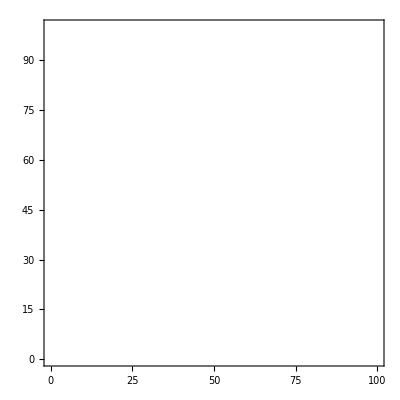

```mathematica
Module[{xmin,ymin,xmax,ymax,
boxwid,boxhgt,boxdim,
boxllx,boxlly,boxll,
xprmin,yprmin,xprmax,yprmax},
boxwid=15;boxhgt=15;boxdim={boxwid,boxhgt};
boxllx=10;boxlly=10;boxll={boxllx,boxlly};
{xprmin,yprmin}={0,0};
{xprmax,yprmax}={100,100};
Graphics[{White,EdgeForm[Thin],
Rectangle[boxll,boxll+boxdim]},
PlotRange->{{xprmin,xprmax},{yprmin,yprmax}},
Frame->True]]
```

```mathematica
({{RE24, □}}
```

a row is a wordline, a column is a bitline.

```mathematica
384/16
```

24

```mathematica
mmbRows=1536 rows
```

1536 rows

```mathematica
mmbCols=4096 columns
```

4096 columns

```mathematica
mmbRows*mmbCols
```

6291456 columns rows

```mathematica
1536*4096 bits
```

6291456 bits

```mathematica
384/64
```

6

a VR is 16*2048

32768 a is VR

```mathematica
4*24*16
```

1536

## Section State of the Bank

Leslie Lamport (Turing Laureate, 2013) wrote a book called “Specifying Systems.”

https://lamport.azurewebsites.net/tla/book.html

It delivers the best method that I know for formally specifying parallel and distributed systems. “Formally,” here, means “in a machine-checkable way.” Specifications written in Lamport's formal language can be machine-checked in a variety of ways, sometimes even proved mathematically. I borrow ideas and notation from Lamport's book for this document.

### 4.Subsection Immutability and State Functions

The most important notational device we borrow from Lamport is the prime to decorate variables whose values are changed in a step of a machine calculation. To reason mathematically, variables must be immutable, that is, ironically, constant. The following makes no sense, mathematically, even though its meaning is obvious to a programmer:

x = 1
x = x + 1
x == 2

To reason mathematically about the computation implied above, we write, instead

x = 1
x' = x + 1
x == 1 && x' == 2

The scope of the two variables, x and x', is a step, which is formally defined below as a pair of contiguous states in a behavior. We encode steps as functions from an input state of the machine, described by variables without primes, to an output state of the machine, described by variables with primes.

The last line above denotes an action, which is an assertion, a Boolean function of a step, which happens to be true of this step. The prime reminds us that the two variables x and x' are related, sequentially, by the step, but also that they are not the same. If you understand this point, much of the material below on steps, behaviors, actions, and temporal logic may be skimmed.

Although this document is not a fully machine-checkable spec, it is a step in that direction. This document has several formal checks and illustrations.

### 4.Subsection State is the Union of Tensor Variables

Lamport’s way of defining a state is an association of values to variables (he uses the words “assignment” of values to variables instead of “association.” We avoid the word “assignment” because it connotes the programmer's idea of changing the values of variables, which is not mathematically sensible).

Lamport's definition is so important that it merits a slogan to memorize:

A state is an association of values to variables.

Every variable in a state has one value, but not vice versa. Some values may associate to more than one variable. Thus, association of values to variables means a partial function from variables to values. We say partial because some variables may not have values specified in a state. In fact, the space of variables includes all possible variables in the entire Universe, at least for an open system. Because the number of such variables is infinite, any finite listing of variables and their values leaves an infinite number of variables with unspecified values. This point is not relevant for calculations within the bank, but should be borne in mind.

The space of values in the bank is the Booleans, isomorphic to the set of numbers B={1,0}. A state of the bank, then, is an association of 1 or 0 to every pertinent variable. What are the pertinent variables?

The bank is divided into 5 tensors, {MMB, RL, GL, GGL, RSP16} (sometimes, the L1 cache is included as a sixth tensor in the state, but not in this document). The first tensor, MMB, has three indices, v_MMB,p_MMB,s_MMB, each index drawn from a respective index set of non-negative integers:

v_MMB | ∈ | V | = | {0, 1,2,…,23}
p_MMB | ∈ | P | = | {0, 1,2,…,2047}
s_MMB | ∈ | S | = | {0, 1,2,…,15}

The indices of MMB always appear in that order, v_MMB,p_MMB,s_MMB. The order is easy to remember because v,p,s sounds like “GPS.” Both v,p,s and “GPS” are ways of specifying locations. A particular triple of index numbers, {v_MMB∈V,p_MMB∈P,s_MMB∈S}, specifies the location of a specific bit in tensor MMB.

Each indexed expression of the form MMB[v_MMB,p_MMB,s_MMB] is a distinct variable in the state of the MMB. For instance, MMB[3,42,6] and MMB[14,999,2] are distinct variables because each can associate to 1 or 0 independently. There are four, independent states specified by these two variables alone. To specify one, entire state of the MMB tensor, we need ‖V‖×‖P‖×‖S‖=786432 Boolean-valued variables. There are 2^786432 distinct states of the MMB, each an independent association of a 1 or 0 to each of the 786432 variables.

How many variables do we need to specify the states of all 5 tensors, the state of the entire bank?

Write MMB [ V,P,S ], with the names of the index sets in place of indices, to mean the entire set of 786432 MMB variables, the entire set of indexed expressions MMB[v_MMB,p_MMB,s_MMB]. Likewise for the other 4 tensors:

MMB [ V,P,S ] | =^def | { MMB[v_MMB,p_MMB,s_MMB],v_MMB∈V,p_MMB∈P,s_MMB∈S }
RL [ P,S ] | =^def | { RL[p_RL,s_RL],p_RL∈P,s_RL∈S }
GL [ P ] | =^def | { GL[p_GL],p_GL∈P }
GGL [ P,G ] | =^def | { GGL[p_GGL,g_GGL],p_GGL∈P,g_GGL∈G }
RSP16 [ R,S ] | =^def | { RSP[r_RSP16,s_RSP16],r_RSP16∈R,s_RSP16∈S }

where

p_RL | ∈ | P |   | same P as for MMB 
s_RL | ∈ | S |   |  same S as for MMB
p_GL | ∈ | P |   | same P
p_GGL | ∈ | P |   | same P
g_GGL | ∈ | G | = | {0, 1,2,3}
r_RSP16 | ∈ | R | = | {0, 1,2,…,127}
s_RSP16 | ∈ | S |   | same S as for MMB

The set of variables of the bank is the union of these sets of tensor variables:

BANK [ V,P,S,G,R ] | =^def | MMB [ V,P,S ]  ∪  RL [ P,S ]  ∪  GL [ P ]  ∪  GGL [ P,G ]  ∪  RSP16 [ R,S ]

Each set of tensor variables is equivalent to the Cartesian product of its index sets. There are

‖V‖×‖P‖×‖S‖ | = | 786432 | variables necessary to specify one state of MMB
‖P‖×‖S‖ | = | 32768 | variables necessary to specify one state of RL
‖P‖ | = | 2048 | variables necessary to specify one state of GL
‖P‖×‖G‖ | = | 8192 | variables necessary to specify one state of GGL
‖R‖×‖S‖ | = | 2048 | variables necessary to specify one state of RSP16

The total number of variables is the sum of the mutually disjoint counts: 831488 variables, one variable for each bit in each tensor in the bank. Assigning a 1 or a 0 to each of these 831488 variables yields 2^831488 distinct states of the entire bank.

### 4.Subsection State Tuples

A state tuple is useful for specifying the state of a single bit in the bank: an association of a value to each of 5 particular tensor variables. The expression

« MMB[v_MMB,p_MMB,s_MMB], RL[p_RL,s_RL], GL[p_GL], GGL[p_GGL,g_GGL], RSP16[r_RSP16,s_RSP16]»

is well defined given 10 specific indices and 5 Boolean values, one for each indexed tensor-variable expression. A particular state tuple, for example, might be

«MMB[14,999,2]=0,RL[413,9]=1,GL[42]=1,GGL[919, 2]=0,RSP16[6,6]=1»

But state tuples are not useful for counting the number of state variables in the bank, nor for counting the number of possible states of the bank. State tuples represent combinations of state variables and their values, not sets of state variables and their values. The number of distinctly indexed state tuples is the size of the Cartesian product of the index sets, ‖V‖×(‖P‖)^4×(‖S‖)^3×‖G‖×‖R‖=3×2^68, stupendously larger than the 831488 Boolean values that are necessary and sufficient to specify a state of the entire bank. Because each state tuple has five bits, the number of state tuples is (2^5=32)×3×2^68=3×2^73. Each state tuple pins down only one bit in the bank, and that's why the number of state tuples is so much larger than the number of state variables. Specifying the entire state of the bank with state tuples requires specifying the Boolean values of only 831488 state tuples. We show one way to choose those tuples in the following section.

### 4.Subsection Var(k): Serializing State Variables

Let’s put state variables in a canonical, serial order, say left-to-right, then row-major order (right-most index increasing fastest) for each tensor. Imagine a linear, 1-based index, k∈{1,2,…,831488}, that uniquely identifies each of the 831488 variables. The smallest 786432 values of k specify variables in MMB in row-major order, the next larger 32768 values of k specify variables in RL in row-major order, and so on. Letting // denote integer quotient and % integer remainder, as in Python, define Var(k) by the piecewise formula (formally spot-checked in the Appendix of this document)

Var(k+1)=^def Piecewise[{{MMB[k//32768,(k//16)%2048,k%16]], 0≤k<786432}, {RL[(k'//16)%2048,k%16], 0≤k'<32768,k'=k-786432}, {GL[k''%2048], 0≤k''<2048,k''=k'-32768}, {GGL[(k'''//4)%2048,k'''%4], 0≤k'''<8192,k'''=k''-2048}, {RSP[(k''''//16)%128,k''''%16], 0≤k''''<2048,k''''=k'''-8192}}]

We might write out the inverse mapping (from state variables to indices) just as easily, but we shall not need it. The point is simply to show a 1-to-1 and “onto” correspondence between the numbers k∈{1,2,…,831488} and the state variables. Pick any k and we can find a state variable, and vice versa. This correspondence is thus an equivalence.

## Section Behaviors, Steps, Actions

Let Ψ be the set of all possible states of a bank (associations of Boolean values to all 831488 variables), and let ψ_i be the i-th state in Ψ, one of the 2^831488 distinct states in Ψ. ψ_i is a vector with 831488 Boolean-valued slots, one slot for each of the 831488 variables. The slots are in serial order as outlined in Section Section.Subsection above; (ψ_i)_k means the k-th slot of vector ψ_i and is a Boolean scalar value.

A behavior is a zero-based, infinite sequence of states, (ψ_0,ψ_1,ψ_2,…). A specification of the machine, including all possible algorithms that it can execute, is a characterization of all allowed behaviors in terms of steps and actions.

A step is a contiguous pair of states in a behavior, (ψ_i,ψ_(i+1)) for all i∈{0,1,2,…}.

An action is a Boolean-valued function of a step. An action is true of a step if the specification allows the step, that is, if the step is in at least one allowed behavior. We write the specification as a collection of actions and a collection of temporal formulas, Boolean-valued combinations of actions that are true or false of a behavior. More about them later.

To write actions conveniently, we put primes on the names of the variables of the second state of the step. A mathematical variable, once you give it a value, ironically means a constant, at least in its scope. If x=9, it’s 9. The states in a step have exactly the same shapes, however, so we can write a step with two sets of similar-looking variables, differing only by primes. We can abbreviate further by not writing out variables that don't change in a step.

For example, consider a simple command

SM_0X0001: SB[x]' = RL;

This command sets the bits in section 0 of SB[x] to the bits in section 0 of RL. The “1” in the section mask SM_0X0001 means that bit number 0, the rightmost bit in the mask, is ON, specifying the single section 0. The section number 0 is an exponent of 2 in the section mask, so 2^0=1 = 0x0001. The x stands for one of 16 RN registers that can contain one of 24 specific VR numbers, say VR number 9. By use of the prime, we may interpret the command as a mathematical equation instead of as a programmer's assignment.

Only 4096 state variables, corresponding to the 2048 plats of MMB and the 2048 plats of RL in the section 0 of each, are involved in this command. We shouldn’t need to write down all 831488 variables of the bank. In fact, let's modify the set notation we had in Definition DisplayFormulaNumbered. In that definition, we wrote MMB[V,P,S] to mean the unordered set of all MMB variables. Let’s reuse the notation to mean serializing and slicing those variables in row-major order, as described in Section Section.Subsection above. This is just what numpy does. Write the state of the bank, before running Command DisplayFormulaNumbered, as P-slices of MMB and RL variables (in numpy, one would write double-colon instead of P):

ψ | = | {MMB[9,P,0]=b_2048} | ∪ | {RL[P,0]=c_2048}

where b_2048 and c_2048 are arbitrary but known bit-vectors of length 2048. The state in Equation DisplayFormulaNumbered is expressed as an unordered set of associations of values to variables, but each association is in lock-step, P-wise, for example:

{MMB[9,42,0]=b_2048[42],MMB[9,817,0]=b_2048[817],…}

The notation in Equation DisplayFormulaNumbered stands for 4096 associations of values to variables: a set of 2048 MMB state equations (associations of values to variables) union a set of 2048 RL state equations (associations of values to variables) . We can rewrite the state in sequential order any time we want via the serialization scheme of Section Section.Subsection.

Now, after command DisplayFormulaNumbered executes, write the state, with a prime, as the following mathematical equation:

ψ' | = | {MMB'[9,P,0]=RL[P,0]}

which is a P-wise slice of 2048 equations similar to that in Equation DisplayFormulaNumbered. We didn't bother to write the 2048 equations {RL'[P,0]=RL[P,0]} because the state of RL didn’t change.

An action of a step (ψ,ψ') built from Equations DisplayFormulaNumbered and DisplayFormulaNumbered, for any VR number x and any single section, is the following Boolean-valued action function, true if the equation on the right-hand side is true:

SingleSectionWrite(ψ,ψ',x,s) | =^def | MMB'[x,P,s]=RL[P,s]

(note the primes) where now, the notation on the right stands for the Boolean AND of 2048 equations:

SingleSectionWrite(ψ,ψ',x,s) | =^def
MMB'[x,0,s]∈ψ'=RL[0,s]∈ψ | ∧
MMB'[x,1,s]∈ψ'=RL[1,s]∈ψ | ∧
… | ∧
MMB'[x,2047,s]∈ψ'=RL[2047,s]∈ψ |

This is obviously true for the step (ψ,ψ') built from Equations DisplayFormulaNumbered and DisplayFormulaNumbered.

## Section Temporal Formulas

An action is true or false of a step, but a temporal formula is true or false of a behavior, an infinite sequence of states and steps. How can we get from actions to temporal formulas for the APU?

Imagine a dumbed-down APU that can only do single-section SB-write commands as in Definition DisplayFormulaNumbered. An almost-good temporal formula for this dumbed-down APU will assert that all variables in any initial state have Boolean values and that every step is a single-section SB-write step. By convention, in Lamport’s methodology, we must also allow stuttering steps, those in which the state does not change. Stuttering steps let us compose the specification of the machine with the specifications of peripherals like I/O boards, which may have different timings. The conventional way to write the specification of the machine, then, is, semi-formally,

Init | =^def | every value in ψ_0 is either 1 or 0
Next(x,s) | =^def | SingleSectionWrite(ψ,ψ',x,s)
Spec | =^def | Init ∧ □(SingleSectionWrite(ψ,ψ',x,s))

where the box character, □, means “always true.” See Lamport's book for a full exposition of temporal formulas.

## Section State Functions

Let f be a state function that transforms a state ψ_i into another state f(ψ_i), possibly into the same state ψ_i. The value of the state function, f(ψ_i), like ψ_i, is a vector with with 831488 Boolean-valued slots. We will use state functions for writing steps, so that

(ψ_i,ψ_(i+1))=(ψ_i,f(ψ_i))

### 7.1 VarsChangedBy and VarsUnchangedBy

The function f may not affect all the bits in the state. For example, for a particular state ψ_i, the vector

∇(i,f)   =^def   ψ_i XOR f(ψ_i)

has 0 precisely in those slots unchanged by f(ψ_i). The vector ∇(i,f) has 831488 slots, just as do ψ_i and f(ψ_i).

The OR of ∇(i,f) across all states

∇(f)   =^def   OR_(i=1)^(2^831488)∇(i,f)   =   OR_(i=1)^(2^831488)[ψ_i XOR f(ψ_i)]

has 0 in only those slots that f does not change for any input state ψ_i. The ones and zeros in ∇(f) partition the 831488 variables into two, disjoint subsets. One subset, VarsChangedBy(f), contains those variables that f changes for at least one input state ψ_i. Those variables correspond to the indices of the ones in ∇(f):

VarsChangedBy(f)  =^def   {Var(k∈{1,2,…,831488}) such that ∇(f)_k=1}

where Var(k) is defined in Definition DisplayFormulaNumbered.

The other subset, VarsUnchangedBy(f), contains those variables that f never changes, corresponding to the indices of the zeros in ∇(f):

VarsUnhangedBy(f)  =^def   {Var(k∈{1,2,…,831488}) such that ∇(f)_k=0}

The only difference between Definitions DisplayFormulaNumbered and DisplayFormulaNumbered is the 1 or 0 at the extreme right.

#### 7.1.1 Examples

The function, g, corresponding to Command 1 above

g ≅ SM_0X1111: RL' = SB[x,y] ^ NRL;

with “≅” meaning “corresponding to,” can only change bits in sections 0, 4, 8, and 12 of RL, so VarsChangedBy(g) includes all 4×2048=8192 variables for those sections of RL and VarsUnchangedBy(g) includes all other variables of the bank.

For another example, consider a tiny machine, with three state variables, m_1,m_2,r_1 and eight states:

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1}, {Subscript[ψ, 3], 0, 1, 0}, {Subscript[ψ, 4], 0, 1, 1}, {Subscript[ψ, 5], 1, 0, 0}, {Subscript[ψ, 6], 1, 0, 1}, {Subscript[ψ, 7], 1, 1, 0}, {Subscript[ψ, 8], 1, 1, 1}},
Frame->{
None,None,
{{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0
ψ_2 | 0 | 0 | 1
ψ_3 | 0 | 1 | 0
ψ_4 | 0 | 1 | 1
ψ_5 | 1 | 0 | 0
ψ_6 | 1 | 0 | 1
ψ_7 | 1 | 1 | 0
ψ_8 | 1 | 1 | 1

A similar table for a full bank has 831488 columns and 2^831488 rows, so obviously exists only in our imaginations.

Now consider a function f that copies the value of the r_1 slot of its input state into the m_2 slot of its output state. Adapting state-tuple notation from Formula DisplayFormulaNumbered:

f(«[m_1,m_2],[r_1]»)   =   «[m_1,r_1],[r_1]»

For the corresponding command, one might write

m2:=r1

Look at the results of f(ψ_i) and ψ_i⊻f(ψ_i) in the table below, with ⊻ meaning XOR. Observe that the only variable (column) with ones in it is m_2 (highlighted), the only variable changed by f. OR’ing down the rows produces ∇(f), which has the same shape as a state, so we can talk about its variables, too. If variable ∇(f)_k=1, then ∇(f)_k is in VarsChangedBy(f), else ∇(f)_k is in VarsUnchangedBy(f). The last, lonely row of the table below shows the partitioning into VarsChangedBy(f)={m_2} and VarsUnchangedBy(f)={m_1,r_1}.

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0, "ψ_1⊻f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1, "ψ_2⊻f(ψ_2)", 0, 1, 0}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0, "ψ_3⊻f(ψ_3)", 0, 1, 0}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1, "ψ_4⊻f(ψ_4)", 0, 0, 0}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0, "ψ_5⊻f(ψ_5)", 0, 0, 0}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1, "ψ_6⊻f(ψ_6)", 0, 1, 0}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0, "ψ_7⊻f(ψ_7)", 0, 1, 0}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1, "ψ_8⊻f(ψ_8)", 0, 0, 0}, {, , , , , , , , "∇(f)", 0, 1, 0}},
Background->{None,None,{{{1,10},{11,11}}->LightYellow}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{1,1},{10,12}}->True,
{{2,9},{9,9}}->True,
{{2,9},{10,12}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True,
{{10,10},{9,9}}->True,
{{10,10},{10,12}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0 | ψ_1⊻f(ψ_1) | 0 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1 | ψ_2⊻f(ψ_2) | 0 | 1 | 0
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0 | ψ_3⊻f(ψ_3) | 0 | 1 | 0
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1 | ψ_4⊻f(ψ_4) | 0 | 0 | 0
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0 | ψ_5⊻f(ψ_5) | 0 | 0 | 0
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1 | ψ_6⊻f(ψ_6) | 0 | 1 | 0
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0 | ψ_7⊻f(ψ_7) | 0 | 1 | 0
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1 | ψ_8⊻f(ψ_8) | 0 | 0 | 0
 |  |  |  |  |  |  |  | ∇(f) | 0 | 1 | 0

#### 7.1.2 By Equivalence Relation

A more mathematically conventional way of partitioning the variables is to define an equivalence relation on variables and then to observe its equivalence classes. Let us say that two variables, x_1 and x_2, with indices k_1 and k_2, are equivalent to change under f, written x_1∼^(! f)x_2, iff [sic, “if and only if”] they have the same value, 0, or 1, under ∇(f):

x_1∼^(! f)x_2   iff    ∇(f)_k_1=∇(f)_k_2

that is, that they’re both changed by f or they’re both not changed by f. The relation ∼^(! f) is obviously reflexive, symmetric, and transitive, being based on equality of bits. Thus, ∼^(! f) is an equivalence relation. As with any equivalence relation, ∼^(! f) induces a partition of the set of variables into equivalence classes, precisely VarsChangedBy(f) and VarsUnchangedBy(f). To be explicit, partitioning means

VarsChangedBy(f) | ∩ | VarsUnchangedBy(f) | = | ∅ | the empty set
VarsChangedBy(f) | ∪ | VarsUnchangedBy(f) | = |   | the set of all variables

Formula DisplayFormulaNumbered is highlighted because it, along with four friends defined immediately below, are important to remember.

### 7.2 VarsUsedBy and VarsUnusedBy

If the k-th variable, v_k, is not used by f, then the output for all input states with v_k=0 equals the output for all input states with v_k=1, if we ignore v_k on the output side. For instance, in the table below, the output columns for m_2 and r_1 for input m_1=0, highlighted in green in the first four rows, are equal to the output columns for m_2 and r_1 for input m_1=1, highlighted in blue in the last four rows.

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1}},
Background->{
None,None,
{{{2,5},{2,2}}->LightGreen,
{{2,5},{7,8}}->LightGreen,
{{6,9},{2,2}}->LightBlue,
{{6,9},{7,8}}->LightBlue}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{2,9},{9,9}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1

The equality of the green output block to the blue output block means that f does not use m_1, because the outputs don’t depend on the value of m_1. Let’s rearrange the rows for visual convenience, and see whether f uses m_2. We’ll put the rows and states with m_2=0 at the top of the table and the rows and states with m_2=1 at the bottom:

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1}},
Background->{
None,None,
{{{2,5},{3,3}}->LightGreen,
{{2,5},{6,6}}->LightGreen,
{{2,5},{8,8}}->LightGreen,
{{6,9},{3,3}}->LightBlue,
{{6,9},{6,6}}->LightBlue,
{{6,9},{8,8}}->LightBlue}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{2,9},{9,9}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1

Again, the equality of the green output block to the blue output block shows that f does not use m_2. Notice, however, that m_2 is changed by f, even though it’s not used by f. That fact shows that VarsChangedBy(f) can overlap VarsUnusedBy(f). That's important to remember:

VarsChangedBy(f) | ∩ | VarsUnusedBy(f) may not be empty

Let's rearrange once more and check r_1:

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1}},
Background->{
None,None,
{{{2,5},{4,4}}->LightGreen,
{{2,5},{6,7}}->LightYellow,
{{6,9},{4,4}}->LightBlue,
{{6,9},{6,7}}->LightRed}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{2,9},{9,9}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1

Sure enough, the yellow output block does not equal the orange output block. We’ve changed colors to suggest “warning.” The meaning is that f does use r_1. We also see that VarsUnchangedBy(f) can overlap VarsUsedBy(f) because r_1 is not changed by f:

VarsUsedBy(f) | ∩ | VarsUnchangedBy(f) may not be empty

#### Section.Subsection.Subsubsection By Equivalence Relation

In general, even in our huge, notional, 2^831488×831488 table for the bank, it is clear that any variable v is either used or not used by f, because the output blocks for inputs v=0 and v=1, striking out the column for v, are either equal or not equal. An equivalence relation for this happenstance exists because the variables are partitioned into VarsUsedBy(f) and VarsUnusedBy(f).

Formalizing that equivalence relation is straightforward, but I did not find a way without tedious notation. However, because we know the equivalence relation exists, we can name it. Let us say that two variables, x_1 and x_2, are equivalent under application of f, written x_1∼^(f @)x_2, iff they are both used by f or both not used by f. The equivalence classes induces the partitions VarsUsedBy(f) and VarsUnusedBy(f). Explicitly,

VarsUsedBy(f) | ∩ | VarsUnusedBy(f) | = | ∅,must be empty

### 7.3 The Other Intersection

We’ve seen that

VarsChangedBy(f) | ∩ | VarsUnchangedBy(f) | = | ∅ | (DisplayFormulaNumbered)
VarsChangedBy(f) | ∩ | VarsUnusedBy(f) | ≠ | ∅ | (DisplayFormulaNumbered)
VarsUsedBy(f) | ∩ | VarsUnchangedBy(f) | ≠ | ∅ | (DisplayFormulaNumbered)
VarsUsedBy(f) | ∩ | VarsUnusedBy(f) | = | ∅ | (DisplayFormulaNumbered)

There is one more possibility (actually two if you’re counting carefully, but set-intersection is commutative, so the two are the same):

VarsChangedBy(f) | ∩ | VarsUsedBy(f) | ≠ | ∅

That means that some commands may both use and change some of the same variables. An example is a modification of Function DisplayFormulaNumbered, above:

SM_0X1111: RL' = SB[x,y] ^ RL;

This command uses sections 0,4,8,12 of RL and then changes them. The hardware allows this kind of command, but it’s not compatible with other instances of its kind, as we see below.

## Section Compatible and Interfering State Functions

Two state functions, f and g, are compatible, written f~g, if their VarsChangedBy subsets are disjoint and if their VarsUsedBy subsets do not mutually overlap their VarsChangedBy subsets:

f∼g | iff | VarsChangedBy(f) | ∩ | VarsChangedBy(g) | = | ∅
  | ∧ | VarsUsedBy(f) | ∩ | VarsChangedBy(g) | = | ∅
  | ∧ | VarsUsedBy(g) | ∩ | VarsChangedBy(f) | = | ∅

illustrated in the following Venn diagram (recall from Formula DisplayFormulaNumbered that VarsChangedBy(f) and VarsUsedBy(f) may overlap for a single function, but compatibility does not allow mutual overlap of VarsChangedBy in pairs):

-Graphics-

Compatibility pertains to state functions, but we also say that commands are compatible or not because commands correspond, 1-to-1, to state functions.

Let’s dispose of the comment after Command DisplayFormulaNumbered before going further. Imagine two similar instances

f ≅ SM_0X1111: RL = SB[x,y] ^ RL;
g ≅ SM_0X1111: RL = SB[z,w] & RL;

VarsChangedBy(f) overlaps VarsUsedBy(f); that’s allowed, and the same goes for g, in isolation. However, VarsChangedBy(f) overlaps VarsUsedBy(g), so f and g are not compatible. In this case, the values of SB numbers, x,y,z,w do not matter regarding compatibility. They could be all different or some of them could be the same, and f and g are still not compatible.

Informally, compatibility means that f and g don’t change any of the same variables and don’t use variables that the other changes. Compatibility encodes absence of race conditions when running compatible commands in parallel. This fact yields our first operational result. It’s safe to run mutually compatible commands in parallel. An optimizing compiler can write them together in any order in a parallel bundle, also called an instruction.

Compatible commands aren't the only pairs that are safe to run in parallel. More cases are coming up.

### 8.1 Compatibility is not an Equivalence Relation

Compatibility is not an equivalence relation. First of all, it’s not reflexive. A function is not compatible with itself. Operationally, this means that we cannot run two copies of the same command in parallel.

Compatibility is symmetric. If f∼g, then g∼f. Operationally, this means that the programmer may write compatible commands in either order.

Compatibility is not transitive; f may be compatible with g, and g with h, but f may not be compatible with h, as shown in the following diagram:

-Graphics-

Operationally, this means that the programmer (or the compiler!) must think hard when writing more than two commands to run in parallel.

Because compatibility is not an equivalence relation, compatibility does not partition the set of commands, let alone the much larger set of functions. Programmers (and compilers!) must check mutual compatibility of all commands they want to run in parallel.

### 8.2 Non-Compatibility not an Equivalence Relation

Functions that are not compatible are interfering. Interference is also not an equivalence relation. Though it is reflexive and symmetric, it is not transitive. If f interferes with g, and g interferes with h, f may not interfere with h. Here’s an example:

f ≅ SM_0X1111: SB[x]' = RL;

interferes with

g ≅ SM_0X3333: SB[x]' = RL;

because sections 0,4,8,12 of SB[x] are in the VarsChangedBy subsets of both f and g. g interferes with h, where

h ≅ SM_0X6666: SB[x]' = RL;

because sections 1,5,9,13 of SB[x] are in the VarsChangedBy subsets of both g and h. But f and h are compatible — non-interfering — because their section masks and their VarsChangedBy subsets are disjoint.

### 8.3 Instructions

Compatibility extends to any set of state functions or commands, beyond just pairs. A set of state functions f_i is compatible if they are mutually compatible in pairs. Operationally, the machine supports up to four mutually compatible commands in up to four lanes of an instruction ("instruction" for the bank means an unordered set of up to four commands in the four lanes, and it is an unusual usage of the term "instruction").

#### Section.Subsection.Subsubsection Common-Case Rule of Thumb

Compatibility of APL commands is guaranteed if the section masks or the VRs are all disjoint.

SM_0X1111: RL' = SB[x] ^ NRL;
SM_0X2222: RL' ^= SB[x,y,z] & RSP16
SM_0X8888: RL' = SB[y]
SM_0X4444: RL' &= SB[x,z]

is a compatible set because all the section masks are disjoint, including the implied section masks from NRL, namely -1,3,5,7. Likewise,

SM_0X1111: SB[x]' = RL;
SM_0X1111: SB[y,z]' = RL;

is a compatible set iff x, y, and z are distinct VR numbers.

## Section Safe but Non-Compatible Cases

### 9.1 Write SB Before Reading RL

Sometimes, commands are safe to run in parallel even if they’re not compatible. Consider the following instruction of two commands:

f ≅ SM_0X3333: SB[x]' = RL;
g ≅ SM_0X3333: RL' = SB[y] ^ GL;

VarsUsedBy(f) includes certain sections of RL, whereas VarsChangedBy(g) includes the same sections of RL, violating compatibility. It’s easiest to see that violation from Venn diagram DisplayFormulaNumbered.

The reason they’re safe to run in parallel is that machine reads RL in a rising half-clock cycle and then updates it in the falling half-clock cycle.

Mathematically, the RL on the left-hand sides of Instruction DisplayFormulaNumbered is a different state of RL to the one on the right-hand side. To spell out the meaning with Lamport's primes

SM_0X3333: SB[x]' = RL;       // writes SB[x] from old value of RL
SM_0X3333: RL' = SB[y] ^ GL;  // reads from old value of SB[y]

The programmer doesn't use primes, and might write the commands in (DisplayFormulaNumbered) in the other order in an instruction:

SM_0X3333: RL = SB[y] ^ GL;
SM_0X3333: SB[x] = RL;

The results would be the same: the second command in (DisplayFormulaNumbered) would read bits from the old value of RL.

The potential for human confusion is high. In a careless imperative reading of Instruction DisplayFormulaNumbered, it appears that RL is updated before it's used. Worse, RL would be updated before used if the two commands were written in separate instructions in the same order. In such a case, the instructions would run sequentially and not in parallel. This happenstance is a known hazard of our programming model.

#### Section.Subsection.Subsubsection A Critical Restriction

A very important restriction on these considerations, is that x and y must be different. It is not allowed to read and write the same SB sections in the same instruction. Such introduces another kind of race condition, one in the sub-clocks of the machine.

### 9.2 Read into RL before Broadcast

Similarly, the machine allows a read that updates RL to execute in parallel with an interfering broadcast that updates GL, GGL, or RSP16. For example,

f ≅ SM_0X3333: RL' = SB[x] ^ RL;
g ≅ SM_0X2222: GL' = RL';

are allowed in one instruction. These two lines interfere because VarsChangedBy(f) overlaps VarsUsedBy(g), and a glance at Venn diagram DisplayFormulaNumbered shows that’s interfering.

Emphasizing the primes, reading the commands as mathematical equations,

SM_0X3333: RL' = SB[x] ^ RL;
SM_0X2222: GL' = RL';

the update of RL happens before the update of GL in rising and falling half-clock cycles respectively. Notice that the order of updating in Instruction DisplayFormulaNumbered — reading into RL before reading from RL — is the opposite to the order of the Instructions DisplayFormulaNumbered and DisplayFormulaNumbered — read from RL before reading into RL. Careful programmers will always write commands in an order that is amenable to a careless-but-intuitive, imperative reading. But we cannot count on all programmers being so careful and we must remember the rules.

## Section All Safe Cases Covered?

Compatibility covers most cases of commands that are safe to run in parallel. The special cases in Section Section cover a few more common ones. We do not yet know whether this document covers all safe cases allowed by the machine. We will update the document when we learn more.

## Section Case Study: GVML u16 Adder

### Section.Subsection Overview

GVML has a sophisticated adder for unsigned, 16-bit integers. It packs 30 APL commands into 12 instructions that execute in 12 clocks. It is a perfect test case for the compatibility theory above and for both of the safe-but-incompatible combinations of Section Section. It is also a worthy target for BELEX.

#### Section.Subsection.Subsection Low-Level and High-Level BELEX

There are two ways to go about transcribing this or any algorithm into BELEX: at a low level and at a higher level. The default is higher-level: the compiler vectorizes; rolls and unrolls loops; parallelizes section operations; selects commands; automatically provisions, coalesces, and recycles temporaries; allocates registers; and schedules instructions, parallelizing lanes. The compiler for high-level BELEX also performs standard optimizations like dead-code removal, constant folding, common subexpression elimination, and peephole optimizations.

Code generated from high-level BELEX will often be better than naive APL, but seldom as good as hand-optimized APL. It is not plausible for an optimizing compiler to generate code as good as this GVML adder without excessive hinting, so much hinting that the programmer might just as well write the sophisticated code literally, as programmers do with the #asm keyword in C. Naturally, over time, the compiler's optimizations will improve, but optimization will always have heuristic elements that can't match human expertise.

### Section.Subsection Notation

Except where explicitly specified as code (Mathematica, Python, BELEX), the notation in this document is a mix of Mathematica, traditional mathematical notation, and pseudocode. For example, given bits a and b, we might write ab, a∧b, a && b, a&b, a×b, a*b, a AND b, And[a,b], etc., to denote the Boolean AND of the two bits, depending on what is convenient in each context. Likewise, a+b, a||b, a OR b, etc., might denote the Boolean OR of the two bits.

Remember that Boolean +, as OR, distributes across *, as AND, so that a+(b*c)=(a+b)*(a+c). This rule is contrary to the usual meanings of + and *, so we avoid + and * notations in contexts where that special distributive rule is pertinent. But, to prove the point, consider the following tautology:

```mathematica
TautologyQ[
a∨(b∧c)⧦
(a∨b)∧(a∨c),
{a,b,c}]
```

True

#### Section.Subsection.Subsubsection GF(2) and Tartan

In some contexts, specifically about Tartan, we do arithmetic in GF(2), the unique finite field of order 2, and not in Boolean algebra. In that context, OR does not pertain and + means XOR. We are careful to stress the point each time we make the notational switch.

https://en.wikipedia.org/wiki/GF%282%29

#### Section.Subsection.Subsubsection Section Notation

To save space, we write section-number lists in ordered hex strings without commas and without a leading "0x": c_("159D") means c_{1,5,9,D=13} and not c_("0x159D"), which would mean c_("023478AC"). Lack of a subscript means “all sections,” as in c==c()==c[:]==c[::]==c_("0123456789ABCDEF"). A numerical subscript, as in c_(16^^169D), is a section mask, not a section-number list.

#### Section.Subsection.Subsubsection Naming Conventions

To save space and parentheses, we usually write x XOR y==(x^y) as  x▴y, bound more tightly than & or |. It is Plus, without carry, in GF(2). Notice that the x and y in x▴y are not italicized, even though italics are standard in mathematical notation. The omission of italics is not significant. Mathematica removes italics from strings of mathematical notation of more than one character. It's possible to fix that problem with InvisibleSpace, but it's a lot of work to keyboard that into every instance.

Machine variables and functions are in all caps, like RL, GL, GL(), GGL, BGGL(), RSP16, BRSP16(). User-visible BELEX variables and functions, are in lower case, like add_u16, x, y, and x▴y.

It is already natural to write (x&y) as xy. Notice, again, it’s not italicized by default.

Multiple, comma-separated VRs, (up to 3), in an SB expression, as in SB[x,y] or SB[x, y, z], are implicitly ANDed.

### Section.Subsection Unit Testing

Here are some utility functions for aiding the unit tests in the Mathematica code. The notebook is NOT TESTED with unit testing off.

```mathematica
ClearAll[unitTesting,echo,tinyPlot];
On@Assert;
unitTesting=True;
echo=If[unitTesting,Echo,Identity];
tinyPlot=If[unitTesting,
ArrayPlot[#,ImageSize->Tiny]&,
(* else *)Function[x,Null]];
```

Check wordline equality with a stride of 4, a common case in this study, e.g., for GGL. For example, check sections {0, 4, 8, 12}, or sections {1, 5, 9, 13}, and so on.

```mathematica
ClearAll[check4s];
check4s[left_,right_,offs_,tag_]:=
Do[Assert[left⟦1+i+offs⟧===right⟦1+i+offs⟧,tag],{i,0,12,4}];
```

#### Section.Subsection.Subsubsection Statistical Testing

A few unit tests are statistical. The following is the background information for interpreting those tests.

Via John D. Cook (www.johndcook.com):

1. The probability that the OR of two random bits is ON is 3/4, so the expected number of ON bits in the OR of N random bits is 3N/4.

The probability that the AND of two random bits is ON is 1/4, so the expected number of ON bits in the AND of N random bits is N/4.

The XOR of two random bits have probability 1/2 of being ON, so the expected number of ON bits in the XOR of N random bits is N/2.

2. You have a Binomial(p, N) distribution with p = 3/4, 1/4, or 1/2. The expected value is Np as above.

The variance is N p(1-p), so the standard deviation is √(N p (1 - p)), so√(3N/16) for AND and OR, and √(N/4) for XOR.

3. If N is big, e.g. > 30. In that case a Binomial(p, N) is well approximated by a normal with the same mean and variance:

Binomial(N, p) approx Normal with mean N p and variance N p(1-p).

Here's a post about converting between 9s and sigmas.

https://www.johndcook.com/blog/2019/06/20/nines-and-sigmas/

Nines and sigmas are two ways to measure quality. You'll hear something has four or five nines of reliability or that some failure is a five sigma event.

So for a test, compute sigma = √(N p (1 - p)). If your mean is k sigmas away from the expected value, and k is any bigger than 2, you're very likely seeing an error.

### Section.Subsection Section Lists & Section Masks

#### Section.Subsection.Subsubsection Section Lists

Section lists are ordered, 1D arrays of exponents of 2. For instance, section mask 0x1111 corresponds to a section list of bit numbers {0,4,8,12} because 0x1111==2^0+2^4+2^7+2^12. We normally write section lists in hexadecimal and then pack them into hex strings, one character per section number, so {0,4,8,12} is {0,4,8,C} in hex and "048C" in a hex string.

Section lists are ordered: {0,4,8,C} is not the same as {4,C,0,8}, even though they both specify the same section mask. Ordered lists support permutations and shift-copies of sections. The semantics of order in section lists is explained in detail below in Section Section.Subsection.Subsubsection.

The following is the beginning of some Mathematica code for verifying our analysis. The code begins with a round-tripping unit test for section lists.

```mathematica
ClearAll[sectionListFromSectionMask,sectionMaskFromSectionList];
sectionListFromSectionMask[mask_]:=Flatten[Position[Reverse[IntegerDigits[mask,2]],1]-1];
sectionMaskFromSectionList[bitNumbers_]:= Plus@@(2^#1&/@bitNumbers);
```

```mathematica
If[unitTesting,
Module[{i},For[i=0;i<2^16,i++,
Assert[i===sectionMaskFromSectionList@sectionListFromSectionMask@i]]]]
```

#### Section.Subsection.Subsubsection Section Masks

Section mask 16^^1111 corresponds to hex bit numbers {0,4,8,C} = "048C", 
16^^1111 << 1 to 16^^2222 = {1,5,9,D} = "159D", 
16^^1111 << 2 to 16^^4444 = {2,6,A,E} = "26AE", and 
16^^1111 << 3 to 16^^8888 = {3,7,B,F} = "37BF".

For another example, The section mask 16^^3333 corresponds to the following section list: {0,1,4,5,8,9,C,D}="014589CD"

Here are some convenience functions for splicing arguments from frequently used masks in the examples below. It will become obvious how to use them.

```mathematica
ClearAll[
s048C,s159D,s26AE,s37BF,s4567,s89AB,sCDEF,(* section-number lists *)
sFFFF,sFFFE,s7FFF,s3333,(* exceptions: actual bit masks *)
m048C,m159D,m26AE,m37BF,m4567,m89AB,mCDEF,(* section-number lists *)
mFFFF,mFFFE,m7FFF,m3333](* exceptions: actual bit masks *);
m048C=16^^1111;s048C[x_]:=Sequence[m048C,x];
m159D=16^^2222;s159D[x_]:=Sequence[m159D,x];
m26AE=16^^4444;s26AE[x_]:=Sequence[m26AE,x];
m37BF=16^^8888;s37BF[x_]:=Sequence[m37BF,x];
m4567=sectionMaskFromSectionList[{4,5,6,7}];s4567[x_]:=Sequence[m4567,x];
m89AB=sectionMaskFromSectionList[{8,9,10,11}];s89AB[x_]:=Sequence[m89AB,x];
mCDEF=sectionMaskFromSectionList[{12,13,14,15}];sCDEF[x_]:=Sequence[mCDEF,x];

mFFFE=16^^FFFE;sFFFE[x_]:=Sequence[mFFFE,x];
m7FFF=16^^7FFF;s7FFF[x_]:=Sequence[m7FFF,x];
mFFFF=16^^FFFF;sFFFF[x_]:=Sequence[mFFFF,x];
m3333=16^^3333;s3333[x_]:=Sequence[m3333,x];
(* mandatory blank line *)
```

#### Section.Subsection.Subsubsection Ordered Section Lists: Permutations and Shifts

Section lists in strings are ordered: c_("048C")<=c_("4C08") specifies a permutation in parallel, whereby section 4 of c is moved to section 0, section C is moved to section 4, and so on.

c_("048C") <= a_("159D") | b_("26AE") means "copy the OR of section 2 of b and section 1 of a to section 0 of c, the OR of section 6 of b and section 5 of a to section 4 of c, and so forth. In general, in complex expressions, the number of section numbers in every section list must be the same, or the section list must be empty.

Repeated indices are permitted on the right-hand sides; c_("048C") <= c_("4405") means copy, in parallel, section 4 to section 0, section 4 to section 4, section 0 (the old section 0, not the new one) to section 8, and section 5 to section C. The permutation is done in parallel; that’s why the old section 0 is copied to section 8. To perform a sequential permutation, copying the new section 0, multiple commands are required, as in c_("04C") <= c_("405"); c_("8") <= c_("0").

### Section.Subsection Background: Ripple-Carry and Carry Lookahead (UNDONE)

A ripple-carry adder computes one sum bit and one carry bit at a time. Each sum bit, s_i,i∈[1..N] is the XOR of a first addend bit, a_i, a second addend bit, b_i, and a carry bit, c_(i-1), carried over from the prior bit, i-1. By convention, c_0 is a constant false or 0 unless the adder is ganged to upstream adders.

```mathematica
ClearAll[sum];
sum[a_,b_,c_]:=a⊻b⊻c;
```

#### Section.Subsection.Subsubsection Carry-Out Conditions

The obvious rule for the carry-out bit c_i is true iff two or three of the inputs are true: if both a_i and b_i are true, or if either or both of a_i and b_i are true and a prior carry c_(i-1) is true. Write this condition as follows:

```mathematica
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[a, i]∧Subscript[c, i-1])∨(Subscript[b, i]∧Subscript[c, i-1])∨(Subscript[a, i]∧Subscript[b, i]∧Subscript[c, i-1])
```

(a_i&&b_i)||(a_i&&c_(-1+i))||(b_i&&c_(-1+i))||(a_i&&b_i&&c_(-1+i))

The following tautology shows a simplification: we need not explicitly test the case a_i b_i c_(i-1) of all three bits:

```mathematica
TautologyQ[
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[a, i]∧Subscript[c, i-1])∨(Subscript[b, i]∧Subscript[c, i-1])∨(Subscript[a, i]∧Subscript[b, i]∧Subscript[c, i-1])⧦
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[a, i]∧Subscript[c, i-1])∨(Subscript[b, i]∧Subscript[c, i-1]),
{Subscript[a, i],Subscript[b, i],Subscript[c, i-1]}]
```

True

The following tautology demonstrates an even shorter form of the same formula by factoring out c_(i-1). It states that a carry-out is generated if a_i and b_i are true or if c_(i-1) is true and either or both of a_i and b_i are true, which is exactly the statement made above in English, just in another form. This form is Equation 2 in the patent

https://patentimages.storage.googleapis.com/7e/21/a7/8b6287e4efbdff/US20210081173A1.pdf

```mathematica
TautologyQ[
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[a, i]∧Subscript[c, i-1])∨(Subscript[b, i]∧Subscript[c, i-1])⧦
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[c, i-1]∧(Subscript[a, i]∨Subscript[b, i])),
{Subscript[a, i],Subscript[b, i],Subscript[c, i-1]}]
```

True

#### Section.Subsection.Subsubsection Conjunctive Normal Form (CNF)

The tautology above holds if AND and OR are switched, i.e., ab+c(a+b)==(a+b)(c+ab). That fact turns out to be convenient for understanding expressions later on.

```mathematica
TautologyQ[
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[a, i]∧Subscript[c, i-1])∨(Subscript[b, i]∧Subscript[c, i-1])⧦
(Subscript[a, i]∧Subscript[b, i])∨(Subscript[c, i-1]∧(Subscript[a, i]∨Subscript[b, i]))⧦
(Subscript[a, i]∨Subscript[b, i])∧(Subscript[c, i-1]∨(Subscript[a, i]∧Subscript[b, i])),
{Subscript[a, i],Subscript[b, i],Subscript[c, i-1]}]
```

True

#### Section.Subsection.Subsubsection Lemma Function cout

Package this as a lemma function convenient for the following proofs of carry look ahead, and test the function.

```mathematica
ClearAll[cout];
cout[a_,b_,carryIn_]:=(a∧b)∨(carryIn∧(a∨b));

TautologyQ[
(a∧b)∨(b∧c)∨(a∧c)(* DNF *)⧦
(a∨b)∧(b∨c)∧(a∨c)(* CNF *)⧦
cout[a,b,c],
{a,b,c}]
```

True

#### Section.Subsection.Subsubsection Carry Look Ahead (CLA)

The general carry-out formula for at least 3 bits of ripple in disjunctive normal form (DNF, all OR on the right of each line of ANDs) is the following, Equation 3 in the patent (after corrections, coloring, and rearrangement to make symmetries more obvious):

C_(out-N)= | C_in | ∧ | (A_1∨B_1) | ∧ | (A_2∨B_2) | ∧ | ⋯ | ∧ | (A_N∨B_N) | ∨
  | (A_1∧B_1) | ∧ | (A_1∨B_1) | ∧ | (A_2∨B_2) | ∧ | ⋯ | ∧ | (A_N∨B_N) | ∨
  |   |   |   |   | ⋯ | ∧ | ⋯ | ∧ | ⋯ | ∨
  |   |   |   |   | (A_(N-2)∧B_(N-2)) | ∧ | (A_(N-1)∨B_(N-1)) | ∧ | (A_N∨B_N) | ∨
  |   |   |   |   |   |   | (A_(N-1)∧B_(N-1)) | ∧ | (A_N∨B_N) | ∨
  |   |   |   |   |   |   |   |   | (A_N∧B_N) |

Specialized to four bits, the interesting case for the APU, it is

C_(out-N)= | C_in | ∧ | (A_1∨B_1) | ∧ | (A_2∨B_2) | ∧ | (A_3∨B_3) | ∧ | (A_4∨B_4) | ∨
  | (A_1∧B_1) | ∧ | (A_1∨B_1) | ∧ | (A_2∨B_2) | ∧ | (A_3∨B_3) | ∧ | (A_4∨B_4) | ∨
  |   |   | (A_1∧B_1) | ∧ | (A_2∨B_2) | ∧ | (A_3∨B_3) | ∧ | (A_4∨B_4) | ∨
  |   |   |   |   | (A_2∧B_2) | ∧ | (A_3∨B_3) | ∧ | (A_4∨B_4) | ∨
  |   |   |   |   |   |   | (A_3∧B_3) | ∧ | (A_4∨B_4) | ∨
  |   |   |   |   |   |   |   |   | (A_4∧B_4) |

Next, we show that this formula is equivalent to four, nested (rippled) applications of the cout lemma:

```mathematica
TautologyQ[
cout[Subscript[a, 4],Subscript[b, 4],cout[Subscript[a, 3],Subscript[b, 3],cout[Subscript[a, 2],Subscript[b, 2],cout[Subscript[a, 1],Subscript[b, 1],Subscript[c, 0]]]]]⧦
(         Subscript[c, 0]       ∧(Subscript[a, 1]∨Subscript[b, 1])∧(Subscript[a, 2]∨Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 1]∨Subscript[b, 1])∧(Subscript[a, 2]∨Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∨Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 2]∧Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 3]∧Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 4]∧Subscript[b, 4])),
{Subscript[c, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]}]
```

True

Next, we show that the second line in the expansion is not necessary. The following formula is smaller and more symmetric than the prior formula.

```mathematica
TautologyQ[
cout[Subscript[a, 4],Subscript[b, 4],cout[Subscript[a, 3],Subscript[b, 3],cout[Subscript[a, 2],Subscript[b, 2],cout[Subscript[a, 1],Subscript[b, 1],Subscript[c, 0]]]]]⧦
(         Subscript[c, 0]       ∧(Subscript[a, 1]∨Subscript[b, 1])∧(Subscript[a, 2]∨Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 1]∧Subscript[b, 1])∧(Subscript[a, 2]∨Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 2]∧Subscript[b, 2])∧(Subscript[a, 3]∨Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 3]∧Subscript[b, 3])∧(Subscript[a, 4]∨Subscript[b, 4]))∨
((Subscript[a, 4]∧Subscript[b, 4])),
{Subscript[c, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]}]
```

True

Next, we show that the tautology holds if OR is replaced with XOR in the internal, propagator, slots, leaving AND in the carry-in, generator, slots:

```mathematica
ClearAll[gp4];
gp4[g_,p_]:=
TautologyQ[
cout[Subscript[a, 4],Subscript[b, 4],cout[Subscript[a, 3],Subscript[b, 3],cout[Subscript[a, 2],Subscript[b, 2],cout[Subscript[a, 1],Subscript[b, 1],Subscript[c, 0]]]]]⧦
(Subscript[c, 0]∧(Subscript[a, 1]~p~Subscript[b, 1])∧(Subscript[a, 2]~p~Subscript[b, 2])∧(Subscript[a, 3]~p~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 1]~g~Subscript[b, 1])∧(Subscript[a, 2]~p~Subscript[b, 2])∧(Subscript[a, 3]~p~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 2]~g~Subscript[b, 2])∧(Subscript[a, 3]~p~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 3]~g~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 4]~g~Subscript[b, 4])),
{Subscript[c, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]}];
gp4[And,Or]===gp4[And,Xor]===True
```

True

#### Moshe's Comment

Moshe's sole documentation of the actual adder implementation is the comment below.

```mathematica
1. cout1[0] =  X[0]^Y[0]
2. cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1])
3. cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2])
4. cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3])

5. cout0[0] = X[0] && Y[0]
6. cout0[1] = X[1] && Y[1] | (cout0[0] && X[1]^Y[1])
7. cout0[2] = X[2] && Y[2] | (cout0[1] && X[2]^Y[2])
8. cout0[3] = X[3] && Y[3] | (cout0[2] && X[3]^Y[3])
```

The first four lines of the comment are misleading. They purport the conditional carry-out of a nibble assuming the carry-in is 1. However, the carry-out for that case is actually (cout1 ∨ cout0). The following tautologies prove that proposition. The second four lines purport the carry-out of a nibble assuming the carry-in is 0, and they are proved below.

Separate the 0 and 1 cases for c_0 by lifting c_0 into a parameter, cIn:

```mathematica
ClearAll[eq3];
eq3[g_,p_,cIn_]:=
(cIn∧(Subscript[a, 1]~p~Subscript[b, 1])∧(Subscript[a, 2]~p~Subscript[b, 2])∧(Subscript[a, 3]~p~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 1]~g~Subscript[b, 1])∧(Subscript[a, 2]~p~Subscript[b, 2])∧(Subscript[a, 3]~p~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 2]~g~Subscript[b, 2])∧(Subscript[a, 3]~p~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 3]~g~Subscript[b, 3])∧(Subscript[a, 4]~p~Subscript[b, 4]))∨
((Subscript[a, 4]~g~Subscript[b, 4]));
TautologyQ[
eq3[And,Or,Subscript[c, 0]]⧦eq3[And,Xor,Subscript[c, 0]]⧦
cout[Subscript[a, 4],Subscript[b, 4],cout[Subscript[a, 3],Subscript[b, 3],cout[Subscript[a, 2],Subscript[b, 2],cout[Subscript[a, 1],Subscript[b, 1],Subscript[c, 0]]]]],
{Subscript[c, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]}]
```

True

Ravel the first four lines of Moshe's comment, the poorly-named cout1, so that the first four lines are similar to the second four lines.

```mathematica
Subscript[cout1, 0]=(Subscript[a, 1]⊻Subscript[b, 1]);
Subscript[cout1, 1]=(Subscript[a, 2]⊻Subscript[b, 2])∧Subscript[cout1, 0];
Subscript[cout1, 2]=(Subscript[a, 3]⊻Subscript[b, 3])∧Subscript[cout1, 1];
Subscript[cout1, 3]=(Subscript[a, 4]⊻Subscript[b, 4])∧Subscript[cout1, 2]
```

(a_4⊻b_4)&&(a_3⊻b_3)&&(a_2⊻b_2)&&(a_1⊻b_1)

Spot-check the fourth line.

```mathematica
Subscript[cout1, 3]=((Subscript[a, 1]⊻Subscript[b, 1])&&(Subscript[a, 2]⊻Subscript[b, 2])&&(Subscript[a, 3]⊻Subscript[b, 3])&&(Subscript[a, 4]⊻Subscript[b, 4]))
```

(a_1⊻b_1)&&(a_2⊻b_2)&&(a_3⊻b_3)&&(a_4⊻b_4)

See that the first four lines of the comment, cout1_3 is NOT equivalent to Equation 3 with cIn==True:

```mathematica
TautologyQ[Subscript[cout1, 3]⧦eq3[And,Xor,True]]
```

False

However, the second four lines of the comment ARE equivalent to Equation 3, specialized on cIn==False:

```mathematica
Subscript[cout0, 0]=(Subscript[a, 1]∧Subscript[b, 1]);
Subscript[cout0, 1]=(Subscript[a, 2]∧Subscript[b, 2])∨(Subscript[cout0, 0]∧(Subscript[a, 2]⊻Subscript[b, 2]));
Subscript[cout0, 2]=(Subscript[a, 3]∧Subscript[b, 3])∨(Subscript[cout0, 1]∧(Subscript[a, 3]⊻Subscript[b, 3]));
Subscript[cout0, 3]=(Subscript[a, 4]∧Subscript[b, 4])∨(Subscript[cout0, 2]∧(Subscript[a, 4]⊻Subscript[b, 4]));
```

```mathematica
TautologyQ[Subscript[cout0, 3]⧦eq3[And,Xor,False]]
```

True

See that (cout1_3∨cout0_3) is Equation 3 with cIn==True:

```mathematica
TautologyQ[Subscript[cout0, 3]∨Subscript[cout1, 3]⧦eq3[And,Xor,True]]
```

True

### Section.Subsection Low-Level BELEX

#### Section.Subsection.Subsubsection Numpy-Like and Call-Like Syntax

Low-level BELEX supports both numpy-like array-indexing syntax with square brackets and call-like syntax with round brackets. For example, one may specify sections {0,4,8,C} of a variable c in the following ways:

c[[0,4,8,12]] ==  # Nested brackets: looking forward to 2nd plat index (Tartan)
c[0x1111] ==
c["048C"] ==
c([0,4,8,12]) ==
c[[0:13:4]) ==
c(0x1111) ==
c("048C")

channels = [1, 5, 9, 13]
c(channels[0:2])

To specify all sections, a slice operator is required in numpy-like syntax. The following code specifies all sections of variable c:

c() ==
c[:] ==
c[::]

An explicit slice object can be used in call-like syntax to denote "all sections:"

c(slice(None, None, None))

More general slices, along with range expressions, can be convenient:

c(0x00F0) ==
c([4, 5, 6, 7]) ==
c(range(4,8)) ==
c[4:8]

c[[0,4,8,12]] == c[0:13:4] ==
c(slice(0, 13, 4))  # unlikely, but allowed

#### Section.Subsection.Subsubsection Assignment Expressions

BELEX, literal and figurative, has four types of assignment expression, illustrated by examples with all sections:

1. Assign all sections of x XOR y to RL:

RL() <= x() ^ y()

2. AND all sections of x XOR y with all sections of RL and replace all sections of RL with the result:

RL() &= x() ^ y()

3. XOR all sections of x AND y with all sections of RL and replace all sections of RL with the result. Can be accomplished via implicit ANDing as in SB[x,y].

RL() ^= x() & y()

4. OR all sections of x AND y with all sections of RL and replace all sections of RL with the result. Can be accomplished via implicit ANDing as in SB[x,y].

RL() |= x() & y()

#### Section.Subsection.Subsubsection Equimask Assignments

OR sections 0, 4, 8, 12 of x AND y with sections 0, 4, 8, 12 of RL and replace sections 0, 4, 8, 12 of RL with the result. Can be accomplished via implicit ANDing as in SB[x,y].

RL("048C") |= x() & y() == RL("048C") |= x("048C") & y("048C") etc.

#### Section.Subsection.Subsubsection Assignments with Permutations

OR sections 0, 4, 8, 12 of RL with the AND of sections 1, 5, 9, 13 of x and sections 2, 6, 10, 14 of y with sections 0, 4, 8, 12 of RL and replace sections 0, 4, 8, 12 of RL with the result. Can NOT be accomplished via implicit ANDing as in SB[x,y]. See Section Section.Subsection.Subsubsection for more.

RL("048C") |= x("159D") & y("26AE")

#### Section.Subsection.Subsubsection Conditionals: Exercise 5 (UNDONE)

### Section.Subsection Miniature Bank for Testing

Let's formalize miniature VRs as 16×32 matrices of bits and set up some operations on such miniaturized VRs.

```mathematica
NSECTIONS=16;NPLATS=32;
```

### Section.Subsection Bit-Engine-Level Operations (BELOPS)

Not the old BELOPS, but inspired by them!

#### Section.Subsection.Subsubsection Overview

constructors: randomized VR, VR from u16 immediate, VR of all zeros, VR of all ones

masked operations into zero-initialized results: NOT, XOR, AND, and OR

single-section (or single-wordline) operations into zero-initialized results: NOT, XOR, AND, and OR

masked operations into results initialized with the left (first) VR argument: NOT, XOR, AND, and OR. For modeling ^=, &=, |=

masked comparison operations, (in)equality only for now

TODO: plat-indexed TARTAN operations

There are three versions of each op: a fully-masked version, a single-masked version, and a double-masked version. The versions are distinguished by the number of mask arguments: 0, 1, and 2 respectively. In the double-masked versions, the two masks must have the same number of ON-bits (Hamming distance between the two masks is zero). The single-masked versions are special cases of the double-masked versions.

#### Section.Subsection.Subsubsection Equimask BELOPS

When the same section masks appear on both sides of an assignment (or assignment with NOT, XOR, AND, OR), we call the BELOP an EQUIMASK BELOP. Example: c_("048C")=a_("048C"). When the section masks are not equal, then the BELEX compiler must emit code to shift the sections. The double-masked BELOPS rules in Mathematica below perform such mandatory shifts.

Section-number lists and section masks may be omitted in equimask cases. Consider the following BELEX examples:

c("048C") <= a() ^ b() == c("048C") <= a("048C") & b("048C")

AND sections 0 and 1 of RL and assign the result to sections 0, 1, 2, 3 of BGGL; assign section 4 of RL to sections 4, 5, 6, 7 of BGGL. Leave all other sections of BGGL undisturbed.

BGGL() <= RL("014") == BGGL("014") <= RL() == BGGL("014") <= RL("014")

AND sections 0 and 1 of x & y and assign the result to sections 0, 1, 2, 3 of BGGL; assign section 4 of x & y to sections 4, 5, 6, 7 of BGGL. Leave all other sections of BGGL undisturbed. Can be accomplished with implicit ANDing via SB[x, y].

BGGL() <= x("014") & y() == BGGL("014") <= x("014") & y("014") == etc.

AND sections 7, 5, and D of RL and assign the result to all sections of BGL:

BGL() <= RL("75D") == BGL("75D") <= RL() == BGL("75D") <= RL("75D")

#### Section.Subsection.Subsubsection Section Permutations

In all cases, the number of ON bits in the section masks on left- and right-hand sides of any BELOP must be equal, and any shifts are done in parallel. So, for example, to permute sections 0, 1, 2, 3, one might write

c([0, 1, 2, 3]) <= c([2, 1, 0, 3])

or c_("0123"):=c_("2103") in our compact notation. This expression entails a swap of section 2 and 0, and no shifts of section 1 and 3. See Section Section.Subsection.Subsubsection for more.

#### Section.Subsection.Subsubsection Mechanization in Mathematica

```mathematica
ClearAll[i,j,a,b,x,y,l,r,left,right,p,q,t,u,v,w,r1,r2,r3,r4,r5,q0,q1,q2,q3,q4, (* against accidental definition *)

(* constructors *)
randomizedVR,
vrFromImmediate,
immediatesFromVr,
zeroVR,
oneVR,
zeroWordline,

(* masked ops into zero-initialized results *)
copyVR, notVR,xorVRs,andVRs,orVRs,

(* single-section operations into zero-initialized results *)
copyWordline,notWordline, xorWordlines, andWordlines, orWordlines,

(* masked ops into left-initialized results *)
(* They help to model updates where the left argument is favored. *)
copyVRsL,notVRL,xorVRsL,andVRsL,orVRsL,

(* masked comparison *)
equalVRs
];
```

#### Section.Subsection.Subsubsection Constructors

BELEX: vr = randomizedVR()

BELEX: vr = immediatesFromVr(VR)

BELEX: vr = vrFromImmediate(imm16)

BELEX: vr = zeroVR(); also vr = VR(0)

BELEX: vr = oneVR(); also vr = VR(1)

```mathematica
randomizedVR[]:=RandomInteger[{0,1},{NSECTIONS,NPLATS}];

vrFromImmediate[imm16_]:=Module[
{littleEndianBits=Reverse[PadLeft[IntegerDigits[imm16,2],16]],
result=zeroVR[]ᵀ,i,j},(* trog *)
For[i=0,i<NPLATS,i++,
result⟦i+1⟧=littleEndianBits];(* broadcast sections *)
resultᵀ];

immediatesFromVr[vr_]:=Module[{
cols=vrᵀ,imms=ConstantArray[0,NPLATS],leBits,pwrs,i},
For[i=0,i<NPLATS,i++,
leBits=cols⟦1+i⟧;
pwrs=MapThread[Function[{bit,exp},bit*2^exp],
{leBits,Range[0,15]}];
imms⟦1+i⟧=Plus@@pwrs;];
imms];

zeroVR[]:=ConstantArray[0,{NSECTIONS,NPLATS}];

zeroWordline[]:=ConstantArray[0,NPLATS];

oneVR[]:=ConstantArray[1,{NSECTIONS,NPLATS}];

Module[{v=vrFromImmediate[echo@16^^0a0f]},
echo@immediatesFromVr@v;
echo@tinyPlot@v];
(* Read the plot in little-endian order: F all black at the top. *)
```

2575

{2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575,2575}

-Graphics-

#### Section.Subsection.Subsubsection Masked Ops into Zero-Initialized Results

BELEX : vr1 = VR(0); 
vr1(m1) <= vr2(m2); 
copy contents, not reference 
vr = vr2

BELEX: return ~vr(mask)

BELEX: vr = VR(0); vr <= vr1(m1) ^ vr2(m2); return vr

BELEX: vr = VR(0); vr <= vr1(m1) & vr2(m2); return vr

BELEX: vr = VR(0); vr <= vr1(m1) | vr2(m2); return vr

<|vr1→-Graphics-,src→-Graphics-,dest→-Graphics-|>

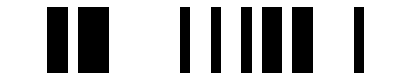

```mathematica
(* whole-VR ops ; implied mask = 16^^FFFF *)
copyVR[vr_]:=1*vr; (* Force copy with trivial arithmetic. *)
notVR[vr_]:=1-vr;
xorVRs[vr1_,vr2_]:=Mod[vr1+vr2,2];
andVRs[vr1_,vr2_]:=vr1*vr2;
orVRs[vr1_,vr2_]:=andVRs[vr1,vr2]+xorVRs[vr1,vr2];

(* Wordline ops exploit Mathematica's flexible broadcasting. *)
copyWordline=copyVR;
notWordline=notVR;
xorWordlines=xorVRs;
andWordlines=andVRs;
orWordlines=orVRs;

(* Always remember to add 1 to zero-based indices for Mathematica. *)
(* Forgetting to do so is a frequent cause of bugs. *)
(* If something isn't behaving as expected, look first at indices. *)

(* It's definitely possible to refactor these, abstracting over the function inside the 'Map' calls; seems overkill. *)

(* double-masked version *)
(* BELEX: vr1 = VR(0); vr1(destMask) <= vr2(srcMask) *)
copyVR[destMask_,srcMask_,vr_]:=
With[{dix=1+sectionListFromSectionMask[destMask],
six=1+sectionListFromSectionMask[srcMask]},
Assert[Length@dix===Length@six,"copyVR.double-masked"];
Module[{vrP=zeroVR[]},
Map[(vrP⟦dix⟦#⟧⟧=vr⟦six⟦#⟧⟧)&,Range[Length@dix]];
vrP]];

(* single-masked version *)
(* BELEX: vr1 = VR(0); vr1(mask) <= vr2(mask) *)
(* Could refactor this into call of double-masked version, but it ain't broke, so don't fix it. *)
copyVR[mask_,vr_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=vr⟦#⟧)&,indices];
vrP]];

(* See rows moving down one section *)
If[unitTesting,Module[{vr1=randomizedVR[],src,dest},
src=copyVR[16^^1111,vr1];
dest=copyVR[16^^2222,16^^1111,vr1];
echo[tinyPlot/@<|"vr1"->vr1,
(* single-masked *)
"src"->src,
(* double-masked *)
"dest"->dest|>];
Assert[dest⟦1+1⟧===src⟦1+0⟧===vr1⟦1+0⟧];
Assert[dest⟦1+5⟧===src⟦1+4⟧===vr1⟦1+4⟧];
Assert[dest⟦1+9⟧===src⟦1+8⟧===vr1⟦1+8⟧];
Assert[dest⟦1+13⟧===src⟦1+12⟧===vr1⟦1+12⟧];
(* Test andWordlines. *)
Assert[src⟦1+0⟧===andWordlines[src⟦1+0⟧,dest⟦1+1⟧]];
echo[tinyPlot[{src⟦1+0⟧}]];   ]];
```

```mathematica
(* single-masked version; no double-masked version for 'not' *)
(* BELEX: vr = VR(0); ~vr(mask); return vr *)
notVR[mask_,vr_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=1-vr⟦#⟧)&,indices];
vrP]];

(* double-masked version *)
(* BELEX: vr = 0; vr = vr1(m1) ^ vr2(m2); return vr *)
xorVRs[m1_,vr1_,m2_,vr2_]:=
With[{ix1=1+sectionListFromSectionMask[m1],
ix2=1+sectionListFromSectionMask[m2]},
Assert[Length@ix1===Length@ix2];
Module[{vrP=zeroVR[]},
Map[(vrP⟦ix1⟦#⟧⟧=Mod[vr1⟦ix1⟦#⟧⟧+vr2⟦ix2⟦#⟧⟧,2])&,Range[Length@ix1]];
vrP]];

(* single-masked version *)
(* BELEX: vr = 0; vr = vr1(mask) ^ vr2(mask); return vr *)
xorVRs[mask_,vr1_,vr2_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=Mod[vr1⟦#⟧+vr2⟦#⟧,2])&,indices];
vrP]];

(* See rows moving down one section *)
If[unitTesting,Module[{vr1=randomizedVR[],src,dest},
src=copyVR[16^^1111,vr1];
dest=copyVR[16^^2222,16^^1111,vr1];
echo[tinyPlot/@<|"vr1"->vr1,
(* single-masked *)
"src"->src,
(* double-masked *)
"dest"->dest|>];
Assert[dest⟦1+1⟧===src⟦1+0⟧===vr1⟦1+0⟧];
Assert[dest⟦1+5⟧===src⟦1+4⟧===vr1⟦1+4⟧];
Assert[dest⟦1+9⟧===src⟦1+8⟧===vr1⟦1+8⟧];
Assert[dest⟦1+13⟧===src⟦1+12⟧===vr1⟦1+12⟧];   ]];
```

<|vr1→-Graphics-,src→-Graphics-,dest→-Graphics-|>

```mathematica
(* double-masked version *)
(* BELEX: vr = 0; vr = vr1(m1) & vr2(m2); return vr *)
andVRs[m1_,vr1_,m2_,vr2_]:=
With[{ix1=1+sectionListFromSectionMask[m1],
ix2=1+sectionListFromSectionMask[m2]},
Assert[Length@ix1===Length@ix2];
Module[{vrP=zeroVR[]},
Map[(vrP⟦ix1⟦#⟧⟧=vr1⟦ix1⟦#⟧⟧*vr2⟦ix2⟦#⟧⟧)&,Range[Length@ix1]];
vrP]];

(* single-masked version *)
(* BELEX: vr = 0; vr = vr1(mask) & vr2(mask); return vr *)
andVRs[mask_,vr1_,vr2_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=vr1⟦#⟧*vr2⟦#⟧)&,indices];
vrP]];

(* double-masked version *)
(* BELEX: vr = 0; vr = vr1(m1) & vr2(m2); return vr *)
orVRs[m1_,vr1_,m2_,vr2_]:=
Module[{vrP=zeroVR[]},
vrP=andVRs[m1,vr1,m2,vr2]+xorVRs[m1,vr1,m2,vr2];
vrP];

(* single-masked version *)
(* BELEX: vr = 0; vr = vr1(mask) | vr2(mask); return vr *)
orVRs[mask_,vr1_,vr2_]:=
Module[{vrP=zeroVR[]},
vrP=andVRs[mask,vr1,vr2]+xorVRs[mask,vr1,vr2];
vrP];

If[unitTesting,
Module[{vr1,vr2,vr1c,vr2c,N=NSECTIONS*NPLATS,σOr,σAnd,σXor,eOr,eAnd,eXor,mOr,mAnd,mXor,sOr,sAnd,sXor,ninesOr,ninesAnd,ninesXor,kOr,kAnd,kXor},
vr1=randomizedVR[];
vr2=randomizedVR[];
vr1c=copyVR[vr1];
vr2c=copyVR[vr2];
eOr=3.N/4;σOr=Sqrt[3.N/16];
eAnd=N/4.;σAnd=Sqrt[3.N/16];
eXor=N/2.;σXor=Sqrt[N/4.];
mOr=N*Mean[1.Flatten@orVRs[vr1,vr2]];sOr=1. √N StandardDeviation[Flatten@orVRs[vr1,vr2]];
mAnd=N*Mean[1.Flatten@andVRs[vr1,vr2]];sAnd=1. √N StandardDeviation[Flatten@andVRs[vr1,vr2]];
mXor=N*Mean[1.Flatten@xorVRs[vr1,vr2]];sXor=1. √N StandardDeviation[Flatten@xorVRs[vr1,vr2]];
kOr=Abs[mOr-eOr]/σOr;
kAnd=Abs[mAnd-eAnd]/σAnd;
kXor=Abs[mXor-eXor]/σXor;
(* "nines" means "with this many nines of reliability, a random sample has a k number of sigmas less than the observed k_o number of sigmas of this sample." A small number of nines means that a small number of random samples are "better" than this one, that this event is not rare. A large number of nines means this is a rare event. Anything more than 2 nines means a 1/100 cumulative chance that this event is random; rare, but expected in more than 100 trials. *)
ninesOr=(0.47+0.42kOr)^2;Assert[ninesOr<2.0,"rare fluctuation in Or"];
ninesAnd=(0.47+0.42kAnd)^2;Assert[ninesAnd<2.0,"rare fluctuation in And"];
ninesXor=(0.47+0.42kXor)^2;Assert[ninesXor<2.0,"rare fluctuation in Xor"];
echo@<|"eOr"->eOr,"mOr"->mOr,"σOr"->σOr,"sOr"->sOr,"kOr"->kOr,"9sOr"->ninesOr|>;
echo@<|"eAnd"->eAnd,"mAnd"->mAnd,"σAnd"->σAnd,"sAnd"->sAnd,"kAnd"->kAnd,"9sAnd"->ninesAnd|>;
echo@<|"eXor"->eXor,"mXor"->mXor,"σXor"->σXor,"sXor"->sXor,"kXor"->kXor,"9sXor"->ninesXor|>;
echo@(tinyPlot/@<|"or"->orVRs[vr1,vr2],"and"->andVRs[vr1,vr2],"xor"->xorVRs[vr1,vr2]|>);
(* Assert no changes to originals. *)
Assert[vr1===vr1c];
Assert[vr2===vr2c];   ]];
```

<|eOr→384.,mOr→398.,σOr→9.79796,sOr→9.42288,kOr→1.42887,9sOr→1.14517|>

<|eAnd→128.,mAnd→138.,σAnd→9.79796,sAnd→10.05,kAnd→1.02062,9sAnd→0.807591|>

<|eXor→256.,mXor→260.,σXor→11.3137,sXor→11.3234,kXor→0.353553,9sXor→0.382533|>

<|or→-Graphics-,and→-Graphics-,xor→-Graphics-|>

#### Section.Subsection.Subsubsection Masked Ops into Left-Initialized Results

Updating arrays in-place is not convenient in Mathematica. Let’s model BELEX like vr1(mask) ^= vr2(mask) with Mathematica vr1 = xorVRsL[mask, vr1, vr2].

BELEX: vr1(m1) <= vr2(m2); return vr1
leaving unmasked bits as originally in vr1

BELEX: return ~vr(mask)
leaving unmasked bits alone

BELEX: vr1 <= vr1(m1) ^ vr2(m2); return vr1
also vr1(m1) ^= vr2(m2)
leaving unmasked bits as originally in vr1

BELEX: vr1 <= vr1(m1) & vr2(m2); return vr1
also vr1(m1) &= vr2(m2)
leaving unmasked bits as originally in vr1

BELEX: vr1 <= vr1(m1) | vr2(m2); return vr1
also vr1(m1) |= vr2(m2)
leaving unmasked bits as originally in vr1

```mathematica
(* double-masked version *)
(* BELEX: vr1(m1) <= vr2(m2) *)
(* leaving unmasked bits as originally in vr1 *)
copyVRsL[m1_,vr1_,m2_,vr2_]:=
With[{ix1=1+sectionListFromSectionMask[m1],
ix2=1+sectionListFromSectionMask[m2]},
Assert[Length@ix1===Length@ix2];
Module[{vrP=vr1},
Map[(vrP⟦ix1⟦#⟧⟧=vr2⟦ix2⟦#⟧⟧)&,Range[Length@ix1]];
vrP]];

If[unitTesting,
Module[{vr1=randomizedVR[],vr2=randomizedVR[],result},
result=copyVRsL[16^^3333,vr1,16^^CCCC,vr2];
Assert[result⟦1+0⟧===vr2⟦1+ 2⟧];
Assert[result⟦1+1⟧===vr2⟦1+ 3⟧];
Assert[result⟦1+2⟧===vr1⟦1+ 2⟧];
Assert[result⟦1+3⟧===vr1⟦1+ 3⟧];

Assert[result⟦1+4⟧===vr2⟦1+ 6⟧];
Assert[result⟦1+5⟧===vr2⟦1+ 7⟧];
Assert[result⟦1+6⟧===vr1⟦1+ 6⟧];
Assert[result⟦1+7⟧===vr1⟦1+ 7⟧];

Assert[result⟦1+8⟧===vr2⟦1+ 10⟧];
Assert[result⟦1+9⟧===vr2⟦1+ 11⟧];
Assert[result⟦1+10⟧===vr1⟦1+ 10⟧];
Assert[result⟦1+11⟧===vr1⟦1+ 11⟧];

Assert[result⟦1+12⟧===vr2⟦1+ 14⟧];
Assert[result⟦1+13⟧===vr2⟦1+ 15⟧];
Assert[result⟦1+14⟧===vr1⟦1+ 14⟧];
Assert[result⟦1+15⟧===vr1⟦1+ 15⟧];

echo[tinyPlot/@<|"vr1"->vr1,"vr2"->vr2,"res"->result|>];   ]];
```

<|vr1→-Graphics-,vr2→-Graphics-,res→-Graphics-|>

```mathematica
(* single-masked version *)
(* BELEX: vr1(mask) <= vr2(mask) *)
(* leaving unmasked bits as originally in vr1 *)
copyVRsL[mask_,vr1_,vr2_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=vr1},
Map[(vrP⟦#⟧=vr2⟦#⟧)&,indices];vrP]];

(* single-masked version; no double-masked version for 'not' *)
(* BELEX: return ~vr(mask), leaving unmasked bits alone *)
notVRL[mask_,vr_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=vr},
Map[(vrP⟦#⟧=1-vr⟦#⟧)&,indices];vrP]];

(* double-masked version *)
(* BELEX: vr=vr1; vr = vr1(m1) ^ vr2(m2); return vr *)
(* leaving unmasked bits as originally in vr1 *)
xorVRsL[m1_,vr1_,m2_,vr2_]:=
With[{ix1=1+sectionListFromSectionMask[m1],
ix2=1+sectionListFromSectionMask[m2]},
Assert[Length@ix1===Length@ix2];
Module[{vrP=vr1},
Map[(vrP⟦ix1⟦#⟧⟧=Mod[vr1⟦ix1⟦#⟧⟧+vr2⟦ix2⟦#⟧⟧,2])&,Range[Length@ix1]];
vrP]];

(* single-masked version *)
(* BELEX: vr=vr1; vr = vr1(mask) ^ vr2(mask); return vr *)
(* leaving unmasked bits as originally in vr1 *)
xorVRsL[mask_,vr1_,vr2_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=vr1},
Map[(vrP⟦#⟧=Mod[vr1⟦#⟧+vr2⟦#⟧,2])&,indices];
vrP]];

(* double-masked version *)
(* BELEX: vr=vr1; vr = vr1(m1) & vr2(m2); return vr *)
(* leaving unmasked bits as originally in vr1 *)
andVRsL[m1_,vr1_,m2_,vr2_]:=
With[{ix1=1+sectionListFromSectionMask[m1],
ix2=1+sectionListFromSectionMask[m2]},
Assert[Length@ix1===Length@ix2];
Module[{vrP=vr1},
Map[(vrP⟦ix1⟦#⟧⟧=vr1⟦ix1⟦#⟧⟧*vr2⟦ix2⟦#⟧⟧)&,Range[Length@ix1]];
vrP]];

If[unitTesting,
Module[{vr1=randomizedVR[],vr2=randomizedVR[],result},
result=andVRsL[16^^3333,vr1,16^^CCCC,vr2];
Assert[result⟦1+0⟧===andWordlines[vr1⟦1+0⟧,vr2⟦1+2⟧]];
Assert[result⟦1+1⟧===andWordlines[vr1⟦1+1⟧,vr2⟦1+3⟧]];
Assert[result⟦1+2⟧===andWordlines[vr1⟦1+2⟧,vr1⟦1+ 2⟧]];
Assert[result⟦1+3⟧===andWordlines[vr1⟦1+3⟧,vr1⟦1+ 3⟧]];

Assert[result⟦1+4⟧===andWordlines[vr1⟦1+4⟧,vr2⟦1+ 6⟧]];
Assert[result⟦1+5⟧===andWordlines[vr1⟦1+5⟧,vr2⟦1+ 7⟧]];
Assert[result⟦1+6⟧===andWordlines[vr1⟦1+6⟧,vr1⟦1+ 6⟧]];
Assert[result⟦1+7⟧===andWordlines[vr1⟦1+7⟧,vr1⟦1+ 7⟧]];

Assert[result⟦1+8⟧===andWordlines[vr1⟦1+8⟧,vr2⟦1+ 10⟧]];
Assert[result⟦1+9⟧===andWordlines[vr1⟦1+9⟧,vr2⟦1+ 11⟧]];
Assert[result⟦1+10⟧===andWordlines[vr1⟦1+10⟧,vr1⟦1+ 10⟧]];
Assert[result⟦1+11⟧===andWordlines[vr1⟦1+11⟧,vr1⟦1+ 11⟧]];

Assert[result⟦1+12⟧===andWordlines[vr1⟦1+12⟧,vr2⟦1+ 14⟧]];
Assert[result⟦1+13⟧===andWordlines[vr1⟦1+13⟧,vr2⟦1+ 15⟧]];
Assert[result⟦1+14⟧===andWordlines[vr1⟦1+14⟧,vr1⟦1+ 14⟧]];
Assert[result⟦1+15⟧===andWordlines[vr1⟦1+15⟧,vr1⟦1+ 15⟧]];

echo[tinyPlot/@<|"vr1"->vr1,"vr2"->vr2,"res"->result|>];   ]];
```

<|vr1→-Graphics-,vr2→-Graphics-,res→-Graphics-|>

```mathematica
(* single-masked version *)
(* BELEX: vr=vr1; vr = vr1(mask) & vr2(mask); return vr *)
(* leaving unmasked bits as originally in vr1 *)
andVRsL[mask_,vr1_,vr2_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Module[{vrP=vr1},
Map[(vrP⟦#⟧=vr1⟦#⟧*vr2⟦#⟧)&,indices];
vrP]];

If[unitTesting,Module[{vr1=vrFromImmediate[16^^fca3],vr2=vrFromImmediate[16^^f00f]},
echo[tinyPlot/@<|"x▴y"->vr1,"bggl"->vr2,"and2"->andVRs[16^^4444,vr1,vr2]|>];]]

(* double-masked version *)
(* BELEX: vr = 0; vr = vr1(m1) & vr2(m2); return vr *)
(* leaving unmasked bits as originally in vr1 *)
orVRsL[m1_,vr1_,m2_,vr2_]:=
Module[{vrP=vr1},
vrP=andVRs[m1,vr1,m2,vr2]+xorVRs[m1,vr1,m2,vr2];
vrP];

(* single-masked version *)
(* BELEX: vr=vr1; vr = vr1(mask) | vr2(mask); return vr *)
(* leaving unmasked bits as originally in vr1 *)
orVRsL[mask_,vr1_,vr2_]:=
Module[{vrP=vr1},
vrP=andVRs[mask,vr1,vr2]+xorVRs[mask,vr1,vr2];
vrP];

If[unitTesting,
Module[{vr1=randomizedVR[],vr2=randomizedVR[],vr1cp},
vr1cp=vr1;
echo[tinyPlot/@
<|"vr1"->vr1,"vr1cp"->vr1cp,"vr2"->vr2|>];
(* Verify no change-in-place. *)
copyVRsL[16^^0F0F,vr1,vr2];
copyVRsL[16^^F0F0,vr1,zeroVR[]];
Assert[vr1===vr1cp];
(* Verify copy on output. *)
vr11=copyVRsL[16^^0F0F,vr1,vr2];
vr12=copyVRsL[16^^F0F0,vr11,zeroVR[]];
echo[tinyPlot/@<|"vr11"->vr11,"vr12"->vr12,"vr2"->vr2,"vr1cp"->vr1cp|>];   ]];
```

<|x▴y→-Graphics-,bggl→-Graphics-,and2→-Graphics-|>

<|vr1→-Graphics-,vr1cp→-Graphics-,vr2→-Graphics-|>

<|vr11→-Graphics-,vr12→-Graphics-,vr2→-Graphics-,vr1cp→-Graphics-|>

#### Section.Subsection.Subsubsection Masked Comparison Ops

```mathematica
ClearAll[equalVRs];

(* double-masked version *)
equalVRs[m1_,vr1_,m2_,vr2_]:=
With[{ix1=1+sectionListFromSectionMask[m1],
ix2=1+sectionListFromSectionMask[m2]},
Assert[Length@ix1===Length@ix2];
Fold[(#1&&(vr1⟦ix1⟦#2⟧⟧===vr2⟦ix2⟦#2⟧⟧))&,True,Range[Length[ix1]]]];

(* single-masked version *)
equalVRs[mask_,vr1_,vr2_]:=
With[{indices=1+sectionListFromSectionMask[mask]},
Fold[(#1&&(vr1⟦#2⟧===vr2⟦#2⟧))&,True,indices]];

If[unitTesting,
Module[{vr1=randomizedVR[],vr2,vr1c,vr2c},
(* Modify this copy below. *)
vr2=copyVR[vr1];
Assert[equalVRs[16^^FFFF,vr1,vr2]];
(* Flip one bit in vr2. *)
vr2⟦4,19⟧=1-vr2⟦4,19⟧;
echo[tinyPlot/@<|"vr1"->vr1,"vr2"->vr2|>];
(* Assert (in)equalities on sections with a changed bit. *)
Assert[Not[equalVRs[16^^FFFF,vr1,vr2]]];
Assert[equalVRs[16^^FFF7,vr1,vr2]];
(* Exclude top 8 rows from XOR for vizualization (little-endian). *)
echo[tinyPlot@xorVRsL[16^^00ff,vr1,vr2]];   ]];
```

<|vr1→-Graphics-,vr2→-Graphics-|>

-Graphics-

### Section.Subsection GGL & BGGL

While it’s a machine register, GGL is semantically useful at the BELEX level, the level of user-written code. Its functionality is crucial for the GVML adder.

GGL has four rows called groups. Each group has the shape of a wordline or section, namely, a 1×NPLATS array of bits. We write GGL in all-caps. It is therefore a machine variable by our naming convention, and normally opaque to BELEX code. We write bggl for a system-supplied, user-visible, virtual VR that expands the four groups of GGL into 16 sections so as to have the shape of an ordinary BELEX VR variable. Group 0 of GGL corresponds to sections {0,1,2,3} of bggl, group 1 of GGL corresponds to rows {4,5,6,7} bggl and so forth. Sections {0,1,2,3} of bggl are always mutually equal; sections {4,5,6,7} of bggl are always mutually equal, and so forth. These facts are evident in the visualizations below.

Internally, bggl may cache bits in the hardware register GGL.

The following mechanization assumes that NSECTIONS === 16, thus the stride is 4.

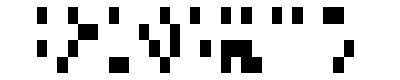
<|vr→-Graphics-,ggl→-Graphics-,bgglCall→-Graphics-,bgglCache→-Graphics-|>

```mathematica
ClearAll[gglInit,bggl, bgglFromGGL,toGGL];
Assert[Quotient[NSECTIONS,4]===4];
bggl[mask_,vrs_List]:=bgglFromGGL[toGGL[mask,vrs]];
bgglFromGGL[ggl_]:=Module[{group,result=zeroVR[],i,j},
For[i=0,i<NSECTIONS,i++,
For[j=0,j<NPLATS,j++,(* trog now; looking forward to TARTAN *)
group=Quotient[i,4];
result⟦1+i,1+j⟧=ggl⟦group+1,j+1⟧
]];result];
gglInit[]:=ConstantArray[1,{4,NPLATS}];
toGGL[mask_,vrs_List]:=
Module[{vr,ggl=gglInit[],bns=sectionListFromSectionMask[mask]},
Assert[0≤Length[vrs]≤3,"incorrectNumberOfVRs"];
vr=oneVR[];
vr=Fold[andVRs[mask,#1,#2]&,vr,vrs];
Module[{i,line},
For[i=0,i<4,i++,
For[line=0, line<4, line++,
(* Stride is 4. *)
With[{index=4i+line},
If[MemberQ[bns,index],
ggl⟦1+i⟧=andWordlines[ggl⟦1+i⟧,vr⟦1+index⟧]
]]]]];ggl];
If[unitTesting,
Module[{v=randomizedVR[],ggl,bgglCache},
ggl=toGGL[16^^3333,{v}];
(* Always remember to add one to zero-based indices in Mathematica. *)
(* Here (and very often below), we do it explicitly in the brackets. *)
Assert[ggl⟦1+0⟧===andWordlines[v⟦1+0⟧,v⟦1+1⟧]];
Assert[ggl⟦1+1⟧===andWordlines[v⟦1+4⟧,v⟦1+5⟧]];
Assert[ggl⟦1+2⟧===andWordlines[v⟦1+8⟧,v⟦1+9⟧]];
Assert[ggl⟦1+3⟧===andWordlines[v⟦1+12⟧,v⟦1+13⟧]];
bgglCache=bgglFromGGL[ggl];
Assert[bgglCache===bggl[16^^3333,{v}]];
echo@(tinyPlot/@<|"vr"->v,"ggl"->ggl,"bgglCall"->bggl[16^^3333,{v}],"bgglCache"->bgglCache|>);]]
```

### Section.Subsection GL & BGL

Let’s do for GL as we did for GGL. It’s easier because GL has only one wordline: its shape is 1×NPLATS. GL and bgl first becomes useful in Instruction 8.

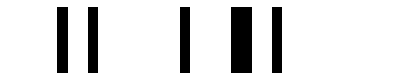
<|vr→-Graphics-,gl→-Graphics-,bglCall→-Graphics-,bglCache→-Graphics-|>

```mathematica
ClearAll[glInit,bgl, bglFromGL,toGL];
bgl[mask_,vrs_List]:=bglFromGL[toGL[mask,vrs]];
bglFromGL[gl_]:=Module[{result=zeroVR[],i,j},
For[i=0,i<NSECTIONS,i++,
For[j=0,j<NPLATS,j++,(* trog now; looking forward to TARTAN *)
result⟦1+i,1+j⟧=gl⟦1,j+1⟧
]];result];
glInit[]:=ConstantArray[1,{1,NPLATS}];
toGL[mask_,vrs_List]:=
Module[{vr,gl=glInit[],bns=sectionListFromSectionMask[mask]},
Assert[0≤Length[vrs]≤3,"incorrectNumberOfVRs"];
vr=oneVR[];
vr=Fold[andVRs[mask,#1,#2]&,vr,vrs];
Module[{line},
For[line=0, line<NSECTIONS, line++,
If[MemberQ[bns,line],
gl⟦1⟧=andWordlines[gl⟦1⟧,vr⟦1+line⟧]
]]];gl];
If[unitTesting,
Module[{v=randomizedVR[],gl,bglCache},
gl=toGL[16^^3,{v}];
(* Always remember to add one to zero-based indices in Mathematica. *)
(* Here (and very often below), we do it explicitly in the brackets. *)
Assert[gl⟦1+0⟧===andWordlines[v⟦1+0⟧,v⟦1+1⟧]];
bglCache=bglFromGL[gl];
Assert[bglCache===bgl[16^^3,{v}]];
echo@(tinyPlot/@<|"vr"->v,"gl"->gl,"bglCall"->bgl[16^^3,{v}],"bglCache"->bglCache|>);]]
```

### Section.Subsection Analysis (UNDONE)

This analysis is COMPLETED, but in a separate document, "belex-alpha-release-nnn.pdf," where "nnn" is a revision number (on revision 9 as of 5 August 2021).

```mathematica
@belex_apl
def add_u16_literal_sections(Belex, res: VR, x: VR, y: VR) -> None:
    x_xor_y = RN_REG_T0
    cout1 = RN_REG_T1
    flags = RN_REG_FLAGS
    C_FLAG = 0
    with apl_commands("instruction 1"):
        RL["0xFFFF"] <= x()
```

```mathematica
with apl_commands("instruction 2"):
        RL["0xFFFF"] ^= y()
        GGL["014589CD"] <= RL()
    with apl_commands("instruction 3"):
        x_xor_y["0xFFFF"] <= RL()
    with apl_commands("instruction 4"):
        cout1["048C"] <= RL()
        cout1["159D"] <= GGL()
        RL["26AE"] <= x_xor_y() & GGL()
        RL["014589CD"] <= x() & y()
    with apl_commands("instruction 5"):
        cout1["26AE"] <= RL()
        RL["37BF"] <= x_xor_y() & NRL()
        RL["159D"] |= x_xor_y() & NRL()
        RL["26AE"] <= x() & y()
    with apl_commands("instruction 6"):
        cout1["37BF"] <= RL()
        RL["37BF"] <= x() & y()
        RL["26AE"] |= x_xor_y() & NRL()
        GGL["0"] <= RL()
    with apl_commands("instruction 7"):
        RL["37BF"] |= x_xor_y() & NRL()
        GL["3"] <= RL()
        RL["0"] <= cout1()
    with apl_commands("instruction 8"):
        RL["4567"] |= cout1() & GL()
        GL["7"] <= RL()
        res["0"] <= RL()
    with apl_commands("instruction 9"):
        RL["89AB"] |= cout1() & GL()
        GL["B"] <= RL()
        RL["0"] <= GGL()
    with apl_commands("instruction 10"):
        RL["CDEF"] |= cout1() & GL()
        GL["F"] <= RL()
    with apl_commands("instruction 11"):
        # flags[f"0<<{C_FLAG}"] <= GL()  # proposed new syntax
        flags["0"] <= GL()
        # RL["~0"] <= x_xor_y() ^ NRL()  # proposed new syntax
        RL["0xFFFE"] <= x_xor_y() ^ NRL()
    with apl_commands("instruction 12"):
        # res["~0"] <= RL()  # proposed new syntax
        res["0xFFFE"] <= RL()
```

### Section.Subsection Instructions 1 through 3

Changed: RL_*, GGL_*, x▴y

Used: x, y

Note on the running example: to quickly find any failed Assertions, search the notebook for the word “failed.”

The first three instructions (bundles of parallel commands enclosed in curly braces) put x⊻y (x XOR y) into RL and then some sections of RL into GGL.

1.1 	FFFF 	:	RL = SB[x];
}{ 2.1	FFFF 	:	RL ^= SB[y];
   2.2 	3333 	:	GGL = RL;    	(* Safe 9.2 -- uses updated RL *)
}{ 3.1	FFFF 	:	SB[x⊻y] = RL; 	(* separate instruction, new RL *)

#### Section.Subsection.Subsubsection BELEX

-Graphics-

#### Section.Subsection.Subsubsection Running Example

51913

1340

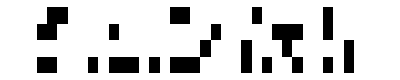
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-|>

```mathematica
ClearAll[i1thru3,g13,g4,g5,g6,g7,g8,g9,gA,gB,gC,gD,gE,gF];
i1thru3[machineAndBelexState_Association,x_,y_]:=
Module[{h=machineAndBelexState,
xvr=vrFromImmediate[x],yvr=vrFromImmediate[y](* weaker test *)},
(* a 32x stronger test *)
xvr=randomizedVR[];yvr=randomizedVR[];
(* BELEX variables in lower case; machine-state variables in upper case *)
h["x▴y"]=xorVRs[xvr,yvr]; (*instr 3*)
h["vx"]=xvr;
h["vy"]=yvr;
h["RL"]=h["x▴y"];
h["GGL"]=toGGL[m3333,{h["x▴y"]}];
(* User might create a variable to cache the results of call of bggl. *)
h["bgglCache"]=bggl[m3333,{h["x▴y"]}];
h["xy"]=andVRs[xvr,yvr];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,
echo[tinyPlot/@(g13=i1thru3[<||>,
echo@RandomInteger[{0,65535}],
echo@RandomInteger[{0,65535}]])];
Do[Assert[g13["GGL"]⟦1+i+0⟧===andWordlines[
g13["x▴y"]⟦1+4i+0⟧,
g13["x▴y"]⟦1+4i+1⟧],"2.2"],{i,0,3,1}]];
```

### Section.Subsection Instruction 4

All commands are compatible due to disjoint section masks.

Changed: c_("048C"), c_("159D"), RL_("048C"), RL_("159D"), RL_("26AE")

Used: RL_("048C"), GGL_0, (x▴y)_("26AE"), xy_("048C"), xy_("159D")

}{ 4.1	1111	:	SB[cout1] = RL;			(* change c_("048C") *)
   4.2	1111<<1	:	SB[cout1] = GGL;		(* change c_("159D") *)
   4.3	1111<<2	:	RL = SB[x⊻y] & GGL;		/* (CIN & x⊻y) */
   4.4	3333	:	RL = SB[x,y];			(* safe 9.1 write into 4.1 SB before read into RL *) 
   											/* CALC COUT0  */

#### Section.Subsection.Subsubsection BELEX

-Graphics-

#### Section.Subsection.Subsubsection Running Example

Break up the computation into a functional composition of sub-computations.

```mathematica
ClearAll[i4,i41,i42,i43,i44,g41,g42,g43];
i4=i44@*i43@*i42@*i41;
```

4.1:	c_("048C"):=(x▴y)_("048C")						subst RL from 2.1

```mathematica
i41[machineAndBelexState_Association]:=Module[{h=machineAndBelexState},
(* Assume initial contents of c don't matter. Take zeros via masked operation into a zero-initialized results. *)
(* 4.1 *)
(* user writes: Subscript[c, "048C"]:=Subscript[x▴y, "048C"] *)
h["c"]=copyVR[s048C@h["x▴y"]];(* single-masked, zero-initialized *)
(* POSTCONDITIONS *)
(* Check that RL (all sections) contains what we think it contains. 
This check supports the manual substitution of 4.1 from 2.1. *)
Assert[h["RL"]===h["x▴y"],"4.1a"];
(* Check that c:048C was loaded properly. *)
check4s[h["c"],h["x▴y"],0,"4.1b"];    
h(* Return modified machine and BELEX state. *)]; 
If[unitTesting,g41=i41[g13]];
```

4.2:	c_("159D"):=(x▴y)_("048C")&(x▴y)_("159D"), 			subst GGL from 2.2; explicit AND

```mathematica
i42[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t},
(* 4.2 PRECONDITIONS *)
(* Into sections 159D of c, copy sections 159D of x▴y and bggl (for a check; it's not BELEX). 
Leave the other sections of c alone. *)
(* Check contents of cached value of bggl. *)
Assert[h["bgglCache"]===bggl[m3333,{h["x▴y"]}]];
t=copyVRsL[s159D@h["c"],h["bgglCache"]];
(* single-masked, left-initialized, from double-masked, left-initialized, explicit AND *)
(* 4.2 *)
(* user writes: Subscript[c, "159D"]:=Subscript[x▴y, "048C"]&Subscript[x▴y, "159D"] *)
h["c"]=copyVRsL[s159D@h["c"],
andVRs[s159D@h["x▴y"],s048C@h["x▴y"]]];
(* POSTCONDITIONS *)
(* Check that the two ways of filling sections 159D of c are the same. *)
Assert[t===h["c"],"4.2"];
(* Check that c:048C is unchanged. Ditto c:26AE and c:37BF*)
check4s[h["c"],h["x▴y"],0,"4.2a0"];
check4s[h["c"],zeroVR[],2,"4.2a2"];
check4s[h["c"],zeroVR[],3,"4.2a3"];
(* Check that c:159D is loaded correctly. *)
Do[Assert[h["c"]⟦1+i+1⟧===andWordlines[
h["x▴y"]⟦1+i+0⟧,
h["x▴y"]⟦1+i+1⟧],"4.2a1"],{i,0,12,4}];    
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g42=i42[g41]];
```

4.3:	RL_("26AE"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")	NO BELEX: subst GGL from 2.2; commute

```mathematica
i43[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,u,w,x▴y,and=andWordlines},
x▴y=h["x▴y"];
(* 4.3 PRECONDITIONS *)(* Ensure m3333 bggl wordlines are as expected. *)
Assert[equalVRs[s26AE@h["bgglCache"],s048C@h["bgglCache"]],"4.3a"];
Do[Assert[h["bgglCache"]⟦1+i+2⟧(* bggl:26AE *)===and[
x▴y⟦1+i+0⟧(*048C*),
x▴y⟦1+i+1⟧(*159D*)],"4.3b"],{i,0,12,4}];
u=andVRs[s26AE@x▴y,h["bgglCache"]];(* zero-initialized *)
(* Test the u's use of bggl against manual substitution for bggl. *)
Do[Assert[u⟦1+i+2⟧(*26AE*)===and[and[
x▴y⟦1+i+0⟧(*048C*),
x▴y⟦1+i+1⟧(*159D*)],
x▴y⟦1+i+2⟧(*26AE*)],"4.3c2"],{i,0,12,4}];
check4s[u,zeroVR[],0,"4.3c0"];
check4s[u,zeroVR[],1,"4.3c1"];
check4s[u,zeroVR[],3,"4.3c3"];
(* 4.3 *)
(* Test the BELOPS expression for the substitution. *)
w=andVRs[s26AE@x▴y,s159D@andVRs[s159D@x▴y,s048C@x▴y]];
Assert[u===w,"4.3"];(* two different pathways to assert *)
Do[check4s[u,w,i,"4.3d"],{i,0,3,1}];
(* Would the user save this value in a variable? Yes. In 5.1, it's going into Subscript[c, "26AE"]. *)
(* The internal machination of caching it in RL is not visible to the BELEX programmer. *)
(* Preserve other contents of RL via single-masked, left-initialized copy. *)
h["RL"]=copyVRsL[s26AE@h["RL"],w];
(* POSTCONDITIONS *)
Do[Assert[h["RL"]⟦1+i+2⟧(* RL:26AE *)===and[and[
x▴y⟦1+i+0⟧,(* x▴y:048C *)
x▴y⟦1+i+1⟧],(* x▴y:159D *)
x▴y⟦1+i+2⟧],(* x▴y:26AE *)
"4.3rl2"],{i,0,12,4}];
(* Check that the rest of RL is unchanged from 3.1. *)
check4s[h["RL"],x▴y,0,"4.3rl0"];
check4s[h["RL"],x▴y,1,"4.3rl1"];
check4s[h["RL"],x▴y,3,"4.3rl3"];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g43=i43[g42]];
```

4.4:	RL_("014589CD"):=xy_("014589CD")		NO BELEX: SB[x,y] =def= x&y =def= xy

```mathematica
i44[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,and=andWordlines,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
h["RL"]=copyVRsL[s3333@h["RL"],xy];
(* POSTCONDITIONS *)
(* changes expected in rl every 4 starting at offsets 0 and 1. *)
check4s[h["RL"],xy,0,"4.4a0"];
check4s[h["RL"],xy,1,"4.4a1"];
(* offset 3 unchanged *)
check4s[h["RL"],x▴y,3,"4.4a3"];
(* check no changes also in RL:26AE *)
Do[Assert[h["RL"]⟦1+i+2⟧(* RL:26AE *)===and[and[
x▴y⟦1+i+0⟧,(* x▴y:048C *)
x▴y⟦1+i+1⟧],(* x▴y:159D *)
x▴y⟦1+i+2⟧],(* x▴y:26AE *)
"4.4a2"],{i,0,12,4}];    
h(* Return modified machine and BELEX state. *)];
(* Do the composed computation for all of instruction 4. *)
If[unitTesting,Module[{},g4=i4[g13];echo[tinyPlot/@g4];]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

### Section.Subsection Instruction 5

Changed: c_("26AE"), RL_("37BF"), RL_("159D"), RL_("26AE")

Used: RL_("26AE") (Section.Subsection safe to c_("26AE")), (x▴y)_("37BF"), RL_("26AE") (via NRL), RL_("159D") (by |=), (x▴y)_("159D"), RL_("048C") (via NRL), xy_("26AE")

}{ 5.1	1111<<2	:	SB[cout1] = RL;			(* 26AE: Safe 9.1: write SB before updating RL in 5.4*)
   5.2	1111<<3	:	RL = SB[x⊻y] & NRL;		/* 37BF: (CIN & x⊻y) */
   5.3	1111<<1	:	RL |= SB[x⊻y] & NRL;	/* 159D: (CIN & x⊻y) */
   5.4	1111<<2	:	RL = SB[x,y];			/* 26AE: CALC COUT0 */

#### Section.Subsection.Subsubsection BELEX

NRL semantics (example): NRL_("37BF")=RL_("26AE"). Just subtract 1 from each of NRL’s section bit-numbers and substitute RL for NRL.

5.1:	c_("26AE"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")				BELEX: subst RL from 4.3
No further BELEX in instruction 5: just storing intermediate values in RL
5.2:	RL_("37BF"):=(x▴y)_("37BF")&NRL_("37BF")						“equimask” expression
	RL_("37BF"):=(x▴y)_("37BF")&RL_("26AE")						NRL semantics
	RL_("37BF"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")&(x▴y)_("37BF")	RL from 4.3; commute; not BELEX
5.3:	RL_("159D"):=RL_("159D")|((x▴y)_("159D")&NRL_("159D"))
	RL_("159D"):=RL_("159D")|((x▴y)_("159D")&RL_("048C"))			NRL semantics
	RL_("159D"):=xy_("159D")|((x▴y)_("159D")&RL_("048C"))			RL_("159D") from 4.4
	RL_("159D"):=xy_("159D")|((x▴y)_("159D")&xy_("048C"))				RL_("048C") from 4.4
	RL_("159D"):=(xy_("159D")|(x▴y)_("159D"))&(xy_("159D")|xy_("048C"))	distrib to CNF; not BELEX
5.4:	RL_("26AE"):=xy_("26AE")								not BELEX

All “reads” into RL are compatible because their section masks are disjoint.

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[i5,i51,i52,i53,i54,g51,g52,g53];
i5=i54@*i53@*i52@*i51;
```

5.1:	c_("26AE"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")				subst RL from 4.3

```mathematica
i51[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,and=andWordlines,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
(* 5.1 *)
(* single-masked, left-initialized; this is the BELEX the user 
writes to save the value of the complex expression from 4.3. *)
(* user writes: Subscript[c, "26AE"]:=Subscript[x▴y, "048C"]&Subscript[x▴y, "159D"]&Subscript[x▴y, "26AE"] *)
h["c"]=copyVRsL[s26AE@h["c"],
andVRs[s26AE@x▴y,s159D@andVRs[s159D@x▴y,s048C@x▴y]]];
(* POSTCONDITIONS *)
(* Ensure no changes to c:048C. *)
check4s[h["c"],x▴y,0,"5.1a"];
(* Ensure no changes to c:159D from 4.2. *)
Do[Assert[h["c"]⟦1+i+1⟧===and[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],"5.1b"],{i,0,12,4}];
(* Ensure c:26AE is loaded with expected values. *)
Do[Assert[h["c"]⟦1+i+2⟧===and[and[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],
x▴y⟦1+i+2⟧],"5.1c"],{i,0,12,4}];
(* Ensure no changes to RL *)
check4s[h["RL"],xy,0,"5.1post0"];
check4s[h["RL"],xy,1,"5.1post1"];
check4s[h["RL"],x▴y,3,"5.1post3"];
Do[Assert[h["RL"]⟦1+i+2⟧(* rl:26AE *)===andWordlines[andWordlines[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],
x▴y⟦1+i+2⟧],"5.1post2"],{i,0,12,4}];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g51=i51[g4]];
```

No BELEX here, just loading machine state.

5.2:	RL_("37BF"):=(x▴y)_("37BF")&NRL_("37BF")						“equimask” expression
5.2.1	RL_("37BF"):=(x▴y)_("37BF")&RL_("26AE")						NRL semantics
5.2.2	RL_("37BF"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")&(x▴y)_("37BF")	RL from 4.3; commute; BELEX in 6.1

```mathematica
i52[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,v,xy,x▴y,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
(* 5.2.1 *)
t=andVRs[s37BF@x▴y,s26AE@h["RL"]];
(* 5.2.2: zero-initialized, right-to-left *)
u=andVRs[s37BF@x▴y,
s26AE@andVRs[s26AE@x▴y,
s159D@andVRs[s159D@x▴y,s048C@x▴y]]];
Assert[t===u,"5.2r2l"];
(* 5.2.2: zero-initialized, left-to-right *)
v=andVRs[s37BF@x▴y,
s26AE@andVRs[s26AE@x▴y,
(* only difference is equal by commutativity here *)
s048C@andVRs[s048C@x▴y,s159D@x▴y]]];
Assert[t===u===v,"5.2l2r"];
h["RL"]=copyVRsL[s37BF@h["RL"],u]; (* left-initialized *)
(* POSTCONDITIONS: no other changes to RL *)
check4s[h["RL"],xy,0,"5.1post0"];
check4s[h["RL"],xy,1,"5.1post1"];
Do[Assert[h["RL"]⟦1+i+2⟧(* rl:26AE *)===and[and[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],
x▴y⟦1+i+2⟧],"5.1post2"],{i,0,12,4}];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g52=i52[g51]];
```

No BELEX here; just loading machine state

5.3:	RL_("159D"):=RL_("159D")|((x▴y)_("159D")&NRL_("159D"))
5.3.1	RL_("159D"):=RL_("159D")|((x▴y)_("159D")&RL_("048C"))			NRL semantics
5.3.2	RL_("159D"):=xy_("159D")|((x▴y)_("159D")&RL_("048C"))			RL_("159D") from 4.4
5.3.3	RL_("159D"):=xy_("159D")|((x▴y)_("159D")&xy_("048C"))				RL_("048C") from 4.4
5.3.4	RL_("159D"):=(xy_("159D")|(x▴y)_("159D"))&(xy_("159D")|xy_("048C"))	distrib to CNF; usable in 6.3

```mathematica
i53[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,l,r,xy,x▴y,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
(* zero-initialized; 5.3.2 *)
t=orVRs[s159D@xy,andVRs[s159D@x▴y,s048C@h["RL"]]];
l=orVRs[s159D@xy,x▴y];(* 5.3.4, left disj *)
r=orVRs[s159D@xy,s048C@xy]; (* 5.3.4, right disj *)
(* 5.3.4: conjunctive normal form *)
u=andVRsL[s159D@l,r];
Assert[t===u,"5.3"];
h["RL"]=copyVRsL[s159D@h["RL"],u];
(* POSTCONDITIONS: no other changes to RL *)
check4s[h["RL"],xy,0,"5.3po0"];
check4s[h["RL"],andVRs[s37BF@x▴y,s26AE@h["RL"]],3,"5.3po3"];
Do[Assert[h["RL"]⟦1+i+2⟧(* rl:26AE *)===and[and[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],
x▴y⟦1+i+2⟧],"5.3po2"],{i,0,12,4}];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g53=i53[g52];
echo[tinyPlot/@g53];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

5.4	RL_("26AE"):=xy_("26AE")

```mathematica
i54[machineAndBelexState_Association]:=Module[{h=machineAndBelexState},
h["RL"]=copyVRsL[s26AE@h["RL"],h["xy"]];
(* At this point, after so many unit tests, we are confident that the rest of RL is not disturbed *)
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g5=i5[g4];
echo[tinyPlot/@g5];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

### Section.Subsection Instruction 6

Changed: c_("37BF"), RL_("26AE"), RL_("37BF"), GGL_("0") (Section.Subsection safe from RL_0)

Used: RL_("37BF"), xy_("37BF"), RL_("26AE") (by |=), (x▴y)_("26AE"), RL_("159D") (via NRL), RL_0

}{ 6.1	1111<<3	:	SB[cout1] = RL;			(* 37BF: Safe 9.1: Write SB before updating RL *)
   6.2	1111<<3	:	RL = SB[x,y];			(* 37BF *)
   6.3	1111<<2	:	RL |= SB[x⊻y] & NRL;	/* 26AE: (CIN & x⊻y) = COUT? */
   6.4	0001	:	GGL = RL;

#### Section.Subsection.Subsubsection BELEX

6.1:	c_("37BF"):=RL_("37BF")
	c_("37BF"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")&(x▴y)_("37BF")		RL_("37BF") from 5.2
6.2:	RL_("37BF"):=xy_("37BF")		Section 9.1: safe write (6.1) before read RL_("37BF") (6.2)
6.3:	RL_("26AE"):=RL_("26AE")|((x▴y)_("26AE")&NRL_("26AE"))
	RL_("26AE"):=xy_("26AE")|((x▴y)_("26AE")&NRL_("26AE"))				from 5.4
	RL_("26AE"):=xy_("26AE")|((x▴y)_("26AE")&RL_("159D"))				NRL semantics
	RL_("26AE"):=(xy_("26AE")|(x▴y)_("26AE"))&(xy_("26AE")|RL_("159D"))		distrib
	RL_("26AE"):=(xy_("26AE")|(x▴y)_("26AE"))
&(xy_("26AE")|((xy_("159D")|(x▴y)_("159D"))&(xy_("159D")|xy_("048C"))))	RL_("159D") from 5.3	
	RL_("26AE"):=(xy_("26AE")|(x▴y)_("26AE"))
&(xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
&(xy_("26AE")|xy_("159D")|xy_("048C"))						distrib		
6.4	GGL_0:=RL_0
	GGL_0:=xy_0										from 4.4
	GGL_123=(x▴y)_("48C")&(x▴y)_("59D")							from 2.2 (check unchanged)

Notice loose symmetry between 5.3 and 6.3.

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[i6,i61,i62,i63,i64,g61,g62,g63];
i6=i64@*i63@*i62@*i61;
```

6.1:	c_("37BF"):=RL_("37BF")
	c_("37BF"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")&(x▴y)_("37BF")		BELEX; subst RL_("37BF") from 5.2

```mathematica
i61[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,v,w,l,r,x▴y,and=andWordlines},
x▴y=h["x▴y"];
t=copyVR[s37BF@h["RL"]];(* zero-initialized, only for checking *)
(* 6.1 *)
(* user writes: Subscript[c, "37BF"]:=Subscript[x▴y, "048C"]&Subscript[x▴y, "159D"]&Subscript[x▴y, "26AE"]&Subscript[x▴y, "37BF"] *)
(* explicit computation, right-to-left *)
u=andVRs[s37BF@x▴y,(* same masks *)
s26AE@andVRs[s26AE@x▴y,(* same masks *)
s159D@andVRs[s159D@x▴y,s048C@x▴y]]];
(* explicit computation, left-to-right (probable compiler path) *)
v=andVRs[s37BF@x▴y,
s26AE@andVRs[s26AE@x▴y,
(* only difference is here, equal by Commutative Law *)
s048C@andVRs[s048C@x▴y,s159D@x▴y]]];
Assert[t===u===v,"6.1"];
h["c"]=copyVRsL[s37BF@h["c"],u];
(* POSTCONDITIONS *)
check4s[h["c"],x▴y,0,"6.1c0"];(* c:048C *)
Do[Assert[h["c"]⟦1+i+1⟧===andWordlines[ (* c:159D *)
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],"6.1c1"],{i,0,12,4}];
Do[Assert[h["c"]⟦1+i+2⟧(* c:26AE *)===and[and[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],
x▴y⟦1+i+2⟧],"6.1c2"],{i,0,12,4}];
Do[Assert[h["c"]⟦1+i+3⟧(* c:37BF *)===and[and[and[
x▴y⟦1+i+0⟧,
x▴y⟦1+i+1⟧],
x▴y⟦1+i+2⟧],
x▴y⟦1+i+3⟧],"6.1c3"],{i,0,12,4}];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g61=i61[g5];
echo[tinyPlot/@g61];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

6.2:	RL_("37BF"):=xy_("37BF")		Section 9.1: safe write (6.1) before read RL_("37BF") (6.2)

Load group 3 of RL on the left-hand side of 6.2 for future use, but we will substitute RL out later.

```mathematica
i62[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,u,l,r,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
h["RL"]=copyVRsL[s37BF@h["RL"],xy];
(* POSTCONDITIONS: no other changes to RL *)
(* rl:048C, from 4.4 *)
check4s[h["RL"],xy,0,"6.2p0"];
(* rl:159D, from 5.3 *)
l=orVRs[s159D@xy,x▴y];
r=orVRs[s159D@xy,s048C@xy];
u=andVRsL[s159D@l,r];
check4s[h["RL"],u,1,"6.2p1"];
(* rl:26AE, from 5.4 *)
check4s[h["RL"],xy,2,"6.2p2"];
(* rl:37BF, from 6.2 (here) *)
check4s[h["RL"],xy,3,"6.2p3"];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g62=i62[g61];
echo[tinyPlot/@g62];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

6.3:	RL_("26AE"):=RL_("26AE")|((x▴y)_("26AE")&NRL_("26AE"))
	RL_("26AE"):=xy_("26AE")|((x▴y)_("26AE")&NRL_("26AE"))				from 5.4
6.3.1	RL_("26AE"):=xy_("26AE")|((x▴y)_("26AE")&RL_("159D"))				NRL semantics
6.3.2	RL_("26AE"):=l:(xy_("26AE")|(x▴y)_("26AE"))&(xy_("26AE")|RL_("159D"))		distrib
6.3.3	RL_("26AE"):=l:(xy_("26AE")|(x▴y)_("26AE"))
&(xy_("26AE")|r_3:(r_1:(xy_("159D")|(x▴y)_("159D"))&r_2:(xy_("159D")|xy_("048C"))))	RL_("159D") from 5.3	
6.3.4	RL_("26AE"):=l:(xy_("26AE")|(x▴y)_("26AE"))
&t_1:(xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
&t_2:(xy_("26AE")|xy_("159D")|xy_("048C"))						distrib

```mathematica
i63[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,t1,t2,t3,u,v,l,l1,r,r1,r2,r3,r4,q1,q2,q3,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
(* 6.3.1: Subscript[RL, "26AE"]:=Subscript[xy, "26AE"]|(Subscript[x▴y, "26AE"]&Subscript[RL, "159D"]) *)
t=orVRs[s26AE@xy,andVRs[s26AE@x▴y,s159D@h["RL"]]];
(* 6.3.2 *)
l=orVRs[s26AE@xy,x▴y];
r=orVRs[s26AE@xy,s159D@h["RL"]];
u=andVRs[l,r];
Assert[t===u,"6.3.1_2"];
(* 6.3.3 *)
r1=orVRs[s159D@xy,x▴y];
r2=orVRs[s159D@xy,s048C@xy];
r3=andVRs[s159D@r1,r2];
Assert[equalVRs[s159D@r3,h["RL"]],"6.3.3a"];
r4=andVRs[l,orVRs[s26AE@xy,s159D@r3]];
Assert[r4===t,"6.3.3b"];
(* 6.3.4 *)
t1=orVRs[s26AE@xy,s159D@r1];
t2=orVRs[s26AE@xy,s159D@r2];
t3=andVRs[l,andVRs[t1,t2]];
(* 6.3.4, expanded *)
q1=orVRs[s26AE@xy,x▴y];Assert[q1===l,"q1=l"];
q2=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,x▴y]];Assert[q2===t1,"q2=t1"];
q3=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,s048C@xy]];Assert[q3===t2,"q3=t2"];
v=andVRs[q1,andVRs[q2,q3]];
Assert[t3===u===r4===t===v,"6.3.1_4"];
h["RL"]=copyVRsL[s26AE@h["RL"],v];
Assert[equalVRs[s26AE@h["RL"],v]];
(* POSTCONDITIONS: no other changes to RL *)
(* RL:048C, from 4.4 *)
check4s[h["RL"],xy,0,"6.2p0"];
(* RL:159D, from 5.3 *)
l=orVRs[s159D@xy,x▴y];
r=orVRs[s159D@xy,s048C@xy];
u=andVRsL[m159D,l,r];
check4s[h["RL"],u,1,"6.2p1"];
(* RL:37BF, from 6.2 (here) *)
check4s[h["RL"],xy,3,"6.2p3"];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g63=i63[g62];
echo[tinyPlot/@g63];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

6.4	GGL_0:=RL_0
6.4.1	GGL_0:=xy_0										from 4.4
6.4.2	GGL_123=(x▴y)_("48C")&(x▴y)_("59D")							from 2.2 (check unchanged)

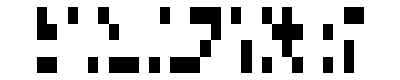
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

```mathematica
i64[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,x▴y,and=andWordlines},
x▴y=h["x▴y"];
t=h["GGL"];(* copy all lines *)
t⟦1+0⟧=h["xy"]⟦1+0⟧;(* overwrite line 0 (don't forget Mathematica's "1" *)
h["GGL"]=t;(* copy back *)
h["bgglCache"]=bgglFromGGL[t];(* where will we need this? *)
Do[Assert[h["GGL"]⟦1+i⟧===and[x▴y⟦1+4i⟧,x▴y⟦1+4i+1⟧]],{i,1,3,1}];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g6=i6[g5];
echo[tinyPlot/@g6];]
```

### Section.Subsection Instruction 7

Changed: RL_("37BF"), GL (9.2 safe from RL_3), RL_0

Used: RL_("37BF") (by |=), (x▴y)_("159D","26AE","37BF"), RL_("26AE") (via NRL), RL_3, (x▴y)_0, xy_*

}{ 7.1	1111<<3	:	RL |= SB[x⊻y] & NRL;	/* (CIN & x⊻y) */
   7.2	0001<<3	:	GL = RL;				(* Safe 9.2, update RL first *)
   7.3	0001	:	RL = SB[cout1];

#### Section.Subsection.Subsubsection BELEX

7.1:	RL_("37BF"):=RL_("37BF")|((x▴y)_("37BF")&NRL_("37BF"))
	RL_("37BF"):=RL_("37BF")|((x▴y)_("37BF")&RL_("26AE"))		NRL semantics
	RL_("37BF"):=xy_("37BF")|((x▴y)_("37BF")&RL_("26AE"))			from 6.2
	RL_("37BF"):=xy_("37BF")|(x▴y)_("37BF") 
r_1: &(xy_("26AE")|(x▴y)_("26AE"))
r_2:&(xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
r_3:&(xy_("26AE")|xy_("159D")|xy_("048C"))				from 6.3
	RL_("37BF"):=
q_0: (xy_("37BF")|(x▴y)_("37BF")) 
q_1: &(xy_("37BF")|xy_("26AE")|(x▴y)_("26AE"))
q_2: &(xy_("37BF")|xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
q_3: &(xy_("37BF")|xy_("26AE")|xy_("159D")|xy_("048C"))		distrib
7.2: 	GL:=RL_3									9.2: load RL_3 before loading GL
	GL:=
(xy_3|(x▴y)_3) 
&(xy_3|xy_2|(x▴y)_2)
&(xy_3|xy_2|xy_1|(x▴y)_1)
&(xy_3|xy_2|xy_1|xy_0)						from 6.3
7.3:	RL_0:=c_0

Notice loose symmetry to 6.3 and 5.3.

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[i7,i71,i72,i73,g71,g72,g7];
i7=i73@*i72@*i71;
```

7.1:	RL_("37BF"):=RL_("37BF")|((x▴y)_("37BF")&NRL_("37BF"))
7.1.1	RL_("37BF"):=RL_("37BF")|((x▴y)_("37BF")&RL_("26AE"))		NRL semantics
7.1.2	RL_("37BF"):=xy_("37BF")|((x▴y)_("37BF")&RL_("26AE"))			from 6.2
7.1.3	RL_("37BF"):=xy_("37BF")|(x▴y)_("37BF") 
r_1: &(xy_("26AE")|(x▴y)_("26AE"))
r_2:&(xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
r_3:&(xy_("26AE")|xy_("159D")|xy_("048C"))				from 6.3
7.1.4	RL_("37BF"):=
q_0: (xy_("37BF")|(x▴y)_("37BF")) 
q_1: &(xy_("37BF")|xy_("26AE")|(x▴y)_("26AE"))
q_2: &(xy_("37BF")|xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
q_3: &(xy_("37BF")|xy_("26AE")|xy_("159D")|xy_("048C"))		distrib

```mathematica
i71[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,l,r,t,u,v,r1,r2,r3,q0,q1,q2,q3,xy,x▴y,or=orWordlines,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
(* 7.1.1: Subscript[RL, "37BF"]:=Subscript[RL, "37BF"]|(Subscript[x▴y, "37BF"]&Subscript[RL, "26AE"]) *)
t=orVRs[s37BF@h["RL"],andVRs[s37BF@h["x▴y"],s26AE@h["RL"]]];
(* 7.1.3: eliminating RL from right-hand side *)
r1=orVRs[s26AE@xy,x▴y];
r2=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,x▴y]];
r3=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,s048C@xy]];
u=orVRs[s37BF@xy,andVRs[s37BF@x▴y,s26AE@andVRs[r1,andVRs[r2,r3]]]];
Assert[t===u,"7.1.3"];
(* 7.1.4: testing distributive law *)
q0=orVRs[s37BF@xy,x▴y];
q1=orVRs[s37BF@xy,s26AE@orVRs[s26AE@xy,x▴y]];
q2=orVRs[s37BF@xy,s26AE@orVRs[s26AE@xy,s159D@orVRs[s159D@xy,x▴y]]];
q3=orVRs[s37BF@xy,s26AE@orVRs[s26AE@xy,s159D@orVRs[s159D@xy,s048C@xy]]];
v=andVRs[q0,andVRs[q1,andVRs[q2,q3]]];
Assert[v===andVRs[andVRs[andVRs[q0,q1],q2],q3],"commut"];
Assert[t===u===v,"7.1.4"];
h["RL"]=copyVRsL[s37BF@h["RL"],v];
(* Test line 3, which is needed later. *)
Module[{qn0,qn1,qn2,qn3,vn},
qn0=or[xy⟦1+3⟧,x▴y⟦1+3⟧];
qn1=or[or[xy⟦1+3⟧,xy⟦1+2⟧],x▴y⟦1+2⟧];
qn2=or[or[or[xy⟦1+3⟧,xy⟦1+2⟧],xy⟦1+1⟧],x▴y⟦1+1⟧];
qn3=or[or[or[xy⟦1+3⟧,xy⟦1+2⟧],xy⟦1+1⟧],xy⟦1+0⟧];
vn=and[and[and[qn0,qn1],qn2],qn3];
Assert[q0⟦1+3⟧===qn0,"7.4.1.0"];
Assert[q1⟦1+3⟧===qn1,"7.4.1.1"];
Assert[q2⟦1+3⟧===qn2,"7.4.1.2"];
Assert[q3⟦1+3⟧===qn3,"7.4.1.3"];
Assert[h["RL"]⟦1+3⟧===vn,"7.1.4a"]];
(* POSTCONDITIONS: no other changes to RL *)
(* RL:048C, from 4.4 *)
check4s[h["RL"],xy,0,"7.1p0"];
(* RL:159D, from 5.3 *)
l=orVRs[s159D@xy,x▴y];
r=orVRs[s159D@xy,s048C@xy];
u=andVRsL[m159D,l,r];
check4s[h["RL"],u,1,"7.1p1"];
(* RL:26AE *)
Assert[equalVRs[s26AE@h["RL"],andVRs[r1,andVRs[r2,r3]]],"7.1p2"];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g71=i71[g6];
echo[tinyPlot/@g71];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-|>

7.2: 	GL:=RL_3				9.2: load RL_3 before loading GL
	GL:=
(xy_3|(x▴y)_3) 
&(xy_3|xy_2|(x▴y)_2)
&(xy_3|xy_2|xy_1|(x▴y)_1)
&(xy_3|xy_2|xy_1|xy_0)

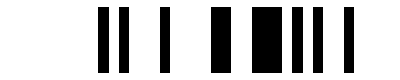
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-|>

```mathematica
i72[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,l,r,t,u,v,w,r1,r2,r3,xy,x▴y,or=orWordlines,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
h["GL"]={h["RL"]⟦1+3⟧};
t={Module[{q0,q1,q2,q3},
q0=or[xy⟦1+3⟧,x▴y⟦1+3⟧];
q1=or[or[xy⟦1+3⟧,xy⟦1+2⟧],x▴y⟦1+2⟧];
q2=or[or[or[xy⟦1+3⟧,xy⟦1+2⟧],xy⟦1+1⟧],x▴y⟦1+1⟧];
q3=or[or[or[xy⟦1+3⟧,xy⟦1+2⟧],xy⟦1+1⟧],xy⟦1+0⟧];
and[and[and[q0,q1],q2],q3]]};
Assert[t===h["GL"]==={h["RL"]⟦1+3⟧}];
(* POSTCONDITIONS: no changes to RL *)
(* RL:048C, from 4.4 *)
check4s[h["RL"],xy,0,"7.1p0"];
(* rl:159D, from 5.3 *)
l=orVRs[s159D@xy,x▴y];
r=orVRs[s159D@xy,s048C@xy];
u=andVRsL[m159D,l,r];
check4s[h["RL"],u,1,"7.1p1"];
(* rl:26AE *)
r1=orVRs[s26AE@xy,x▴y];
r2=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,x▴y]];
r3=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,s048C@xy]];
Assert[equalVRs[s26AE@h["RL"],andVRs[r1,andVRs[r2,r3]]],"7.2p2"];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g72=i72[g71];
echo[tinyPlot/@g72];]
```

7.3:	RL_0:=c_0

```mathematica
i73[machineAndBelexState_Association]:=
Module[{h=machineAndBelexState,l,r,t,u,v,w,r1,r2,r3,q0,q1,q2,q3,q4,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
v=h["RL"];
v⟦1+0⟧=h["c"]⟦1+0⟧;
h["RL"]=v;
(* POSTCONDITIONS: no other changes to RL *)
Assert[h["c"]⟦1+0⟧===h["RL"]⟦1+0⟧,"7.3p0"];
(* rl:48C, from 4.4 *)
Do[Assert[v⟦1+i⟧===h["RL"]⟦1+i⟧,"7.3p4"],{i,4,12,4}];
(* rl:159D, from 5.3 *)
l=orVRs[s159D@xy,x▴y];
r=orVRs[s159D@xy,s048C@xy];
u=andVRsL[m159D,l,r];
check4s[h["RL"],u,1,"7.1p1"];
(* rl:26AE *)
r1=orVRs[s26AE@xy,x▴y];
r2=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,x▴y]];
r3=orVRs[s26AE@xy,s159D@orVRs[s159D@xy,s048C@xy]];
Assert[equalVRs[s26AE@h["RL"],andVRs[r1,andVRs[r2,r3]]],"7.2p2"];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g7=i7[g6];
echo[tinyPlot/@g7];]
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-|>

### Section.Subsection Instruction 8

Changed: RL_("4567"), GL (9.2 safe from new RL_7), RL_0, r_0 (r is the final result)

Used: c_("4567"), RL_("4567") (by |=), RL_3 (via GL),RL_7, RL_0

}{ 8.1	000F<<4	:	RL |= SB[cout1] & GL;	(* Safe 9.2 Read into RL before broadcast *)
   8.2	0001<<7	:	GL = RL;				(* Safe 9.2 --- uses new RL *)
   8.3	0001	:	SB[res] = RL;

#### Section.Subsection.Subsubsection BELEX

8.1:	RL_("4567"):=RL_("4567")|(c_("4567")&GL)
	RL_("4567"):=RL_("4567")|(c_("4567")&RL_("3"))			from 7.2
		where RL_3=
q_0: (xy_3|(x▴y)_3) 
q_1: &(xy_3|xy_2|(x▴y)_2)
q_2: &(xy_3|xy_2|xy_1|(x▴y)_1)
q_3: &(xy_3|xy_2|xy_1|xy_0)			from 7.1.4
	RL_4 from 4.4, RL_5 from 5.3, RL_6 from 6.3, oldRL_7 from 7.1
8.2: 	GL:=RL_7|(c_7&RL_3)								use the new RL					
8.3:	r_0:=RL_("0")=c_("0")						from 7.3

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[i8,i81,i82,i83,g81,g82,g8];
i8=i83@*i82@*i81;
```

The following function deliver old values of RL given a subscript.

```mathematica
ClearAll[rlLine];
(* all using conjunctive normal forms from their respective instructions *)
rlLine[h_,k_]:=Module[{q0,q1,q2,q3,xy,x▴y,or=orWordlines,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
Which[
k===3,
q0=or[xy⟦1+3⟧,x▴y⟦1+3⟧];
q1=or[or[xy⟦1+3⟧,xy⟦1+2⟧],x▴y⟦1+2⟧];
q2=or[or[or[xy⟦1+3⟧,xy⟦1+2⟧],xy⟦1+1⟧],x▴y⟦1+1⟧];
q3=or[or[or[xy⟦1+3⟧,xy⟦1+2⟧],xy⟦1+1⟧],xy⟦1+0⟧];
and[and[and[q0,q1],q2],q3],
k===4,
xy⟦1+4⟧,
k===5,
q0=or[xy⟦1+5⟧,x▴y⟦1+5⟧];
q1=or[xy⟦1+5⟧,xy⟦1+4⟧];
and[q0,q1],
k===6,
q0=or[xy⟦1+6⟧,x▴y⟦1+6⟧];
q1=or[or[xy⟦1+6⟧,xy⟦1+5⟧],x▴y⟦1+5⟧];
q2=or[or[xy⟦1+6⟧,xy⟦1+5⟧],xy⟦1+4⟧];
and[and[q0,q1],q2],
k===7,
q0=or[xy⟦1+7⟧,x▴y⟦1+7⟧];
q1=or[or[xy⟦1+7⟧,xy⟦1+6⟧],x▴y⟦1+6⟧];
q2=or[or[or[xy⟦1+7⟧,xy⟦1+6⟧],xy⟦1+5⟧],x▴y⟦1+5⟧];
q3=or[or[or[xy⟦1+7⟧,xy⟦1+6⟧],xy⟦1+5⟧],xy⟦1+4⟧];
and[and[and[q0,q1],q2],q3],
k===8,
xy⟦1+8⟧,
k===9,
q0=or[xy⟦1+9⟧,x▴y⟦1+9⟧];
q1=or[xy⟦1+9⟧,xy⟦1+8⟧];
and[q0,q1],
k===10,
q0=or[xy⟦1+10⟧,x▴y⟦1+10⟧];
q1=or[or[xy⟦1+10⟧,xy⟦1+9⟧],x▴y⟦1+9⟧];
q2=or[or[xy⟦1+10⟧,xy⟦1+9⟧],xy⟦1+8⟧];
and[and[q0,q1],q2],
k===11,
q0=or[xy⟦1+11⟧,x▴y⟦1+11⟧];
q1=or[or[xy⟦1+11⟧,xy⟦1+10⟧],x▴y⟦1+10⟧];
q2=or[or[or[xy⟦1+11⟧,xy⟦1+10⟧],xy⟦1+9⟧],x▴y⟦1+9⟧];
q3=or[or[or[xy⟦1+11⟧,xy⟦1+10⟧],xy⟦1+9⟧],xy⟦1+8⟧];
and[and[and[q0,q1],q2],q3],
k===12,
xy⟦1+12⟧,
k===13,
q0=or[xy⟦1+13⟧,x▴y⟦1+13⟧];
q1=or[xy⟦1+13⟧,xy⟦1+12⟧];
and[q0,q1],
k===14,
q0=or[xy⟦1+14⟧,x▴y⟦1+14⟧];
q1=or[or[xy⟦1+14⟧,xy⟦1+13⟧],x▴y⟦1+13⟧];
q2=or[or[xy⟦1+14⟧,xy⟦1+13⟧],xy⟦1+12⟧];
and[and[q0,q1],q2],
k===15,
q0=or[xy⟦1+15⟧,x▴y⟦1+15⟧];
q1=or[or[xy⟦1+15⟧,xy⟦1+14⟧],x▴y⟦1+14⟧];
q2=or[or[or[xy⟦1+15⟧,xy⟦1+14⟧],xy⟦1+13⟧],x▴y⟦1+13⟧];
q3=or[or[or[xy⟦1+15⟧,xy⟦1+14⟧],xy⟦1+13⟧],xy⟦1+12⟧];
and[and[and[q0,q1],q2],q3],
True,Assert[False]]];
```

8.1:	RL_("4567"):=RL_("4567")|(c_("4567")&GL)
	RL_("4567"):=RL_("4567")|(c_("4567")&RL_3)			from 7.2
		where RL_3=
q_0: (xy_3|(x▴y)_3) 
q_1: &(xy_3|xy_2|(x▴y)_2)
q_2: &(xy_3|xy_2|xy_1|(x▴y)_1)
q_3: &(xy_3|xy_2|xy_1|xy_0)			call RL_3 “v” in the BELEX
	RL_4 from 4, RL_5 from 5, RL_6 from 6, oldRL_7 from 7 (see “rlLine”)

```mathematica
i81[machineAndBelexState_Association]:=
Module[{h=machineAndBelexState,t,v,w,c,q,p,oldRl3modded,m,rl3,rl4,rl5,rl6,rl7,or=orWordlines,and=andWordlines},
c=h["c"];
(* Subscript[RL, "4567"]:=Subscript[RL, "4567"]|(Subscript[c, "4567"]&GL) *)
t=copyVRsL[s4567@h["RL"],orVRs[s4567@h["RL"],andVRs[s4567@c,bglFromGL[h["GL"]]]]];
(* check oldRl3===t *)
v=rl3=rlLine[h,3];Assert[v===h["RL"]⟦1+3⟧,"8.1.rl3"];
w=rl7=rlLine[h,7];Assert[w===h["RL"]⟦1+7⟧,"8.1.rl7"];
q=rl6=rlLine[h,6];Assert[q===h["RL"]⟦1+6⟧,"8.1.rl6"];
p=rl5=rlLine[h,5];Assert[p===h["RL"]⟦1+5⟧,"8.1.rl5"];
m=rl4=rlLine[h,4];Assert[m===h["RL"]⟦1+4⟧,"8.1.rl4"];
h["oldRL"]=copyVR[h["RL"]];(* save old for testing *)
oldRl3modded=copyVR[h["RL"]];(* Initialize, then modify. *)
oldRl3modded⟦1+4⟧=or[rl4,and[c⟦1+4⟧,rl3]];
oldRl3modded⟦1+5⟧=or[rl5,and[c⟦1+5⟧,rl3]];
oldRl3modded⟦1+6⟧=or[rl6,and[c⟦1+6⟧,rl3]];
oldRl3modded⟦1+7⟧=or[rl7,and[c⟦1+7⟧,rl3]];
Assert[and[c⟦1+7⟧,m]===zeroWordline[]||r⟦1+7⟧=!=h["RL"]⟦1+7⟧,"8.1pre0"];
Assert[oldRl3modded===t,"8.1"];
h["RL"]=copyVR[t];
(* looking forward to Instruction 9 *)
Assert[h["RL"]⟦1+11⟧===rlLine[h,11]];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g81=i81[g7];
echo[tinyPlot/@g81]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-|>

8.2: 	GL:=RL_7=
(xy_7|(x▴y)_7)
& (xy_7|xy_6|(x▴y)_6)
&(xy_7|xy_6|xy_5|(x▴y)_5)
&(xy_7|xy_6|xy_5|xy_4)|(c_7&RL_3)		use the new RL_7

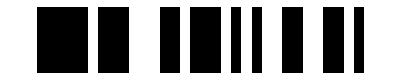
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-|>

```mathematica
i82[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,oldRl7,newRl7,oldRl3,or=orWordlines,and=andWordlines},
oldRl7=rlLine[h,7];
oldRl3=rlLine[h,3];
newRl7=or[oldRl7,and[h["c"]⟦1+7⟧,oldRl3]];
Assert[newRl7===h["RL"]⟦1+7⟧];
h["GL"]={h["RL"]⟦1+7⟧};
h["bglCache"]=bglFromGL[h["GL"]];
(* looking forward to Instruction 9 *)
Assert[h["RL"]⟦1+11⟧===rlLine[h,11]];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g82=i82[g81];
echo[tinyPlot/@g82]];
```

8.3:	r_0:=RL_0=c_0							from 7.3

```mathematica
i83[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,v},
v=zeroVR[];
v⟦1+0⟧=h["c"]⟦1+0⟧;
h["res"]=v;
(* looking forward to Instruction 9 *)
Assert[h["RL"]⟦1+11⟧===rlLine[h,11]];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g8=i8[g7];
echo[tinyPlot/@g8]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

### Section.Subsection Instruction 9

Changed: RL_("89AB"), GL, RL_("0")

Used: c_("89AB"), RL_("89AB") (by |=), GL, RL_("B"), GGL

}{ 9.1	000F<<8		:	RL |= SB[cout1] & GL;
   9.2	0001<<11	:	GL = RL;
   9.3	0001		:	RL = GGL;

#### Section.Subsection.Subsubsection BELEX

9.1:	RL_("89AB"):=RL_("89AB")|(c_("89AB")&GL)
	RL_("89AB"):=RL_("89AB")|(c_("89AB")&RL_7)				from 
		where RL_7=
(xy_7|(x▴y)_7)
& (xy_7|xy_6|(x▴y)_6)
&(xy_7|xy_6|xy_5|(x▴y)_5)
&(xy_7|xy_6|xy_5|xy_4)|(c_7&RL_3)			from 8.3
	RL_8 from 4.4, RL_9 from 5.3, RL_A from 6.3, RL_B from 7.1
9.2: 	GL:=RL_B=
(xy_B|(x▴y)_B)
& (xy_B|xy_A|(x▴y)_A)
&(xy_B|xy_A|xy_9|(x▴y)_9)
&(xy_B|xy_A|xy_9|xy_8)|(c_B&newRL_7)			use the new RL_B, RL_7
9.3:	RL_0:=GGL_0=xy_0							from 7.3

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[i9,i91,i92,i93,g91,g92,g9];
i9=i93@*i92@*i91;
```

9.1:	RL_("89AB"):=RL_("89AB")|(c_("89AB")&GL)
	RL_("89AB"):=RL_("89AB")|(c_("89AB")&RL_7)	
		where RL_7=
(xy_7|(x▴y)_7)
& (xy_7|xy_6|(x▴y)_6)
&(xy_7|xy_6|xy_5|(x▴y)_5)
&(xy_7|xy_6|xy_5|xy_4)|(c_7&RL_3)		from 8.3
	RL_8 from 4.4, RL_9 from 5.3, RL_A from 6.3, RL_B from 7.1

```mathematica
i91[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,v,w,r,q,p,m,c,rl3,rl7,rl8,rl9,rlA,rlB,or=orWordlines,and=andWordlines},
c=h["c"];
(* Subscript[RL, "89AB"]:=Subscript[RL, "89AB"]|(Subscript[c, "89AB"]&GL) *)
t=copyVRsL[s89AB@h["RL"],orVRs[s89AB@h["RL"],andVRs[s89AB@c,bglFromGL[h["GL"]]]]];
(* independent calculation from first principles *)
v=rl8=rlLine[h,8];Assert[v===h["RL"]⟦1+8⟧,"9.1.rl8"];
w=rl9=rlLine[h,9];Assert[w===h["RL"]⟦1+9⟧,"9.1.rl9"];
q=rlA=rlLine[h,10];Assert[q===h["RL"]⟦1+10⟧,"9.1.rlA"];
p=rlB=rlLine[h,11];Assert[p===h["RL"]⟦1+11⟧,"9.1.rlB"];
rl7=rlLine[h,7];(* rl was changed; rlLine computes old *)
rl3=rlLine[h,3];
m=or[rl7,and[c⟦1+7⟧,rl3]];
Assert[m===h["RL"]⟦1+7⟧,"9.1.rl7"];
Assert[{m}===h["GL"],"9.1.gl"];
r=copyVR[h["RL"]];
r⟦1+8⟧=or[rl8,and[c⟦1+8⟧,m]];
r⟦1+9⟧=or[rl9,and[c⟦1+9⟧,m]];
r⟦1+10⟧=or[rlA,and[c⟦1+10⟧,m]];
r⟦1+11⟧=or[rlB,and[c⟦1+11⟧,m]];
Assert[and[c⟦1+11⟧,m]===zeroWordline[]||r⟦1+11⟧=!=h["RL"]⟦1+11⟧,"9.1pre0"];
Assert[t===r,"9.1.tr"];
h["RL"]=copyVR[t];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g91=i91[g8];
echo[tinyPlot/@g91]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

9.2: 	GL:=RL_B=
(xy_B|(x▴y)_B)
& (xy_B|xy_A|(x▴y)_A)
&(xy_B|xy_A|xy_9|(x▴y)_9)
&(xy_B|xy_A|xy_9|xy_9)|(c_B&RL_7)9.2, use new RL

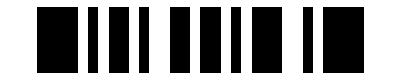
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

```mathematica
i92[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,or=orWordlines,and=andWordlines},
Assert[h["RL"]⟦1+11⟧===or[
rlLine[h,11],and[h["c"]⟦1+11⟧,h["RL"]⟦1+7⟧]],"9.2"];
h["GL"]={h["RL"]⟦1+16^^B⟧};
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g92=i92[g91];
echo[tinyPlot/@g92]];
```

9.3:	RL_0:=GGL_0=xy_0						from 7.3

```mathematica
i93[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,v},
Assert[h["GGL"]⟦1+0⟧===h["xy"]⟦1+0⟧,"9.3"];
v=h["RL"];
v⟦1+0⟧=h["GGL"]⟦1+0⟧;
h["RL"]=v;
h(* Return modified machine and BELEX state. *)];
If[unitTesting,g9=i9[g8];
echo[tinyPlot/@g9]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

### Section.Subsection Instruction 10

Changed: RL_("CDEF"), GL

Used: RL_("CDEF") (by |=), c_("CDEF"), GL, RL_("F")

}{ 10.1	000F<<12	:	RL |= SB[cout1] & GL;
   10.2 0001<<15	:	GL = RL;

#### Section.Subsection.Subsubsection BELEX

10.1:	RL_("CDEF"):=RL_("CDEF")|(c_("CDEF")&GL)
	RL_("CDEF"):=RL_("CDEF")|(c_("CDEF")&RL_B)			from 9.2 
		where RL_B=
(xy_B|(x▴y)_B)
& (xy_B|xy_A|(x▴y)_A)
&(xy_B|xy_A|xy_9|(x▴y)_9)
&(xy_B|xy_A|xy_9|xy_8)|(c_B&RL_7)	from 9.1
	RL_("8") from 4.4, RL_("9") from 5.3, RL_("A") from 6.3, RL_("B") from 7.1
10.2:	GL:=RL_F=
(xy_F|(x▴y)_F)
& (xy_F|xy_E|(x▴y)_E)
&(xy_B|xy_A|xy_9|(x▴y)_9)
&(xy_B|xy_A|xy_9|xy_8)|(c_F&RL_7)

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[iA,iA1,iA2,gA1,gA2,gA];
iA=iA2@*iA1;
```

10.1:	RL_("CDEF"):=RL_("CDEF")|(c_("CDEF")&GL)
	RL_("CDEF"):=RL_("CDEF")|(c_("CDEF")&RL_B)			from 9.2 
		where RL_B=
(xy_B|(x▴y)_B)
& (xy_B|xy_A|(x▴y)_A)
&(xy_B|xy_A|xy_9|(x▴y)_9)
&(xy_B|xy_A|xy_9|xy_8)|(c_B&RL_7)	from 9.1
	RL_8 from 4.4, RL_9 from 5.3, RL_B from 6.3, RL_B from 7.1

```mathematica
iA1[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,v,w,q,p,r,m,c,rlB,rlC,rlD,rlE,rlF,or=orWordlines,and=andWordlines},
c=h["c"];
(* Subscript[RL, "CDEF"]:=Subscript[RL, "CDEF"]|(Subscript[c, "CDEF"]&GL) *)
t=copyVRsL[sCDEF@h["RL"],orVRs[sCDEF@h["RL"],andVRs[sCDEF@c,bglFromGL[h["GL"]]]]];
(* independent calculation from first principles *)
v=rlC=rlLine[h,12];Assert[v===h["RL"]⟦1+12⟧,"10.1.rlC"];
w=rlD=rlLine[h,13];Assert[w===h["RL"]⟦1+13⟧,"10.1.rlD"];
q=rlE=rlLine[h,14];Assert[q===h["RL"]⟦1+14⟧,"10.1.rlE"];
p=rlF=rlLine[h,15];Assert[p===h["RL"]⟦1+15⟧,"10.1.rlF"];
rlB=rlLine[h,11];(* rl was changed; rlLine computes old *)
m=or[rlB,and[c⟦1+11⟧,h["RL"]⟦1+7⟧]];
Assert[m===h["RL"]⟦1+11⟧,"10.1.rlB"];
Assert[{m}===h["GL"],"9.1.gl"];
r=copyVR[h["RL"]];
r⟦1+12⟧=orWordlines[rlC,andWordlines[c⟦1+12⟧,m]];
r⟦1+13⟧=orWordlines[rlD,andWordlines[c⟦1+13⟧,m]];
r⟦1+14⟧=orWordlines[rlE,andWordlines[c⟦1+14⟧,m]];
r⟦1+15⟧=orWordlines[rlF,andWordlines[c⟦1+15⟧,m]];
Assert[t===r,"10.1.tr"];
h["RL"]=copyVR[t];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,gA1=iA1[g9];
echo[tinyPlot/@gA1]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

10.2:	GL:=RL_F=
(xy_F|(x▴y)_F)
& (xy_F|xy_E|(x▴y)_E)
&(xy_F|xy_E|xy_D|(x▴y)_D)
&(xy_F|xy_E|xy_D|xy_C)|(c_F&RL_B)

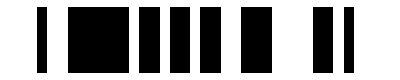
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

```mathematica
iA2[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,or=orWordlines,and=andWordlines},
Assert[h["RL"]⟦1+15⟧===or[
rlLine[h,15],and[h["c"]⟦1+15⟧,h["RL"]⟦1+11⟧]],"10.2"];
h["GL"]={h["RL"]⟦1+16^^F⟧};
h(* Return modified machine and BELEX state. *)];
If[unitTesting,
gA2=iA2[gA1];
gA=iA[g9];
Assert[gA2===gA];
echo[tinyPlot/@gA]];
```

### Section.Subsection Instruction 11

Changed:

Used:

}{ 11.2	0001 << C_FLAG	:	SB[RN_REG_FLAGS] = GL; (* carry-out for chaining *)
   11.3 ~0001			:	RL = SB[x_xor_y] ^ NRL;

#### Section.Subsection.Subsubsection BELEX

TODO: Ignore the C_FLAG command.

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[iB,iB1,iB2,gB1,gB2,gB];
iB=iB2@*iB1;
```

```mathematica
iB1=Identity;
```

```mathematica
iB2[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,or=orWordlines,and=andWordlines},
h["RL"]=copyVRsL[sFFFE@h["RL"],xorVRs[sFFFE@h["x▴y"],s7FFF@h["RL"]]];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,
gB=iB[gA];
echo[tinyPlot/@gB]];
```

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

### Section.Subsection Instruction 12

Changed:

Used:

}{ 12.4	~0001	:	SB[res] = RL;

#### Section.Subsection.Subsubsection BELEX

#### Section.Subsection.Subsubsection Running Example

```mathematica
ClearAll[iC];
```

```mathematica
iC[machineAndBelexState_Association]:=
Module[{h=machineAndBelexState,t,u,w,base=10,or=orWordlines,and=andWordlines},
t=h["res"]=copyVRsL[mFFFE,h["res"],h["RL"]];
echo@BaseForm[immediatesFromVr[h["vx"]],base];
echo@BaseForm[immediatesFromVr[h["vy"]],base];
u=Mod[immediatesFromVr[h["vx"]]+immediatesFromVr[h["vy"]],2^16];
echo@BaseForm[u,base];
echo@BaseForm[immediatesFromVr[t],base];
w=u-immediatesFromVr[t];
echo@BaseForm[w,base];
Assert[w===zeroWordline[]];
h(* Return modified machine and BELEX state. *)];
If[unitTesting,
gC=iC[gB];
echo[tinyPlot/@gC]];
```

{48577,9720,20368,48361,62418,55840,37589,27890,52475,25181,43338,39873,26573,15409,3490,22263,65243,23007,17854,7809,62076,62159,19549,23450,35013,31878,15896,45338,53109,20120,56687,31895}

{50425,23943,22483,46149,27474,26401,62429,40259,30206,21584,35680,41768,26467,51694,64837,40981,64881,46955,5171,5003,33138,32388,62855,39718,25589,32891,39796,30666,15050,10166,10791,30071}

{33466,33663,42851,28974,24356,16705,34482,2613,17145,46765,13482,16105,53040,1567,2791,63244,64588,4426,23025,12812,29678,29011,16868,63168,60602,64769,55692,10468,2623,30286,1942,61966}

{33466,33663,42851,28974,24356,16705,34482,2613,17145,46765,13482,16105,53040,1567,2791,63244,64588,4426,23025,12812,29678,29011,16868,63168,60602,64769,55692,10468,2623,30286,1942,61966}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,xy→-Graphics-,c→-Graphics-,GL→-Graphics-,oldRL→-Graphics-,bglCache→-Graphics-,res→-Graphics-|>

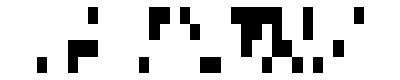
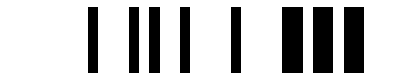
<|x▴y→-Graphics-,vx→-Graphics-,vy→-Graphics-,RL→-Graphics-,GGL→-Graphics-,bgglCache→-Graphics-,c→-Graphics-,GL→-Graphics-,bglCache→-Graphics-,xy→-Graphics-,res→-Graphics-|>

```mathematica
ClearAll[gResMax,gRes,gLabels,gResi,gResiLoad,gShow];
gResMax=26;
gRes=ConstantArray[
<|"RL"->tinyPlot@zeroVR[],"c"->tinyPlot@zeroVR[],
"bggl"->tinyPlot@zeroVR[],"bgl"->tinyPlot@zeroVR[],
"res"->tinyPlot@zeroVR[]|>,
gResMax];
gLabels=ConstantArray["",gResMax];
gResi=1;
gResiLoad[h_]:=Module[{g},
g=gRes⟦gResi⟧;
g["c"]=tinyPlot@h["c"];
g["RL"]=tinyPlot@h["RL"];
g["bggl"]=tinyPlot@h["bgglCache"];
g["bgl"]=tinyPlot@h["bglCache"];
g["res"]=tinyPlot@h["res"];
gRes⟦gResi⟧=g;
gResi++;
h];
gShow[i_]:=Grid[{
{gLabels⟦i⟧,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{gRes⟦i⟧["c"],gRes⟦i⟧["RL"],gRes⟦i⟧["bggl"],gRes⟦i⟧["bgl"],gRes⟦i⟧["res"]},
{Subscript[carry, i],Subscript[rtemp, i],Subscript[ggl, i],Subscript[gl, i],Subscript[result, i]}
},Alignment->{{Left,Left,Left,Left},{Center,Center,Center,Center},{Center,Center,Center,Center}}];
ClearAll[i1thru3,g13,g4,g5,g6,g7,g8,g9,gA,gB,gC,gD,gE,gF];
i1thru3[machineAndBelexState_Association,x_,y_]:=
Module[{h=machineAndBelexState,
xvr=vrFromImmediate[x],yvr=vrFromImmediate[y](* weaker test *)},
(* a 32x stronger test *)
xvr=randomizedVR[];yvr=randomizedVR[];
(* BELEX variables in lower case; machine-state variables in upper case *)
h["x▴y"]=xorVRs[xvr,yvr]; (*instr 3*)
h["vx"]=xvr;
h["vy"]=yvr;
h["RL"]=h["x▴y"];
h["GGL"]=toGGL[m3333,{h["x▴y"]}];
(* User might create a variable to cache the results of call of bggl. *)
h["bgglCache"]=bggl[m3333,{h["x▴y"]}];
h["c"]=zeroVR[];
h["GL"]=glInit[];
h["bglCache"]=bglFromGL[h["GL"]];
h["xy"]=andVRs[xvr,yvr];
h["res"]=zeroVR[];
gResi=1;
gLabels⟦gResi⟧="instructions 1-3
[ missing section annotations imply 0xFFFF ]

ggl_0 <= (x▴y)_0 & (x▴y)_1
ggl_1 <= (x▴y)_4 & (x▴y)_5
ggl_2 <= (x▴y)_8 & (x▴y)_9
ggl_3 <= (x▴y)_C & (x▴y)_D
r <= x▴y";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,
g13=i1thru3[<||>,RandomInteger[{0,65535}],RandomInteger[{0,65535}]];];
ClearAll[i4,i41,i42,i43,i44,g41,g42,g43];i4=i44@*i43@*i42@*i41;
i41[machineAndBelexState_Association]:=Module[{h=machineAndBelexState},
(* user writes: Subscript[c, "048C"]:=Subscript[x▴y, "048C"] *)
h["c"]=copyVR[s048C@h["x▴y"]];(* single-masked, zero-initialized *)
gLabels⟦gResi⟧="instruction 4, command 1
[ subscript string is section-number list, not mask ]
[ missing section annotations are inferred from left-hand side ]
c_(<048C>) <= x_(<048C>)(▴y)_(<048C>)
c_(<048C>) <= (x▴y)_(<048C>)
c_(<048C>) <= (x▴y)_(<048C>) 

c_(<048C>) <= x▴y";
gResiLoad@h(* Return modified machine and BELEX state. *)]; 
If[unitTesting,g41=i41[g13]];
i42[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t},
(* user writes: Subscript[c, "159D"]:=Subscript[x▴y, "048C"]&Subscript[x▴y, "159D"] *)
h["c"]=copyVRsL[s159D@h["c"],
andVRs[s159D@h["x▴y"],s048C@h["x▴y"]]];
gLabels⟦gResi⟧="instruction 4, command 2
[ equivalent syntactic alternatives ]
c_(<159D>) <=  x_(<048C>)▴y     & x_(<159D>)▴y
c_(<159D>) <=  x_(<048C>)(▴y)_(<048C>)  & x_(<159D>)(▴y)_(<159D>)
c_(<159D>) <= (x▴y)_(<048C>)    & (x▴y)_(<159D>) 
c_(<159D>) <=  (x▴y)_(<048C>)     &  (x▴y)_(<159D>)
c_(<159D>) <=  x_(<048C>)(▴y)_(<048C>)  & (x▴y)_(<159D>)
c_(<159D>) <=  (x▴y)_(<048C>) & x▴y // preferred";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g42=i42[g41]];
i43[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,u,w,x▴y,and=andWordlines},
x▴y=h["x▴y"];
u=andVRs[s26AE@x▴y,h["bgglCache"]];(* zero-initialized *)
h["RL"]=copyVRsL[s26AE@h["RL"],u];
gLabels⟦gResi⟧="instruction 4, command 3
[ missing section annotations are inferred ]

r_(<26AE>) <= (x▴y)_(<26AE>) & ggl_0
r_(<26AE>) <= x▴y & ggl_0
[ inlining ]

r_(<26AE>) <= (x▴y)_(<048C>) & (x▴y)_(<159D>) & (x▴y)_(<26AE>)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g43=i43[g42]];
i44[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,and=andWordlines,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
h["RL"]=copyVRsL[s3333@h["RL"],xy];
gLabels⟦gResi⟧="instruction 4, command 4
[ missing sections annotations are inferred ]
r(0x3333) <= x(0x3333) & y(0x3333) 
r(0x3333) <= (x&y)(0x3333), etc. 
r_(<048C>) <= (x&y)_(<048C>); r_(<159D>) <= (x&y)_(<159D>)
r(0x3333) <= x&y

r_(<014589CD>) <= (x&y)_(<014589CD>) // preferred";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,Module[{},g4=i44[g43](*;echo[tinyPlot/@g4];*)]];
ClearAll[i5,i51,i52,i53,i54,g51,g52,g53];i5=i54@*i53@*i52@*i51;
i51[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,and=andWordlines,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
(* user writes: Subscript[c, "26AE"]:=Subscript[x▴y, "048C"]&Subscript[x▴y, "159D"]&Subscript[x▴y, "26AE"] *)
h["c"]=copyVRsL[s26AE@h["c"],
andVRs[s26AE@x▴y,s159D@andVRs[s159D@x▴y,s048C@x▴y]]];
gLabels⟦gResi⟧="instruction 5, command 1
[ first sighting of CNF (Conjunctive Normal Form) ]


c_(<26AE>) <= r_(<26AE>)
[ inline from instr 4, cmd 3 ]

c_(<26AE>) <= (x▴y)_(<048C>) & (x▴y)_(<159D>) & (x▴y)_(<26AE>)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g51=i51[g4]];
i52[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,v,xy,x▴y,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
t=andVRs[s37BF@x▴y,s26AE@h["RL"]];
h["RL"]=copyVRsL[s37BF@h["RL"],t]; (* left-initialized *)
gLabels⟦gResi⟧="instruction 5, command 2



r_(<37BF>) <= (x▴y)_(<37BF>) & r_(<26AE>)
[ inline from instr4, cmd 3 ]

r_(<37BF>) <= (x▴y)_(<048C>) & (x▴y)_(<159D>) & (x▴y)_(<26AE>) & (x▴y)_(<37BF>)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g52=i52[g51]];
i53[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,l,r,xy,x▴y,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
t=orVRs[s159D@xy,andVRs[s159D@x▴y,s048C@h["RL"]]];
h["RL"]=copyVRsL[s159D@h["RL"],t];
gLabels⟦gResi⟧="instruction 5, command 3

r_(<159D>) |= (x▴y)_(<159D>) & r_(<048C>)
[ inline from instr 4, cmd 4 ]
r_(<159D>) <= x&y_(<159D>) | (x▴y)_(<159D>) & (x&y)_(<048C>)
[ rearrange to Conjunctive Normal Form ]

r_(<159D>) <= (x&y_(<159D>) | (x▴y)_(<159D>)) & (x&y_(<159D>) | x&y_(<048C>))";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g53=i53[g52](*;echo[tinyPlot/@g53];*)];
i54[machineAndBelexState_Association]:=Module[{h=machineAndBelexState},
h["RL"]=copyVRsL[s26AE@h["RL"],h["xy"]];
gLabels⟦gResi⟧="instruction 5, command 4






r_(<26AE>) <= x&y_(<26AE>)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g5=i54[g53](*;echo[tinyPlot/@g5];*)];
ClearAll[i6,i61,i62,i63,i64,g61,g62,g63];i6=i64@*i63@*i62@*i61;
i61[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,v,w,l,r,x▴y,and=andWordlines},
x▴y=h["x▴y"];
t=copyVR[s37BF@h["RL"]];(* zero-initialized, only for checking *)
h["c"]=copyVRsL[s37BF@h["c"],t];
gLabels⟦gResi⟧="instruction 6, command 1



c_(<37BF>) <= r_(<37BF>) 
[ inline from instr 5, cmd 2 ]

c_(<37BF>) <= (x▴y)_(<048C>) & (x▴y)_(<159D>) & (x▴y)_(<26AE>) & (x▴y)_(<37BF>)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g61=i61[g5](*;echo[tinyPlot/@g61];*)];
i62[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,u,l,r,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
h["RL"]=copyVRsL[s37BF@h["RL"],xy];
gLabels⟦gResi⟧="instruction 6, command 2




[ xy is short for x&y ]

r_(<37BF>) <= xy_(<37BF>)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g62=i62[g61](*;echo[tinyPlot/@g62];*)];
i63[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,t1,t2,t3,u,v,l,l1,r,r1,r2,r3,r4,q1,q2,q3,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
(* 6.3.1: Subscript[RL, "26AE"]:=Subscript[xy, "26AE"]|(Subscript[x▴y, "26AE"]&Subscript[RL, "159D"]) *)
t=orVRs[s26AE@xy,andVRs[s26AE@x▴y,s159D@h["RL"]]];
h["RL"]=copyVRsL[s26AE@h["RL"],t];
gLabels⟦gResi⟧="instruction 6, command 3




r_(<26AE>) <= (xy_(<26AE>)|(x▴y)_(<26AE>))
       & (xy_(<26AE>)|xy_(<159D>)|(x▴y)_(<159D>))
       & (xy_(<26AE>)|xy_(<159D>)|xy_(<048c>))";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g63=i63[g62](*;echo[tinyPlot/@g63];*)];
i64[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,x▴y,and=andWordlines},
x▴y=h["x▴y"];
t=h["GGL"];(* copy all lines *)
t⟦1+0⟧=h["xy"]⟦1+0⟧;(* overwrite line 0 (don't forget Mathematica's "1" *)
h["GGL"]=t;(* copy back *)
h["bgglCache"]=bgglFromGGL[t];(* where will we need this? *)
gLabels⟦gResi⟧="instruction 6, command 4



[ check unchanged ]
assert ggl_(<123>) == (x▴y)_(<48C>) & (x▴y)_(<59D>)

ggl_0 <= r_0 = xy_0";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g6=i64[g63](*;echo[tinyPlot/@g6];*)];
ClearAll[i7,i71,i72,i73,g71,g72,g7];i7=i73@*i72@*i71;
i71[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,l,r,t,u,v,r1,r2,r3,q0,q1,q2,q3,xy,x▴y,or=orWordlines,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
(* 7.1.1: Subscript[RL, "37BF"]:=Subscript[RL, "37BF"]|(Subscript[x▴y, "37BF"]&Subscript[RL, "26AE"]) *)
t=orVRs[s37BF@h["RL"],andVRs[s37BF@h["x▴y"],s26AE@h["RL"]]];
h["RL"]=copyVRsL[s37BF@h["RL"],t];
gLabels⟦gResi⟧="instruction 7, command 1
[ inlining all intermediates to show structure ]


r_(<37BF>) <= (xy_(<37BF>)|(x▴y)_(<37BF>)) 
       & (xy_(<37BF>)|xy_(<26AE>)|(x▴y)_(<26AE>))
       & (xy_(<37BF>)|xy_(<26AE>)|xy_(<159D>)|(x▴y)_(<159D>))
       & (xy_(<37BF>)|xy_(<26AE>)|xy_(<159D>)|xy_(<048C>))";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g71=i71[g6](*;echo[tinyPlot/@g71];*)];
i72[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,l,r,t,u,v,w,r1,r2,r3,xy,x▴y,or=orWordlines,and=andWordlines},
xy=h["xy"];x▴y=h["x▴y"];
h["GL"]={h["RL"]⟦1+3⟧};
h["bglCache"]=bglFromGL[h["GL"]];
gLabels⟦gResi⟧="instruction 7, command 2


gl <= verify(r_3 == 
      (xy_3|(x▴y)_3)
    & (xy_3|xy_2|(x▴y)_2)
    & (xy_3|xy_2|xy_1|(x▴y)_1)
    & (xy_3|xy_2|xy_1|xy_0))";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g72=i72[g71](*;echo[tinyPlot/@g72];*)];
i73[machineAndBelexState_Association]:=
Module[{h=machineAndBelexState,l,r,t,u,v,w,r1,r2,r3,q0,q1,q2,q3,q4,xy,x▴y},
xy=h["xy"];x▴y=h["x▴y"];
v=h["RL"];
v⟦1+0⟧=h["c"]⟦1+0⟧;
h["RL"]=v;
gLabels⟦gResi⟧="instruction 7, command 3






r_0 <= c_0";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g7=i73[g72](*;echo[tinyPlot/@g7];*)];
ClearAll[i8,i81,i82,i83,g81,g82,g8];i8=i83@*i82@*i81;
i81[machineAndBelexState_Association]:=
Module[{h=machineAndBelexState,t,v,w,c,q,p,oldRl3modded,m,rl3,rl4,rl5,rl6,rl7,or=orWordlines,and=andWordlines},
c=h["c"];
(* Subscript[RL, "4567"]:=Subscript[RL, "4567"]|(Subscript[c, "4567"]&GL) *)
t=copyVRsL[s4567@h["RL"],orVRs[s4567@h["RL"],andVRs[s4567@c,bglFromGL[h["GL"]]]]];
h["RL"]=copyVR[t];
gLabels⟦gResi⟧="instruction 8, command 1
r_(<4567>) |= c_(<4567>) & r3
[ inline i7.c2 ]
r_(<4567>) <= r_(<4567>) | ( c_(<4567>)
       & (xy_3|(x▴y)_3)
       & (xy_3|xy_2|(x▴y)_2)
       & (xy_3|xy_2|xy_1|(x▴y)_1)
       & (xy_3|xy_2|xy_1|xy_0) )";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g81=i81[g7](*;echo[tinyPlot/@g81]*)];
i82[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,oldRl7,newRl7,oldRl3,or=orWordlines,and=andWordlines},
h["GL"]={h["RL"]⟦1+7⟧};
h["bglCache"]=bglFromGL[h["GL"]];
gResiLoad@h(* Return modified machine and BELEX state. *)];
gLabels⟦gResi⟧="instruction 8, command 2


gl <= verify(r_7 ==
      (xy_7|(x▴y)_7)
    & (xy_7|xy_6|(x▴y)_6)
    & (xy_7|xy_6|xy_5|(x▴y)_5)
    & (xy_7|xy_6|xy_5|xy_4) )";
If[unitTesting,g82=i82[g81](*;echo[tinyPlot/@g82]*)];
i83[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,v},
v=zeroVR[];
v⟦1+0⟧=h["c"]⟦1+0⟧;
h["res"]=v;
gLabels⟦gResi⟧="instruction 8, command 3






result_0 <= verify(r_0 == c_0)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g8=i83[g82](*;echo[tinyPlot/@g8]*)];
ClearAll[i9,i91,i92,i93,g91,g92,g9];i9=i93@*i92@*i91;
i91[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,v,w,r,q,p,m,c,rl3,rl7,rl8,rl9,rlA,rlB,or=orWordlines,and=andWordlines},
c=h["c"];
(* Subscript[RL, "89AB"]:=Subscript[RL, "89AB"]|(Subscript[c, "89AB"]&GL) *)
t=copyVRsL[s89AB@h["RL"],orVRs[s89AB@h["RL"],andVRs[s89AB@c,bglFromGL[h["GL"]]]]];
h["RL"]=copyVR[t];
gLabels⟦gResi⟧="instruction 9, command 1

r_(<89AB>) |= ( c_(<89AB>) & r_7 )
where r_7 ==
    (xy_7|(x▴y)_7)
  & (xy_7|xy_6|(x▴y)_6)
  & (xy_7|xy_6|xy_5|(x▴y)_5)
  & (xy_7|xy_6|xy_5|xy_4) )";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g91=i91[g8](*;echo[tinyPlot/@g91]*)];
i92[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,or=orWordlines,and=andWordlines},
h["GL"]={h["RL"]⟦1+16^^B⟧};
h["bglCache"]=bglFromGL[h["GL"]];
gLabels⟦gResi⟧="instruction 9, command 2


gl <= verify ( r_B ==
      (xy_B|(x▴y)_B)
    & (xy_B|xy_A|(x▴y)_A)
    & (xy_B|xy_A|xy_9|(x▴y)_9)
    & (xy_B|xy_A|xy_9|xy_8) | (c_B & r_7) )";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g92=i92[g91](*;echo[tinyPlot/@g92]*)];
i93[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,v},
v=h["RL"];
v⟦1+0⟧=h["GGL"]⟦1+0⟧;
h["RL"]=v;
gLabels⟦gResi⟧="instruction 9, command 3






r_0 <= (ggl_0 == xy_0)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,g9=i93[g92](*;echo[tinyPlot/@g9]*)];
ClearAll[iA,iA1,iA2,gA1,gA2,gA];iA=iA2@*iA1;
iA1[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,v,w,q,p,m,c,rlB,rlC,rlD,rlE,rlF,or=orWordlines,and=andWordlines},
c=h["c"];
(* Subscript[RL, "CDEF"]:=Subscript[RL, "CDEF"]|(Subscript[c, "CDEF"]&GL) *)
t=copyVRsL[sCDEF@h["RL"],orVRs[sCDEF@h["RL"],andVRs[sCDEF@c,bglFromGL[h["GL"]]]]];
h["RL"]=copyVR[t];
gLabels⟦gResi⟧="instruction 10, command 1

r_(<CDEF>) |= c_(<CDEF>) & r_B
where r_B=
    (xy_B|(x▴y)_B)
  & (xy_B|xy_A|(x▴y)_A)
  & (xy_B|xy_A|xy_9|(x▴y)_9)
  & (xy_B|xy_A|xy_9|xy_8) | (c_B & r_7)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,gA1=iA1[g9](*;echo[tinyPlot/@gA1]*)];
iA2[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,or=orWordlines,and=andWordlines},
h["GL"]={h["RL"]⟦1+16^^F⟧};
h["bglCache"]=bglFromGL[h["GL"]];
gLabels⟦gResi⟧="instruction 10, command 2
[ for flags in 11.2 (carry forward); not used in sum ]

gl <= verify(r_F ==
      (xy_F|(x▴y)_F)
    & (xy_F|xy_E|(x▴y)_E)
    & (xy_F|xy_E|xy_D|(x▴y)_D)
    & (xy_F|xy_E|xy_D|xy_C) | (c_F & r_B)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,gA=iA2[gA1](*;echo[tinyPlot/@gA]*)];
ClearAll[iB,iB1,iB2,gB1,gB2,gB];iB=iB2@*iB1;iB1=Identity;
iB2[machineAndBelexState_Association]:=Module[{h=machineAndBelexState,t,u,or=orWordlines,and=andWordlines},
h["RL"]=copyVRsL[sFFFE@h["RL"],xorVRs[sFFFE@h["x▴y"],s7FFF@h["RL"]]];
gLabels⟦gResi⟧="instruction 11, command 2 (command 1 ignored)






r(0xFFFE) <= x▴y(0xFFFE) ▴ r(0x7FFF)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,gB=iB2[gA](*;echo[tinyPlot/@gB]*)];
ClearAll[iC];
iC[machineAndBelexState_Association]:=
Module[{h=machineAndBelexState,t,u,w,base=10,or=orWordlines,and=andWordlines},
t=h["res"]=copyVRsL[mFFFE,h["res"],h["RL"]];
u=Mod[immediatesFromVr[h["vx"]]+immediatesFromVr[h["vy"]],2^16];
w=u-immediatesFromVr[t];
Assert[w===zeroWordline[]];
gLabels⟦gResi⟧="instruction 12, command 1






result(0xFFFE) <= r(0xFFFE)";
gResiLoad@h(* Return modified machine and BELEX state. *)];
If[unitTesting,
gC=iC[gB];
echo[tinyPlot/@gC]];
gAnim=Animate[gShow[i],{i,1,gResMax,1},AnimationRunning->False]
```

```mathematica
Manipulate[gShow[i],{{i,1},1,gResMax,1,Appearance->"Open"}(*,ControlType->SetterBar*)]
```

## Section Case Study: TCAM

Modeling the code from "bellex_tcam.apl" in libs-gvml/subprojects/belex

```mathematica
ClearAll[thinnedRandomizedVr];
thinnedRandomizedVr[thinningFactor_:4]:=
Fold[andVRs,randomizedVR[],Table[randomizedVR[],{i,thinningFactor-1}]];
tinyPlot[thinnedRandomizedVr[5]]
```

-Graphics-

```mathematica
ClearAll[abstractRspFromVr,
rsp16fromVr,rsp256fromRsp16,rsp2kfromRsp256];
abstractRspFromVr[mask_,vr_,jStride_]:=
Module[{cumulor=ConstantArray[0,NSECTIONS],
or=Function[{a,b},If[a===1||b===1,1,0]],
dest=zeroVR[],
indices=1+sectionListFromSectionMask[mask],
i,j,k},
For[j=1,j≤NPLATS,j+=jStride,
If[Mod[j-1,jStride]===0,
cumulor=ConstantArray[0,NSECTIONS]];
For[i=1,i≤ NSECTIONS,i++,
If[MemberQ[indices,i],
For[k=1,k≤jStride,k++,
cumulor⟦i⟧=or[
cumulor⟦i⟧,
vr⟦i,(j-1)+k⟧]];
For[k=1,k≤jStride,k++,
dest⟦i,(j-1)+k⟧=cumulor⟦i⟧]]]];
dest];

rsp16fromVr[mask_,vr_]:=
abstractRspFromVr[mask,vr,16];
Block[{NPLATS=512},
Module[{
vr=thinnedRandomizedVr[5],
rsp16},
rsp16=rsp16fromVr[mFFFF,vr];
ArrayPlot[rsp16,ImageSize->Medium]]]
(* check that two ways of computing rsp256 are equal *)
Manipulate[
Block[{NPLATS=2048},
Module[{vr=thinnedRandomizedVr[thinning],rsp16,rsp256,rsp2562,rsp2k,rsp2k2},
rsp16=rsp16fromVr[mFFFF, vr];
rsp256=abstractRspFromVr[mFFFF, vr, 256];
rsp2562=abstractRspFromVr[mFFFF,rsp16,256];
rsp2k=abstractRspFromVr[mFFFF,vr,2048];
rsp2k2=abstractRspFromVr[mFFFF,rsp256,2048];
Assert[rsp256===rsp2562];
Assert[rsp2k===rsp2k2];
Column[{
ArrayPlot[vr,ImageSize->Medium],
ArrayPlot[rsp16,ImageSize->Medium],
ArrayPlot[rsp256,ImageSize->Medium],
ArrayPlot[rsp2k,ImageSize->Medium]
}]]],
Control[{thinning,Range[0,16],ControlType->SetterBar}]]
```

-Graphics-

```mathematica
ClearAll[hbMaxPrioSearchRspRead];
hbMaxPrioSearchRspRead[
matchVR_,matchSM_,rspOutVR_,priUnaryVR_]:=
Module[{rl,gl,bgl},
gl=toGL[matchSM,{matchVR}];
bgl=bglFromGL[gl];
rl=andVRsL[mFFFF,priUnaryVR,bgl];
<|"bgl"->tinyPlot[bgl],
"priU"->tinyPlot[priUnaryVR],
"rl"->tinyPlot[rl]|>
];
Block[{NPLATS=64},
hbMaxPrioSearchRspRead[
randomizedVR[],(* arbitrary *)
16^^0080,
randomizedVR[],(* arbitrary*)
randomizedVR[](* arbitrary *)]
]
```

<|bgl→-Graphics-,priU→-Graphics-,rl→-Graphics-|>

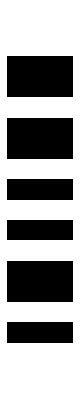
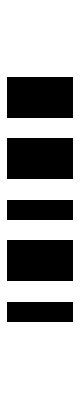
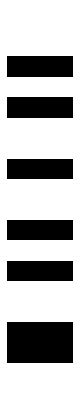
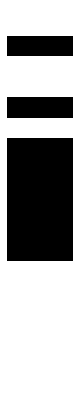
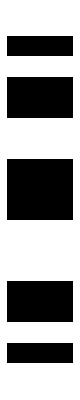
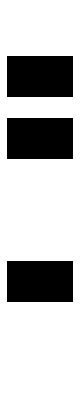
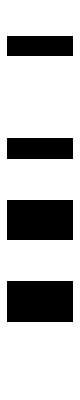
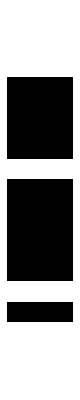
<|qd→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},qm→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},replatted/@qd→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},replatted/@qm→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},xNorQdEd→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},qmOrxNorQdEd→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
ClearAll[sizeVR,w,qd,qm,ed];
Module[{sizeVR=2048,w,qd,qm,ed,randU16,replatted,xNor,xNorQdEd,qmOrxNorQdEd},
randU16[]:=Table[RandomInteger[{0,1},{NSECTIONS,1}],{i,16}];
xNor=notVR@*xorVRs;
(* "replatted" might be reflected in either or both dimensions,
but, with random data, it doesn't matter. *)
replatted[u16_]:=ConstantArray[Flatten@u16,NPLATS]ᵀ;
w=Log[2,sizeVR];Assert[w===11];
qd=randU16[];
qm=randU16[];
ed=Table[randomizedVR[],{i,16}];
xNorQdEd=MapThread[xNor,{replatted/@qd,ed}];
qmOrxNorQdEd=MapThread[orVRs,{replatted/@qm,xNorQdEd}];
<|"qd"->tinyPlot/@qd,
"qm"->tinyPlot/@qm,
"replatted/@qd"->tinyPlot/@replatted/@qd,
"replatted/@qm"->tinyPlot/@replatted/@qm,
(*"ed⟦1⟧"->tinyPlot@(ed⟦1⟧),*)
(*"(replatted/@qd)⟦1⟧"->tinyPlot@(replatted/@qd)⟦1⟧,*)
(*"ed"->tinyPlot/@ed,*)
(*"XNor[ed⟦1⟧,qd*⟦1⟧]"->tinyPlot@xNor[ed⟦1⟧,(replatted/@qd)⟦1⟧],*)
"xNorQdEd"->tinyPlot/@xNorQdEd,
"qmOrxNorQdEd"->tinyPlot/@qmOrxNorQdEd|>
]
```

### Truth Table for XNOR

## Section L1

Each purple block below is a "half-bank" of MMB (described in Section Section of the document) and an L1 (described in this section of the document). There are 64 such purple blocks in the APU chip.

The 64 purple blocks are arranged in 8 APCs with 8 MMB + L1 combinations in each APC.

-Graphics-

For the purposes of this section of the document, only, the word "row" has a special meaning: it's a combination of one of 16 sections of one of 24 SBs/VRs/RNs. To specify such a "row", one must specify BOTH an SB/VR/RN *and* a section number. Thus, there are 16 * 24 = 384 "rows" in a half-bank of MMB. There are also that many "rows" in a full bank of 4096 plats. The word "column" means "plat," for this section of the document only. In an entire APC, then, there are 8 * 384 = 3072 "rows" of MMB.

In a half bank of 384 "rows," there are 384 * 2048 = 786,432 bits.

In a half bank or in a bank, there are 864 "rows" of L1 memory. There are four groups, each with 216 "rows."

Each L1 group is connected to a distinct MMB group via a dedicated vd4 (GGL) vertical data line. Consequently, 4 L1<->MMB data transfers can occur simultaneously per bank of L1 & MMB.
The 216 rows in each L1 group are sub-divided into 24 “Bytes” or \"sets\" - 9 rows/set, in order to facilitate L1 Parity.

Rcall that the L1 works in two modes: 
1) L1 <-> L2 mode. In which only transfers between the L1 and L2 are allowed. (We use apl_set_l1_reg_ext() in this mode)
2) L1 <->MMB mode. In which only transfers between L1 and MMB are allowed. (We use apl_set_l1_reg() in this mode)

Each L1 register is indexed according to the following scheme: (bank_id, group_id, set_id, row_id)
• An L1 bank_id may take a value from the range [0, 4) - 2 bits
• An L1 group_id may take a value from the range [0, 4) - 2 bits
• An L1 set_id may take a value from the range [0, 24) - 5 bits
• An L1 row_id may take a value from the range [0, 9) - 4 bits
Notice that not all set_id and row_ids values are allowed. While the l1_reg can take up to 8192 values, only 3456 (4 x 4 x 24 x 9) are valid.
Each (bank_id, group_id, set_id, row_id) is mapped to a scalar l1_reg as follows:

l1_reg = (bank_id << 11) | (group_id << 9) | (set_id << 4) | row_id.

In L1<-> L2 mode- all fields (bank_id, group_id, set_id, row_id) are active. I will not describe this mode in extent in this email.

In L1<-> MMB mode- only the set_id and row_id fields are active, and bank_id and group_id fields are ignored (since all banks and all groups are active simultaneously)

Next, I describe the L1 <-> MMB mode transfer mechanism:
In this mode, we choose 1 set out of the 24 sets, and a row out of the 9 bits in the set (8 bits for data + 1 bit parity). 
The l1_reg is set as follows:
l1_reg = (set_id << 4) | row_id.

In the APL code the instruction GGL = l1_reg  will set the 4 GGL lines in each column to data stored the address in l1_reg. Recall this happens for all 4 l1_groups, in all banks.
The instruction SM_0X1111: SB[vr] = GGL stores the 4 bits in GGL lines to sections (0,4,8,12).
Next, the instruction GGL = l1_reg + 1 adds offset to the row_id field and sets the 4 GGL lines to the next bit in the set. Which will be stored by SM_0X1111<< 1: SB[vr] = GGL (i.e. sections 1,5,9,13) and so on.

Linking the physical description to the VMR system:
As mentioned, each set in each of the four l1_groups consists of 8 bits (of data). But gvml conventions requires only 4 bits per group in order to build a 16-bit VR. For that reason, each l1 set is logically split into 2 parts: bits 0:3 are assigned to even VMRs, and bits 4:7 are assigned to odd VMRs (as mentioned in previous emails).

As to modeling the L1 in an indexed way. If you wish to follow the physical description above, I think the correct tensor would have the following shapes ( 4 x 4 x 24 x 9 x 4096 ) representing (bank_id, group_id, set_id, row_id, column). 
In this case a VMR j in the range [0,48) will can represented by
VMR[j] = (:, :, [int(j/2)] , [0:3 if j is even OR 4:7 if j is odd] , : ).
However, notice this representation does not offer a direct way to access the value of a specific column in a specific bank.

I hope it is clearer now. If not, I suggest we schedule a meeting for next week with Dan ( as he's on holiday this week) and discuss the issue further.

"

16 sections in each of 24 SBs

4 sections in a group of each of 24 SBs = 96 "rows."

A group of L1 has 216 rows = 192 + 24 = 96 * 2 + 24.

```mathematica
216*4
```

864

```mathematica
216*4*4
```

3456

```mathematica
ClearAll[l1,NROWSPERL1BANK,NCOLSPERL1BANK];
NROWSPERL1BANK=3456;NCOLSPERL1BANK=4096;
l1=ConstantArray[0,{NROWSPERL1BANK,NCOLSPERL1BANK}];
ArrayPlot[l1]
```

-Graphics-

```mathematica
Module[{vr,ggl}]
tinyPlot@randomizedVR[]
```

Module::argmu: Module called with 1 argument; 2 or more arguments are expected.

Module[{vr,ggl}]

-Graphics-

## Section Appendix: Formal Spot-Checking

Spot-check the definition of Var(k) at the edges of the piecewise formula.

```mathematica
ClearAll[var];

With[{V=24,P=2048,S=16,G=4,R=128},
(* Return symbolic constants. *)
var[k1_]:=With[{k=k1-1},
Piecewise[{{MMB[Mod[Quotient[k,P S],V],
Mod[Quotient[k,S],P],
Mod[k,S]], 0≤k<V P S}, {With[{kp=k-V P S},
RL[Mod[Quotient[kp,S],P],
Mod[kp,S]]], V P S≤k<V P S+P S}, {With[{kpp=k-V P S-P S},
GL[Mod[kpp,P]]], V P S+P S≤k<V P S+P S+P}, {With[{kppp=k-V P S-P S-P},
GGL[Mod[Quotient[kppp,G],P],
Mod[kppp,G]]], V P S+P S+P≤k<V P S+P S+P+P G}, {With[{kpppp=k-V P S-P S-P-P G},
RSP16[Mod[Quotient[kpppp,S],R],
Mod[kpppp,S]]], V P S+P S+P+P G≤k<V P S+P S+P+P G+R S}, {Throw["Index out of range"], True}}]]]
```

```mathematica
var[0]
```

Throw::nocatch: Uncaught Throw[Index out of range] returned to top level.

Hold[Throw[Index out of range]]

```mathematica
var[1]
```

MMB[0,0,0]

```mathematica
var[2]
```

MMB[0,0,1]

```mathematica
var[17]
```

MMB[0,1,0]

```mathematica
var[786432]
```

MMB[23,2047,15]

```mathematica
var[786432+1]
```

RL[0,0]

```mathematica
var[786432+32768]
```

RL[2047,15]

```mathematica
var[786432+32768+1]
```

GL[0]

```mathematica
var[786432+32768+2048]
```

GL[2047]

```mathematica
var[786432+32768+2048+1]
```

GGL[0,0]

```mathematica
var[786432+32768+2048+8192]
```

GGL[2047,3]

```mathematica
var[786432+32768+2048+8192+1]
```

RSP16[0,0]

```mathematica
var[786432+32768+2048+8192+2048]
```

RSP16[127,15]

```mathematica
var[831489]
```

Throw::nocatch: Uncaught Throw[Index out of range] returned to top level.

Hold[Throw[Index out of range]]

## Section Full Command Set

Almost all APL commands are preceded by section masks. When a
section mask contains a single ON bit, commands are referred to as
"sactions" [sic]. When multiple bits are ON, the effects of the
instruction are restricted to the indicated subset of sections.
Thus, masks may represent any of the 2^16 subsets of sections.

Section masks, as bit fields, are actually stored in SM_REG_n
registers, where n is 0 through 15. To specify, for example, the
section mask 0x0010, the programmers loads 0x0010 into an SM_REG,
say SM_REG_5, then annotates an APL command as follows:

    SM_REG_5: RL = 1

loading 1 into all plats of section 4 (0x0010 has only bit 4 ON)
of RL.

In addition, mask notation admits inverse by "~" and shifts by
"<<" and ">>" (TODO: verify that right-shifts are supported), so
the programmer might write

    ~(SM_REG_5 << 2) : RL = 1

to load 1 into all sections except section 6 of RL. Section 6
is specified by SM_REG_5 << 2, i.e., 0x0010 << 2 == 0x0040,
which has only section 6 on because 0x0040 has only bit 6 on
(from the right), and ~(SM_REG_5 << 2) means all sections
except section 6.

In the table below, "msk" means a section-mask notation like
the ones illustrated above, naming a particular SM_REG and
with optional shifts and / or inverse.

5.1 WRITE LOGIC
~~~~~~~~~~~~~~~

  in shorter, BNF-style notation

  <SRC> is one of (INV_)?[GL, GGL, RSP16, RL [NEWS]RL]
                  NOTA BENE: <SRC> does NOT include SB!

  As many as three VRs may be written in one clock via the
  following SB notation:

  msk: SB[x]       = <SRC>, e.g., SB[9] = RL
  msk: SB[x, y]    = <SRC>, e.g., SB[3, 14] = GL
  msk: SB[x, y, z] = <SRC>, e.g., SB[1, 2, 3] = WRL

  where x, y, z are each one of RN_REG_0 .. RN_REG_15.

  SB[x] is shorthand for SB[x, x, x],
  SB[x, y] is shorthand for SB[x, y, y]

5.2 READ LOGIC
~~~~~~~~~~~~~~
  +----------------------------------|-------------------------+
  | APL                              | BEL                     |
  +----------------------------------|-------------------------+
  |      immediate APL commands      | op  arg1                |
  +----------------------------------|-------------------------+
  |  1.  msk: RL  = 0                | :=   0                  |
  |  2.  msk: RL  = 1                | :=   1                  |
  +----------------------------------|-------------------------+
  |      combining APL commands      | op  arg1   comb  arg2   |
  +----------------------------------|-------------------------+
  |  3.  msk: RL  =  <SB>            | :=  <SB>                |
  |  4.  msk: RL  =  <SRC>           | :=               <SRC>  |
  |  5.  msk: RL  =  <SB> &  <SRC>   | :=  <SB>    &    <SRC>  |
  |                                  |                         |
  | 10.  msk: RL |=  <SB>            | |=  <SB>                |
  | 11.  msk: RL |=  <SRC>           | |=               <SRC>  |
  | 12.  msk: RL |=  <SB> &  <SRC>   | |=  <SB>    &    <SRC>  |
  |                                  |                         |
  | 13.  msk: RL &=  <SB>            | &=  <SB>                |
  | 14.  msk: RL &=  <SRC>           | &=               <SRC>  |
  | 15.  msk: RL &=  <SB> &  <SRC>   | &=  <SB>    &    <SRC>  |
  |                                  |                         |
  | 18.  msk: RL ^=  <SB>            | ^=  <SB>                |
  | 19.  msk: RL ^=  <SRC>           | ^=               <SRC>  |
  | 20.  msk: RL ^=  <SB> &  <SRC>   | ^=  <SB>    &    <SRC>  |
  +----------------------------------|-------------------------+
  |      special cases               | op  arg1   comb  arg2   |
  +----------------------------------|-------------------------+
  |  6.  msk: RL  =  <SB> |  <SRC>   | :=  <SB>    |    <SRC>  |
  |  7.  msk: RL  =  <SB> ^  <SRC>   | :=  <SB>    ^    <SRC>  |
  |                                  |                         |
  |  8.  msk: RL  = ~<SB> &  <SRC>   | := ~<SB>    &    <SRC>  |
  |  9.  msk: RL  =  <SB> & ~<SRC>   | :=  <SB>    &   ~<SRC>  |
  |                                  |                         |
  | 16.  msk: RL &= ~<SB>            | &= ~<SB>                |
  | 17.  msk: RL &= ~<SRC>           | &= ~<SRC>               |
  +----------------------------------|-------------------------+

  In addition, the following APL commands may be supported by HW but not
  supported by APL concrete syntax because they have no dedicated
  read-control register:

   21.  msk: RL = ~RL & <SRC>
   22.  msk: RL = ~RL & <SB>
   23.  msk: RL = ~RL & (<SB> & <SRC>)
   24.  msk: RL &= ~<SB> | ~<SRC>

5.3 R-SEL LOGIC
~~~~~~~~~~~~~~~

   msk: GL = RL
   msk: GGL = RL
   msk: RSP16 = RL

## Section Appendix: GVML Arithmetic Definitions

/*
 * Copyright (C) 2020, GSI Technology, Inc. All rights reserved.
 *
 * This software source code is the sole property of GSI Technology, Inc.
 * and is proprietary and confidential.
 */

#ifndef ARITH_INST_APL_H
#define ARITH_INST_APL_H

#include <add_sub_utils.apl.h>
#include <common_defs.apl.h>

// *INDENT-OFF*

/*
 * addsub_frag_add_u16(RN_REG x, RN_REG y, RN_REG res, RN_REG x_xor_y, RN_REG cout1)
 * cout1[0] = X[0]^Y[0];
 * cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1]);
 * cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]);
 * cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3]);
 * cout0[0] = X[0]&Y[0];
 * cout0[1] = X[1]&Y[1] | (COUT0[0] & X[1]^Y[1]);
 * cout0[2] = X[2]&Y[2] | (COUT0[1] & X[2]^Y[2]);
 * cout0[3] = X[3]&Y[3] | (COUT0[2] & X[3]^Y[3]);
*/
#define ARITH_ADD_U16_GL_CO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		 SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_FLAG_CICO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		(SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];					\
		(SM_0X0001 << C_FLAG):	GL = RL;						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL = SB[x];						\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;		/* Dummy use of GL */	\
	}{ /* 3 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 4 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 5 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 6 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 8 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 9 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 10 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 12 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 13 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 14 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;


#define ARITH_ADD_S16_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<14):	GGL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001<<15):	RL ^= NRL;						\
		(SM_0X0001<<15):	GL = RL;						\
		~(SM_0X0001<<15):	RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
	}{ /* 13 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_ABS_U16_S16_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;						\
	}{ /* 13 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;

#define ARITH_SUB_ABS_U16_S16_T0_INST(x, y, res, x_xor_noty, cout1, noty)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = ~SB[y] & INV_RSP16;				\
	}{ /* 2 */										\
		SM_0XFFFF:		SB[noty] = RL;						\
		SM_0XFFFF:		RL ^= SB[x]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_noty] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_noty] & GGL;	/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,noty];		/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,noty];		/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,noty];		/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		SM_0X000F:		RL |= SB[cout1];					\
		(SM_0X0001<<3):		GL = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_noty] ^ NRL;				\
		SM_0X0001:		RL = ~SB[x_xor_noty] & INV_RSP16;			\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;						\
	}{ /* 14 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_noty] ^ GGL;				\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;


#define ARITH_ADD_S16_CIN_T0_INST(x, y, t_xory_cbi_t0, t_cbi0, t_cbi1, res) \
                (SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];	/* Load carry in */ \
		(SM_0X0001 << C_FLAG):	GL = RL;		/* Set GL with carry in */ \
	}{ \
		SM_0X0001:	RL = SB[x] & GL;		/* RL[0] = x&ci */ \
		SM_0X0001:	SB[t_xory_cbi_t0] = GL;	/* Save Carry-In in t_xory_cbi_t0 */ \
		~SM_0X0001:	RL = SB[x];		/* RL[1-15] = x */ \
	}{ \
		SM_0X0001:	RL |= SB[y, t_xory_cbi_t0];	/* RL[0] = y&ci | x&ci */ \
		~SM_0X0001:	RL |= SB[y];		/* RL[1-15] = x|y */ \
	}{ \
		~SM_0X0001:	SB[t_xory_cbi_t0] = RL;	/* t_xory_cbi_t0[1-15] = x|y */ \
		~SM_0X0001:	RL = SB[x , y];		/* RL[1-15] = x&y */ \
		SM_0X0001:	RL |= SB[x , y];		/* RL[0]= Cout = x&y | y&ci | x&ci */ \
	}{ \
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;	/* t_cbi0[5,9,13] = x&y */ \
		(SM_0X1111 << 1):	RL |= SB[t_xory_cbi_t0] & NRL; /* RL[1] = Cout[1] = x&y | ci(x|y) */ \
							               /* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */ \
		(SM_0X1111 << 4):	RL |= SB[t_xory_cbi_t0];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */ \
	}{ \
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 2):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 5):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
	}{ \
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 3):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 6):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		(SM_0X1111 << 7):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */ \
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */ \
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */ \
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */ \
	}{ \
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */ \
	}{ \
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */ \
	}{ \
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL; \
		SM_0X0001:	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	RL ^= GL; \
		SM_0X0001:	GL = RL; \
	}{ \
		SM_0X0001:	RL = SB[t_xory_cbi_t0]; \
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL; \
	}{ \
		SM_0XFFFF:	RL ^= SB[x]; \
	}{ \
		SM_0XFFFF:	RL ^= SB[y]; \
	}{ \
		SM_0XFFFF:	SB[res] = RL;	/* res = Cin^x^y */

#define ARITH_SUB_U16_T3_INST(x, y, res) \
                SM_0X0001:	SB[RN_REG_T0] = RSP16; \
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */      \
	}{ \
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */  \
	}{ \
		~SM_0X0001:	SB[RN_REG_T0] = INV_RL;        \
		SM_0X0001:	SB[RN_REG_T1] = INV_RL;    \
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */	 \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res) \


#define ARITH_SUB_U16_NO_BOUT_T0_INST(x, y, res, t_notxxory, t_cbi0, t_cbi1)					\
	   /* 1 */												\
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */					\
	}{ /* 2 */												\
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */					\
	}{ /* 3 */												\
		SM_0XFFFF:	SB[t_notxxory] = INV_RL;							\
		SM_0X0001:	SB[t_cbi0] = INV_RL;								\
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */						\
	}{ /* 4 */												\
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;		/* t_cbi0[5,9,13] = x&y */		\
		(SM_0X1111 << 1):	RL |= SB[t_notxxory] & NRL;	/* RL[1] = Cout[1] = x&y | ci(x|y) */	\
							/* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */	\
		(SM_0X1111 << 4):	RL |= SB[t_notxxory];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */\
	}{ /* 5 */												\
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 2):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 5):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
	}{ /* 6 */												\
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 3):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 6):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 7 */												\
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		(SM_0X1111 << 7):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 8 */												\
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */			\
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */			\
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */			\
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */			\
	}{ /* 9 */												\
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */			\
	}{ /* 10 */												\
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */			\
	}{ /* 11 */												\
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL;							\
		SM_0X0001:		RL = RSP16;								\
	}{ /* 12 */												\
		SM_0XFFFF:	RL ^= SB[t_notxxory];								\
	}{ /* 13 */												\
		SM_0XFFFF:	SB[res] = INV_RL;	/* res = Cin^x^y */

#define ARITH_SUB_S16_T3_INST(res, x, y) \
                        SM_0X0001:	SB[RN_REG_T0] = RSP16; \
                        SM_0XFFFF:	RL = SB[x]; \
                }{ \
                        SM_0XFFFF:	RL ^= SB[y]; \
                }{ \
                        ~SM_0X0001:	SB[RN_REG_T0] = INV_RL; \
                        SM_0X0001:	SB[RN_REG_T1] = INV_RL; \
                        SM_0XFFFF:	RL &= SB[y]; \
                }{ \
                        PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                        KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
                }{ \
                        SUM_SUB_INST(x, y, res)

#define ARITH_SUB_U16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
	}{ \
                SUM_SUB_INST(x, y, res)

#define ARITH_SUB_S16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res)

// input: x, y
// output:	s0 = y[0] ? x>>1 : 0
//		_2x = rotate_left(x)
//		m0 = y[2] ? 0xffff : 0
//		t_y_res_lsb[0]     = y[0] & x[0]
//			   [15..1] = y[15..1]
//		RL = y[1] ? x : 0
#define ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)			\
		SM_0XFFFF:	RL = SB[y];							\
	}{											\
		SM_0XFFFF:	SB[t_y_res_lsb] = RL;	/*t_y_res_lsb = y */			\
		(SM_0X0001 << 2):	GL = RL;	/*GL = y[2]	  */			\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;	/* m0 = y[2] ? 0xffff : 0 */		\
		SM_0XFFFF:		RL = SB[x];	/* RL = x */				\
		(SM_0X0001 << 15):	GGL = RL;	/* GL = x[15] */			\
	}{											\
		~SM_0X0001:	SB[_2x] = NRL;		/* _2x = rotate_left(x) */		\
		SM_0X0001:	RL = SB[t_y_res_lsb];						\
		SM_0X0001:	GL = RL;		/* GL = t_y_res_lsb[0] (= y[0]) */	\
		SM_0X0001:	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[0] ? x ; 0 */			\
	}{											\
		SM_0X0001:	SB[t_y_res_lsb] = RL;	/* t_y_res_lsb[0] = y[0] & x[0]; */	\
		(SM_0X0001 << 15):	SB[s0, s1] = GGL;					\
		(SM_0X00FF << 1):	SB[m1] = RSP16;							\
		(SM_0X00FF << 7):	SB[m1] = RSP16;							\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;	/* s0[15..0] = y[0] ? x>>1 : 0 */	\
		(SM_0X0001 << 1):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 1):	GL = RL;	/* GL[1] = t_y_res_lsb[1] (= y[1]) */	\
		(SM_0X0001 << 15):	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[1] ? x : 0 */			\

#define ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 3):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 3):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 1):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 4):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 4):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 2):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{ 											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 5):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 5):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{ 											\
		(SM_0X0001 << 3):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 6):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 6):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 4):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 7):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 7):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{	(SM_0X0001 << 5):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 8):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 8):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 6):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 9):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 9):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 7):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 10):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 10):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 8):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}											\
	{	~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 11):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 11):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 9):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 12):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 12):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{	SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 10):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 13):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 13):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 11):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 14):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 14):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 12):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m0];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
		(SM_0X0001 << 15):	GGL = RL;						\
	}{											\
		(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	GL = RL;						\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 13):	SB[t_y_res_lsb] = GL; 					\
		SM_0X0001:		RL = SB[c, s0];						\
		(sm_0x3fff << 1):	RL |= SB[_2x, m0, c_xor_s];				\
		(SM_0X0001 << 15):	RL = SB[_2x, m0, c_xor_s] | GGL;			\

#define ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m1];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
	}{											\
		(SM_0X0001 << 14):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define	ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)					\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	RL = SB[s0, m1];					\
	}{ /* 1 */										\
		~(SM_0X0001 << 15):	SB[res_lsb] = RL;					\
		(SM_0X0001 << 15):	SB[s0] = RL;						\
		SM_0XFFFF:		RL = SB[c];						\
	}											\

#define ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)			\
	{/* 2 */										\
		SM_0XFFFF:		RL ^= SB[s0]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[s1] = RL;						\
	}{ /* 4 */										\
		SM_0X1111:		SB[_2x] = RL;						\
		(SM_0X1111<<1):		SB[_2x] = GGL;						\
		(SM_0X1111<<2):		RL = SB[s1] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[c,s0];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[c,s0];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[c,s0];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[_2x];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res_msb] = RL;					\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[_2x] & GL;					\
	}{ /* 11 */										\
		(SM_0X0001 << 15):	SB[res_msb] = RL;					\
	}{	/* end_mul_16() */								\
		~SM_0X0001:		RL = SB[s1] ^ NRL;					\
		SM_0X0001:		RL = SB[res_msb];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		~(SM_0X0001 << 15):	SB[res_msb] = SRL;					\
		(SM_0X0001 << 15):	SB[res_lsb] = GL;					\

#define ARITH_MUL_U16_T0_INST(res_lsb, res_msb, x, y,						\
			      c_xor_s,								\
			      s0, s1, _2x, 							\
			      m0, m1, t_y_res_lsb,						\
			      c,								\
			      sm_0x3fff)							\
		ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{											\
		ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)				\
		ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)		\

// *INDENT-ON*

#endif /* ARITH_INST_APL_H */

/*
 * Copyright (C) 2020, GSI Technology, Inc. All rights reserved.
 *
 * This software source code is the sole property of GSI Technology, Inc.
 * and is proprietary and confidential.
 */

#ifndef ARITH_INST_APL_H
#define ARITH_INST_APL_H

#include <add_sub_utils.apl.h>
#include <common_defs.apl.h>

// *INDENT-OFF*

/*
 * addsub_frag_add_u16(RN_REG x, RN_REG y, RN_REG res, RN_REG x_xor_y, RN_REG cout1)
 * cout1[0] = X[0]^Y[0];
 * cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1]);
 * cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]);
 * cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3]);
 * cout0[0] = X[0]&Y[0];
 * cout0[1] = X[1]&Y[1] | (COUT0[0] & X[1]^Y[1]);
 * cout0[2] = X[2]&Y[2] | (COUT0[1] & X[2]^Y[2]);
 * cout0[3] = X[3]&Y[3] | (COUT0[2] & X[3]^Y[3]);
*/
#define ARITH_ADD_U16_GL_CO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		 SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_FLAG_CICO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		(SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];					\
		(SM_0X0001 << C_FLAG):	GL = RL;						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL = SB[x];						\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;		/* Dummy use of GL */	\
	}{ /* 3 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 4 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 5 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 6 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 8 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 9 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 10 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 12 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 13 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 14 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;


#define ARITH_ADD_S16_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<14):	GGL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001<<15):	RL ^= NRL;						\
		(SM_0X0001<<15):	GL = RL;						\
		~(SM_0X0001<<15):	RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
	}{ /* 13 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_ABS_U16_S16_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;						\
	}{ /* 13 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;

#define ARITH_SUB_ABS_U16_S16_T0_INST(x, y, res, x_xor_noty, cout1, noty)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = ~SB[y] & INV_RSP16;				\
	}{ /* 2 */										\
		SM_0XFFFF:		SB[noty] = RL;						\
		SM_0XFFFF:		RL ^= SB[x]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_noty] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_noty] & GGL;	/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,noty];		/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,noty];		/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,noty];		/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		SM_0X000F:		RL |= SB[cout1];					\
		(SM_0X0001<<3):		GL = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_noty] ^ NRL;				\
		SM_0X0001:		RL = ~SB[x_xor_noty] & INV_RSP16;			\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;						\
	}{ /* 14 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_noty] ^ GGL;				\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;


#define ARITH_ADD_S16_CIN_T0_INST(x, y, t_xory_cbi_t0, t_cbi0, t_cbi1, res) \
                (SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];	/* Load carry in */ \
		(SM_0X0001 << C_FLAG):	GL = RL;		/* Set GL with carry in */ \
	}{ \
		SM_0X0001:	RL = SB[x] & GL;		/* RL[0] = x&ci */ \
		SM_0X0001:	SB[t_xory_cbi_t0] = GL;	/* Save Carry-In in t_xory_cbi_t0 */ \
		~SM_0X0001:	RL = SB[x];		/* RL[1-15] = x */ \
	}{ \
		SM_0X0001:	RL |= SB[y, t_xory_cbi_t0];	/* RL[0] = y&ci | x&ci */ \
		~SM_0X0001:	RL |= SB[y];		/* RL[1-15] = x|y */ \
	}{ \
		~SM_0X0001:	SB[t_xory_cbi_t0] = RL;	/* t_xory_cbi_t0[1-15] = x|y */ \
		~SM_0X0001:	RL = SB[x , y];		/* RL[1-15] = x&y */ \
		SM_0X0001:	RL |= SB[x , y];		/* RL[0]= Cout = x&y | y&ci | x&ci */ \
	}{ \
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;	/* t_cbi0[5,9,13] = x&y */ \
		(SM_0X1111 << 1):	RL |= SB[t_xory_cbi_t0] & NRL; /* RL[1] = Cout[1] = x&y | ci(x|y) */ \
							               /* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */ \
		(SM_0X1111 << 4):	RL |= SB[t_xory_cbi_t0];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */ \
	}{ \
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 2):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 5):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
	}{ \
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 3):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 6):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		(SM_0X1111 << 7):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */ \
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */ \
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */ \
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */ \
	}{ \
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */ \
	}{ \
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */ \
	}{ \
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL; \
		SM_0X0001:	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	RL ^= GL; \
		SM_0X0001:	GL = RL; \
	}{ \
		SM_0X0001:	RL = SB[t_xory_cbi_t0]; \
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL; \
	}{ \
		SM_0XFFFF:	RL ^= SB[x]; \
	}{ \
		SM_0XFFFF:	RL ^= SB[y]; \
	}{ \
		SM_0XFFFF:	SB[res] = RL;	/* res = Cin^x^y */

#define ARITH_SUB_U16_T3_INST(x, y, res) \
                SM_0X0001:	SB[RN_REG_T0] = RSP16; \
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */      \
	}{ \
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */  \
	}{ \
		~SM_0X0001:	SB[RN_REG_T0] = INV_RL;        \
		SM_0X0001:	SB[RN_REG_T1] = INV_RL;    \
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */	 \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res) \


#define ARITH_SUB_U16_NO_BOUT_T0_INST(x, y, res, t_notxxory, t_cbi0, t_cbi1)					\
	   /* 1 */												\
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */					\
	}{ /* 2 */												\
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */					\
	}{ /* 3 */												\
		SM_0XFFFF:	SB[t_notxxory] = INV_RL;							\
		SM_0X0001:	SB[t_cbi0] = INV_RL;								\
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */						\
	}{ /* 4 */												\
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;		/* t_cbi0[5,9,13] = x&y */		\
		(SM_0X1111 << 1):	RL |= SB[t_notxxory] & NRL;	/* RL[1] = Cout[1] = x&y | ci(x|y) */	\
							/* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */	\
		(SM_0X1111 << 4):	RL |= SB[t_notxxory];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */\
	}{ /* 5 */												\
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 2):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 5):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
	}{ /* 6 */												\
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 3):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 6):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 7 */												\
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		(SM_0X1111 << 7):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 8 */												\
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */			\
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */			\
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */			\
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */			\
	}{ /* 9 */												\
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */			\
	}{ /* 10 */												\
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */			\
	}{ /* 11 */												\
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL;							\
		SM_0X0001:		RL = RSP16;								\
	}{ /* 12 */												\
		SM_0XFFFF:	RL ^= SB[t_notxxory];								\
	}{ /* 13 */												\
		SM_0XFFFF:	SB[res] = INV_RL;	/* res = Cin^x^y */

#define ARITH_SUB_S16_T3_INST(res, x, y) \
                        SM_0X0001:	SB[RN_REG_T0] = RSP16; \
                        SM_0XFFFF:	RL = SB[x]; \
                }{ \
                        SM_0XFFFF:	RL ^= SB[y]; \
                }{ \
                        ~SM_0X0001:	SB[RN_REG_T0] = INV_RL; \
                        SM_0X0001:	SB[RN_REG_T1] = INV_RL; \
                        SM_0XFFFF:	RL &= SB[y]; \
                }{ \
                        PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                        KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
                }{ \
                        SUM_SUB_INST(x, y, res)

#define ARITH_SUB_U16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
	}{ \
                SUM_SUB_INST(x, y, res)

#define ARITH_SUB_S16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res)

// input: x, y
// output:	s0 = y[0] ? x>>1 : 0
//		_2x = rotate_left(x)
//		m0 = y[2] ? 0xffff : 0
//		t_y_res_lsb[0]     = y[0] & x[0]
//			   [15..1] = y[15..1]
//		RL = y[1] ? x : 0
#define ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)			\
		SM_0XFFFF:	RL = SB[y];							\
	}{											\
		SM_0XFFFF:	SB[t_y_res_lsb] = RL;	/*t_y_res_lsb = y */			\
		(SM_0X0001 << 2):	GL = RL;	/*GL = y[2]	  */			\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;	/* m0 = y[2] ? 0xffff : 0 */		\
		SM_0XFFFF:		RL = SB[x];	/* RL = x */				\
		(SM_0X0001 << 15):	GGL = RL;	/* GL = x[15] */			\
	}{											\
		~SM_0X0001:	SB[_2x] = NRL;		/* _2x = rotate_left(x) */		\
		SM_0X0001:	RL = SB[t_y_res_lsb];						\
		SM_0X0001:	GL = RL;		/* GL = t_y_res_lsb[0] (= y[0]) */	\
		SM_0X0001:	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[0] ? x ; 0 */			\
	}{											\
		SM_0X0001:	SB[t_y_res_lsb] = RL;	/* t_y_res_lsb[0] = y[0] & x[0]; */	\
		(SM_0X0001 << 15):	SB[s0, s1] = GGL;					\
		(SM_0X00FF << 1):	SB[m1] = RSP16;							\
		(SM_0X00FF << 7):	SB[m1] = RSP16;							\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;	/* s0[15..0] = y[0] ? x>>1 : 0 */	\
		(SM_0X0001 << 1):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 1):	GL = RL;	/* GL[1] = t_y_res_lsb[1] (= y[1]) */	\
		(SM_0X0001 << 15):	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[1] ? x : 0 */			\

#define ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 3):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 3):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 1):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 4):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 4):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 2):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{ 											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 5):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 5):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{ 											\
		(SM_0X0001 << 3):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 6):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 6):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 4):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 7):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 7):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{	(SM_0X0001 << 5):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 8):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 8):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 6):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 9):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 9):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 7):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 10):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 10):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 8):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}											\
	{	~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 11):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 11):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 9):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 12):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 12):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{	SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 10):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 13):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 13):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 11):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 14):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 14):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 12):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m0];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
		(SM_0X0001 << 15):	GGL = RL;						\
	}{											\
		(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	GL = RL;						\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 13):	SB[t_y_res_lsb] = GL; 					\
		SM_0X0001:		RL = SB[c, s0];						\
		(sm_0x3fff << 1):	RL |= SB[_2x, m0, c_xor_s];				\
		(SM_0X0001 << 15):	RL = SB[_2x, m0, c_xor_s] | GGL;			\

#define ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m1];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
	}{											\
		(SM_0X0001 << 14):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define	ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)					\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	RL = SB[s0, m1];					\
	}{ /* 1 */										\
		~(SM_0X0001 << 15):	SB[res_lsb] = RL;					\
		(SM_0X0001 << 15):	SB[s0] = RL;						\
		SM_0XFFFF:		RL = SB[c];						\
	}											\

#define ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)			\
	{/* 2 */										\
		SM_0XFFFF:		RL ^= SB[s0]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[s1] = RL;						\
	}{ /* 4 */										\
		SM_0X1111:		SB[_2x] = RL;						\
		(SM_0X1111<<1):		SB[_2x] = GGL;						\
		(SM_0X1111<<2):		RL = SB[s1] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[c,s0];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[c,s0];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[c,s0];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[_2x];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res_msb] = RL;					\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[_2x] & GL;					\
	}{ /* 11 */										\
		(SM_0X0001 << 15):	SB[res_msb] = RL;					\
	}{	/* end_mul_16() */								\
		~SM_0X0001:		RL = SB[s1] ^ NRL;					\
		SM_0X0001:		RL = SB[res_msb];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		~(SM_0X0001 << 15):	SB[res_msb] = SRL;					\
		(SM_0X0001 << 15):	SB[res_lsb] = GL;					\

#define ARITH_MUL_U16_T0_INST(res_lsb, res_msb, x, y,						\
			      c_xor_s,								\
			      s0, s1, _2x, 							\
			      m0, m1, t_y_res_lsb,						\
			      c,								\
			      sm_0x3fff)							\
		ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{											\
		ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)				\
		ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)		\

// *INDENT-ON*

#endif /* ARITH_INST_APL_H */